Heating a Constant-Volume Process on a PV-Diagram

```mathematica
SaturationData={
{372.,0.097326,0.001042535446205171,1.7373175816539264,414.214,2505.},{373.,0.100876,0.0010432968179447052,1.6801075268817205,418.428,2506.},{374.,0.104533,0.001044168319933173,1.6252234682268814,422.643,2507.},{375.,0.108299,0.0010449320794148381,1.572327044025157,426.859,2508.},{376.,0.112177,0.001045696957021855,1.5213753232922562,431.076,2509.},{377.,0.116169,0.0010464629552113854,1.4723203769140165,435.295,2511.},{378.,0.120277,0.0010473397570171764,1.4253135689851768,439.514,2512.},{379.,0.124504,0.0010481081647626034,1.3798813302056023,443.735,2513.},{380.,0.128853,0.001048987726843596,1.3363624214887078,447.957,2514.},{381.,0.133327,0.0010497585555322277,1.2943308309603936,452.18,2515.},{382.,0.137927,0.0010506408909434755,1.2539184952978057,456.405,2516.},{383.,0.142658,0.0010514141520344864,1.2150668286755772,460.63,2518.},{384.,0.147521,0.001052299273913501,1.177440244907571,464.858,2519.},{385.,0.15252,0.00105318588730911,1.141422212076247,469.086,2520.},{386.,0.157656,0.0010539629005059021,1.1065619121389842,473.316,2521.},{387.,0.162934,0.0010548523206751054,1.0729613733905579,477.547,2522.},{388.,0.168356,0.001055743243243243,1.040582726326743,481.78,2523.},{389.,0.173926,0.0010566356720202875,1.009387301907742,486.014,2524.},{390.,0.179645,0.0010575296108291032,0.9794319294809012,490.249,2525.},{391.,0.185517,0.0010584250635055038,0.9505703422053231,494 .486,2527},{392.,0.191545,0.001059322033898305,0.9225092250922509,498.725,2528.},{393.,0.197732,0.0010602205258693808,0.8952551477170994,502.965,2529.},{394.,0.204082,0.0010611205432937182,0.8688097306689835,507.207,2530.},{395.,0.210597,0.0010620220900594733,0.8438818565400843,511.45,2531.},{396.,0.217281,0.0010629251700680273,0.819672131147541,515.695,2532.},{397.,0.224137,0.0010638297872340426,0.7961783439490446,519.941,2533.},{398.,0.231168,0.0010648493238206793,0.7733952049497294,524.189,2534.},{399.,0.238378,0.0010657572205051689,0.7513148009015778,528.439,2535.},{400.,0.245769,0.0010666666666666667,0.7304601899196493,532.691,2536.},{401.,0.253346,0.001067691650651292,0.7097232079488999,536.944,2537.},{402.,0.261112,0.001068604402650139,0.6901311249137336,541.199,2538.},{403.,0.26907,0.0010695187165775401,0.670690811535882,545.456,2539.},(*{404.,0.277223,0.0010705491917353603,0.6523157208088716,549.715,2540.},*){405.,0.285576,0.0010714668381013607,0.6345177664974619,553.975,2541.},{406.,0.294131,0.0010725010725010724,0.6169031462060457,558.238,2542.},{407.,0.302893,0.0010735373054213634,0.6002400960384154,562.502,2543.},{408.,0.311865,0.0010744600838078866,0.5841121495327103,566.768,2545.},{409.,0.321051,0.0010755001075500108,0.5685048322910745,571.036,2546.},{410.,0.330454,0.0010765421466250404,0.5530973451327433,575.307,2547.},{411.,0.340079,0.0010775862068965517,0.5385029617662898,579.579,2548.},{412.,0.349929,0.0010785159620362382,0.5243838489774515,583.853,2548.},{413.,0.360007,0.0010795638562020944,0.5104645227156712,588.13,2549.},{414.,0.277223,0.0010705491917353603,0.6523157208088716,549.715,2540.},{415.,0.380867,0.001081665765278529,0.48426150121065376,596.689,2551.},{416.,0.391655,0.0010827197921178,0.4716981132075471,600.972,2552.},{417.,0.402689,0.0010837758751490192,0.45955882352941174,605.257,2553.},{418.,0.413971,0.0010848340203948796,0.4476275738585497,609.544,2554.},{419.,0.425505,0.0010860121633362294,0.43630017452006986,613.834,2555.},{420.,0.437297,0.0010870746820306556,0.4251700680272109,618.125,2556.},{421.,0.449349,0.001088139281828074,0.4144218814753419,622.42,2557.},{422.,0.461666,0.0010892059688487094,0.40404040404040403,626.716,2558.},{423.,0.474253,0.0010903936321011885,0.39401103230890466,631.015,2559.},{424.,0.487113,0.0010914647456887142,0.384172109104879,635.316,2560.},{425.,0.500251,0.001092537965694308,0.37467216185837393,639.62,2561.},{426.,0.513671,0.0010937329104232748,0.36536353671903543,643.927,2562.},{427.,0.527378,0.0010948105977665863,0.3563791874554526,648.235,2563.},{428.,0.541375,0.0010960105217010083,0.34770514603616137,652.547,2563.},{429.,0.555668,0.0010970927043335162,0.33932813030200204,656.861,2564.},{430.,0.57026,0.001098297638660077,0.33112582781456956,661.177,2565.},{431.,0.585156,0.0010995052226498076,0.32310177705977383,665.497,2566.},{432.,0.600361,0.001100594320933304,0.315357931251971,669.819,2567.},{433.,0.61588,0.0011018069634200088,0.30788177339901474,674.143,2568.},{434.,0.631716,0.0011030222810500773,0.30057108506161706,678.471,2568.},{435.,0.647874,0.0011042402826855124,0.293513354857646,682.801,2569.},{436.,0.66436,0.001105460977227504,0.2866150759529951,687.134,2570.},{437.,0.681178,0.0011065619121389842,0.279876854184159,691.47,2571.},{438.,0.698332,0.0011077877478675084,0.2733734281027884,695.809,2572.},{439.,0.715827,0.0011090163025396472,0.2670940170940171,700.15,2573.},{440.,0.733669,0.0011103708638685321,0.26089225150013046,704.495,2573.},{441.,0.751862,0.0011116051578479323,0.2549069589599796,708.843,2574.},{442.,0.77041,0.001112842198976185,0.24906600249066005,713.194,2575.},{443.,0.789319,0.0011140819964349377,0.24342745861733206,717.548,2576.},{444.,0.808594,0.001115324559446799,0.237925291458482,721.905,2576.},{445.,0.82824,0.0011165698972755694,0.23255813953488372,726.265,2577.},{446.,0.848261,0.0011179429849077697,0.22732439190725165,730.628,2578.},{447.,0.868663,0.001119194180190263,0.22227161591464772,734.995,2579.},{448.,0.88945,0.0011205737337516809,0.21729682746631898,739.365,2579.},{449.,0.910629,0.001121830827911151,0.21249468763280915,743.738,2580.},{450.,0.932204,0.0011232168931820735,0.2078137988362427,748.115,2581.},{451.,0.954179,0.0011244799280332846,0.2032520325203252,752.495,2581.},{452.,0.976562,0.001125872551227201,0.19880715705765406,756.878,2582.},{453.,0.999356,0.001127141568981064,0.19447685725398675,761.265,2583.},{454.,1.023,0.0011285407967498026,0.1902587519025875,765.655,2583.},{455.,1.046,0.0011299435028248588,0.18615040953090098,770.049,2584.},{456.,1.07,0.0011313497001923295,0.18214936247723132,774.447,2585.},{457.,1.095,0.0011326311020500622,0.17825311942959002,778.848,2585.},{458.,1.1199999999999999,0.0011340440009072353,0.17445917655268667,783.253,2586.},{459.,1.145,0.0011354604292040421,0.17076502732240437,787.662,2587.},{460.,1.171,0.001136880400181901,0.16714023065351832,792.075,2587.},{461.,1.1969999999999998,0.0011383039271485487,0.16363933889707086,796.491,2588.},{462.,1.224,0.0011397310234784591,0.16020506247997437,800.911,2588.},{463.,1.251,0.001141291942478886,0.1568627450980392,805.335,2589.},{464.,1.279,0.0011427265455376528,0.1535862386730149,809.763,2589.},{465.,1.307,0.0011441647597254005,0.15042117930204574,814.195,2590.},{466.,1.3359999999999999,0.0011456065986940084,0.1473187978786093,818.632,2591.},{467.,1.365,0.001147183664104623,0.14427932477276006,823.072,2591.},{468.,1.394,0.0011486331265793705,0.14132278123233466,827.516,2592.},{469.,1.424,0.0011500862564692352,0.13844662882458814,831.965,2592.},{470.,1.4549999999999998,0.0011516756881262238,0.13563000135630002,836.418,2593.},{471.,1.486,0.0011531365313653136,0.13289036544850497,840.875,2593.},{472.,1.518,0.0011547344110854503,0.13020833333333334,845.337,2594.},{473.,1.5499999999999998,0.001156336725254394,0.12759984688018375,849.803,2594.},{474.,1.583,0.001157809424568716,0.12504689258471927,854.273,2595.},{475.,1.6159999999999999,0.0011594202898550724,0.12254901960784313,858.748,2595.},{476.,1.65,0.0011610356437942646,0.12012012012012013,863.228,2595.},{477.,1.684,0.001162655505173817,0.11774402449075709,867.712,2596.},{478.,1.7189999999999999,0.0011642798928862498,0.11542012927054479,872.201,2596.},{479.,1.754,0.0011659088259298122,0.11316057485572027,876.694,2597.},{480.,1.7899999999999998,0.0011675423234092236,0.11093854004881297,881.192,2597.},{481.,1.827,0.0011691804045364201,0.10877841836179702,885.696,2598.},{482.,1.8639999999999999,0.0011708230886313077,0.10666666666666667,890.204,2598.},{483.,1.902,0.0011724703951225231,0.10460251046025104,894.717,2598.},{484.,1.94,0.0011741223435481976,0.10257462303826033,899.235,2599.},{485.,1.9789999999999999,0.001175917215428034,0.1006036217303823,903.758,2599.},{486.,2.019,0.0011775788977861517,0.09871668311944717,908.286,2599.},{487.,2.059,0.0011792452830188679,0.0968054211035818,912.819,2600.},{488.,2.1,0.0011810558639423643,0.0949667616334283,917.358,2600.},{489.,2.141,0.0011827321111768185,0.0931098696461825,921.902,2600.},{490.,2.183,0.0011845534233593934,0.09140767824497258,926.452,2600.},{491.,2.226,0.0011862396204033216,0.08968609865470852,931.006,2601.},{492.,2.2689999999999997,0.0011880717595342757,0.08795074758135445,935.567,2601.},{493.,2.3129999999999997,0.0011899095668729176,0.08635578583765112,940.133,2601.},{494.,2.358,0.001191753068764152,0.0847457627118644,944.704,2601.},{495.,2.403,0.0011936022917164002,0.0831255195344971,949.281,2602.},{496.,2.449,0.001195457262402869,0.08163265306122448,953.864,2602.},{497.,2.495,0.0011973180076628352,0.08012820512820512,958.453,2602.},{498.,2.5429999999999997,0.001199184554502938,0.07861635220125786,963.048,2602.},{499.,2.5909999999999997,0.0012010569300984866,0.07716049382716049,967.649,2602.},{500.,2.639,0.0012029351617947794,0.07575757575757576,972.256,2603.},{501.,2.689,0.0012048192771084338,0.0744047619047619,976.869,2603.},{502.,2.739,0.0012067093037287317,0.07304601899196494,981.488,2603.},{503.,2.7889999999999997,0.00120875135984528,0.07168458781362008,986.114,2603.},{504.,2.8409999999999997,0.0012106537530266344,0.07042253521126761,990.745,2603.},{505.,2.893,0.001212709192335678,0.0691085003455425,995.384,2603.},{506.,2.9459999999999997,0.0012146240738491437,0.06788866259334692,1000.,2603.},{507.,3.,0.0012166930283489476,0.06666666666666667,1004.9999999999999,2603.},{508.,3.054,0.001218769043266301,0.06548788474132286,1008.9999999999999,2603.},{509.,3.11,0.001220703125,0.06430868167202572,1014.,2603.},{510.,3.166,0.0012227928588897043,0.06317119393556538,1018.9999999999999,2603.},{511.,3.222,0.001224889759921607,0.06203473945409429,1022.9999999999999,2603.},{512.,3.28,0.001226993865030675,0.06093845216331505,1028.,2603.},{513.,3.3379999999999996,0.0012291052114060963,0.059880239520958084,1033.,2603.},{514.,3.397,0.0012312238364934744,0.058823529411764705,1037.,2603.},{515.,3.457,0.0012335019119279634,0.057770075101097634,1042.,2603.},{516.,3.518,0.0012356357345854442,0.056753688989784334,1047.,2603.},{517.,3.5789999999999997,0.0012377769525931427,0.055772448410485224,1052.,2603.},{518.,3.642,0.001240079365079365,0.0547945205479452,1056.,2603.},{519.,3.7049999999999996,0.0012422360248447205,0.05385029617662897,1061.,2603.},{520.,3.7689999999999997,0.0012445550715619166,0.052910052910052914,1066.,2602.},{521.,3.8339999999999996,0.0012467273407305822,0.052002080083203325,1071.,2602.},{522.,3.9,0.0012490632025980515,0.05109862033725089,1075.,2602.},{523.,3.9659999999999997,0.0012514078338130396,0.050226017076845805,1080.,2602.},{524.,4.034,0.0012537612838515546,0.04935834155972359,1085.,2602.},{525.,4.102,0.0012561236025624921,0.04849660523763336,1090.,2601.},{526.,4.171,0.0012584948401711553,0.047664442326024785,1094.,2601.},{527.,4.241,0.0012608750472828142,0.046860356138706656,1099.,2601.},{528.,4.311999999999999,0.0012632642748863063,0.046061722708429294,1104.,2601.},{529.,4.3839999999999995,0.0012656625743576763,0.04526935264825713,1109.,2600.},{530.,4.457,0.0012682308180088776,0.044503782821539835,1114.,2600.},{531.,4.531,0.0012706480304955528,0.043744531933508315,1119.,2600.},{532.,4.6049999999999995,0.0012732365673542145,0.043010752688172046,1123.,2599.},{533.,4.681,0.0012756729174639623,0.042283298097251586,1128.,2599.},{534.,4.757,0.001278281989006775,0.04156275976724855,1133.,2598.},{535.,4.835,0.0012809017548354041,0.040866366979975484,1138.,2598.},{536.,4.912999999999999,0.001283532280836863,0.040176777822418644,1143.,2597.},{537.,4.992999999999999,0.0012861736334405145,0.039510075069142635,1148.,2597.},{538.,5.0729999999999995,0.001288825879623663,0.038850038850038855,1153.,2597.},{539.,5.154999999999999,0.0012914890869172157,0.03819709702062643,1158.,2596.},{540.,5.237,0.0012941633234114145,0.03755163349605708,1163.,2595.},{541.,5.319999999999999,0.0012970168612191958,0.03692762186115214,1167.,2595.},{542.,5.404999999999999,0.0012997140629061607,0.03631082062454612,1172.,2594.},{543.,5.489999999999999,0.0013025921583952064,0.03571428571428571,1177.,2594.},{544.,5.577,0.0013054830287206266,0.0351123595505618,1182.,2593.},{545.,5.664,0.0013082155939298796,0.034530386740331494,1187.,2593.},{546.,5.753,0.0013111315064901008,0.033967391304347824,1192.,2592.},{547.,5.842,0.001314060446780552,0.0334001336005344,1197.,2591.},{548.,5.933,0.0013170025023047545,0.0328515111695138,1202.,2590.},{549.,6.024,0.0013201320132013201,0.03231017770597738,1207.,2590.},{550.,6.117,0.0013231013495633766,0.03177629488401652,1212.,2589.},{551.,6.210999999999999,0.0013260840737302744,0.03125,1217.,2588.},{552.,6.306,0.0013292569453675397,0.03073140749846343,1222.,2587.},{553.,6.402,0.0013324450366422385,0.030229746070133012,1228.,2587.},{554.,6.499,0.0013354700854700855,0.029726516052318668,1233.,2586.},{555.,6.598,0.0013386880856760374,0.029239766081871343,1238.,2585.},{556.,6.697,0.0013419216317767041,0.02876042565429968,1243.,2584.},{557.,6.798,0.0013451708366962604,0.028288543140028287,1248.,2583.},{558.,6.899,0.0013486176668914363,0.02782415136338342,1253.,2582.},{559.,7.002,0.00135189941868325,0.02736726874657909,1258.,2581.},{560.,7.106,0.0013553808620222283,0.026917900403768506,1263.,2580.},{561.,7.210999999999999,0.001358695652173913,0.026476039184537992,1269.,2579.},{562.,7.318,0.0013622122326658493,0.026041666666666668,1274.,2578.},{563.,7.425999999999999,0.0013657470636438131,0.025621316935690495,1279.,2577.},{564.,7.534,0.0013693002875530605,0.02520161290322581,1284.,2576.},{565.,7.643999999999999,0.0013728720483250961,0.024783147459727383,1290.,2574.},{566.,7.755999999999999,0.0013766519823788547,0.024378352023403216,1295.,2573.},{567.,7.867999999999999,0.0013802622498274672,0.023980815347721823,1300.,2572.},{568.,7.981999999999999,0.001384083044982699,0.02358490566037736,1305.,2571.},{569.,8.097,0.0013879250520471894,0.02320185614849188,1311.,2569.},{570.,8.213,0.0013917884481558804,0.022820629849383843,1316.,2568.},{571.,8.331,0.0013956734124214933,0.022446689113355782,1321.,2567.},{572.,8.45,0.0013995801259622112,0.02207505518763797,1327.,2565.},{573.,8.57,0.001403705783267827,0.02171552660152009,1332.,2564.},{574.,8.690999999999999,0.0014076576576576578,0.021358393848782572,1338.,2562.},{575.,8.814,0.0014118311449950586,0.021003990758244065,1343.,2561.},{576.,8.937999999999999,0.0014160294534126309,0.02066115702479339,1348.,2559.},{577.,9.064,0.0014202528049992898,0.020316944331572533,1354.,2558.},{578.,9.19,0.0014245014245014246,0.019984012789768187,1359.,2556.},{579.,9.318,0.0014289797084881396,0.019654088050314465,1365.,2554.},{580.,9.448,0.00143348623853211,0.019327406262079627,1370.,2553.},{581.,9.578999999999999,0.0014380212827149843,0.019007793195210038,1376.,2551.},{582.,9.711,0.0014425851125216386,0.018691588785046728,1381.,2549.},{583.,9.844999999999999,0.001447178002894356,0.01838235294117647,1387.,2547.},{584.,9.98,0.0014518002322880372,0.018073377914332188,1393.,2545.},{585.,10.12,0.0014566642388929353,0.01777145903678692,1398.,2544.},{586.,10.25,0.0014615609470914935,0.017476406850751487,1404.,2542.},{587.,10.389999999999999,0.0014664906877841326,0.017182130584192438,1410.,2540.},{588.,10.53,0.0014716703458425313,0.0168947457340767,1415.,2537.},{589.,10.68,0.0014766686355581807,0.016608536787908985,1421.,2535.},{590.,10.82,0.0014819205690574987,0.016329196603527107,1427.,2533.},{591.,10.969999999999999,0.0014872099940511601,0.01605136436597111,1433.,2531.},{592.,11.11,0.0014927601134497688,0.015780337699226765,1439.,2529.},{593.,11.259999999999998,0.00149812734082397,0.015511090429657206,1444.,2526.},{594.,11.41,0.0015037593984962407,0.015246226558926665,1450.,2524.},{595.,11.559999999999999,0.0015094339622641509,0.014983518130056939,1456.,2522.},{596.,11.719999999999999,0.0015153811183512653,0.014725371815638346,1462.,2519.},{597.,11.87,0.0015213753232922564,0.014471780028943561,1468.,2516.},{598.,12.03,0.001527417137620284,0.014220705346985212,1474.,2514.},{599.,12.19,0.0015335071308081583,0.013972334777141262,1480.,2511.},{600.,12.34,0.001539882968894364,0.01372872048325096,1486.,2508.},{601.,12.509999999999998,0.0015463120457708365,0.013486176668914362,1492.,2506.},{602.,12.669999999999998,0.0015527950310559005,0.013248542660307365,1499.,2503.},{603.,12.83,0.0015595757953836555,0.013014055179593961,1505.,2500.},{604.,13.,0.0015664160401002508,0.01278118609406953,1511.,2497.},{605.,13.17,0.0015735641227380016,0.012551776076314799,1517.,2493.},{606.,13.34,0.0015807777426493834,0.01232589670898558,1524.,2490.},{607.,13.51,0.001588057805304113,0.012102142079148009,1530.,2487.},{608.,13.680000000000001,0.0015956598053295035,0.011880717595342758,1537.,2483.},{609.,13.859999999999998,0.00160333493666827,0.011661807580174927,1543.,2480.},{610.,14.03,0.0016110842597067826,0.011445576284765937,1550.,2476.},{611.,14.209999999999999,0.0016194331983805667,0.011232168931820734,1556.,2473.},{612.,14.389999999999999,0.0016276041666666667,0.01102049812651532,1563.,2469.},{613.,14.569999999999999,0.0016361256544502616,0.010811979673478215,1570.,2465.},{614.,14.76,0.0016450074025333116,0.010605578534309046,1576.,2461.},{615.,14.94,0.0016542597187758478,0.010400416016640665,1583.,2457.},{616.,15.129999999999997,0.00166333998669328,0.010197838058331634,1590.,2453.},{617.,15.319999999999999,0.0016730801405387317,0.01,1597.,2448.},{618.,15.51,0.0016829350387075057,0.009794319294809012,1604.,2444.},{619.,15.709999999999999,0.0016931933626820183,0.009606147934678195,1611.,2439.},{620.,15.899999999999999,0.0017038677798602829,0.009407337723424272,1619.,2434.},{621.,16.1,0.001714971702966901,0.009216589861751152,1626.,2429.},{622.,16.299999999999997,0.0017262213015708616,0.009025270758122744,1633.,2424.},{623.,16.5,0.0017382235355466714,0.0088339222614841,1641.,2419.},{624.,16.7,0.0017503938386136883,0.008643042350907518,1649.,2413.},{625.,16.91,0.0017633574325515782,0.0084530853761623,1656.,2408.},{626.,17.12,0.0017768301350390904,0.008264462809917356,1664.,2402.},{627.,17.33,0.0017908309455587394,0.008084074373484237,1672.,2396.},{628.,17.54,0.001805706031058144,0.007898894154818327,1681.,2389.},{629.,17.75,0.001821161901293025,0.007710100231303007,1689.,2383.},{630.,17.97,0.0018375597206909222,0.00753012048192771,1698.,2376.},{631.,18.189999999999998,0.0018545994065281898,0.007342143906020559,1707.,2369.},{632.,18.41,0.0018730099269526129,0.007158196134574088,1716.,2361.},{633.,18.63,0.0018925056775170325,0.006978367062107466,1725.,2353.},{634.,18.86,0.0019131432944327529,0.006793478260869566,1734.,2345.},{635.,19.09,0.0019353590090961871,0.006609385327164573,1744.,2336.},{636.,19.32,0.0019592476489028216,0.0064226075786769435,1755.,2326.},{637.,19.55,0.001984914648670107,0.006230529595015576,1765.,2316.},{638.,19.79,0.002012882447665056,0.006042296072507553,1776.,2305.},{639.,20.019999999999996,0.002043318348998774,0.0058445353594389245,1788.,2294.},{640.,20.27,0.0020768431983385254,0.005646527385657821,1800.,2281.},{641.,20.509999999999998,0.0021141649048625794,0.00543773790103317,1813.,2267.},{642.,20.759999999999998,0.0021565667457407807,0.005221932114882507,1826.,2251.},
{642.,20.759999999999998,0.0021565667457407807,0.005221932114882507,1826.,2251.},{643.,21.009999999999998,0.0022070183182520413,0.00499001996007984,1842.,2233.},{644.,21.259999999999998,0.002269117313365101,0.004739336492890996,1859.,2212.},{645.,21.52,0.002352941176470588,0.004454342984409799,1880.,2185.},{646.,21.77,0.0024813895781637717,0.004106776180698152,1909.,2149.},{647.,22.04,0.0027987685418415895,0.0034904013961605585,1968.,2072.},
{647.1,22.06,1/322,1/322,2016,2016}};
```

```mathematica
VLE11={{372.,0.097326,0.0010426,414.21,372.,0.097326,1.7374,2504.7},{374.,0.10453,0.0010441,422.64,374.,0.10453,1.6251,2507.},{376.,0.11218,0.0010457,431.08,376.,0.11218,1.5213,2509.4},{378.,0.12028,0.0010473,439.51,378.,0.12028,1.4253,2511.7},{380.,0.12885,0.001049,447.96,380.,0.12885,1.3364,2514.1},{382.,0.13793,0.0010506,456.4,382.,0.13793,1.2539,2516.4},{384.,0.14752,0.0010523,464.86,384.,0.14752,1.1775,2518.6},{386.,0.15766,0.001054,473.32,386.,0.15766,1.1065,2520.9},{388.,0.16836,0.0010557,481.78,388.,0.16836,1.0406,2523.2}};
```

```mathematica
V11={{390.,0.17601,1.,2525.7},{392.,0.17699,1.,2528.9},{394.,0.17798,1.,2532.1},{396.,0.17896,1.,2535.3},{398.,0.17993,1.,2538.4},{400.,0.18091,1.,2541.6},{402.,0.18188,1.,2544.7},{404.,0.18286,1.,2547.9},{406.,0.18383,1.,2551.},{408.,0.1848,1.,2554.1},{410.,0.18577,1.,2557.2},{412.,0.18673,1.,2560.3},{414.,0.1877,1.,2563.5},{416.,0.18867,1.,2566.6},{418.,0.18963,1.,2569.6},{420.,0.19059,1.,2572.7},{422.,0.19155,1.,2575.8},{424.,0.19252,1.,2578.9},{426.,0.19348,1.,2582.},{428.,0.19444,1.,2585.1},{430.,0.19539,1.,2588.1},{432.,0.19635,1.,2591.2},{434.,0.19731,1.,2594.3},{436.,0.19826,1.,2597.3},{438.,0.19922,1.,2600.4},{440.,0.20017,1.,2603.5},{442.,0.20113,1.,2606.5},{444.,0.20208,1.,2609.6},{446.,0.20303,1.,2612.6},{448.,0.20399,1.,2615.7},{450.,0.20494,1.,2618.8},{452.,0.20589,1.,2621.8},{454.,0.20684,1.,2624.9},{456.,0.20779,1.,2627.9},{458.,0.20874,1.,2631.},{460.,0.20969,1.,2634.},{462.,0.21063,1.,2637.1},{464.,0.21158,1.,2640.1},{466.,0.21253,1.,2643.2},{468.,0.21348,1.,2646.2},{470.,0.21442,1.,2649.3},{472.,0.21537,1.,2652.3},{474.,0.21631,1.,2655.4},{476.,0.21726,1.,2658.4},{478.,0.2182,1.,2661.4},{480.,0.21915,1.,2664.5},{482.,0.22009,1.,2667.5},{484.,0.22104,1.,2670.6},{486.,0.22198,1.,2673.6},{488.,0.22292,1.,2676.7},{490.,0.22386,1.,2679.7},{492.,0.22481,1.,2682.8},{494.,0.22575,1.,2685.9},{496.,0.22669,1.,2688.9},{498.,0.22763,1.,2692.},{500.,0.22857,1.,2695.},{502.,0.22951,1.,2698.1},{504.,0.23045,1.,2701.1},{506.,0.23139,1.,2704.2},{508.,0.23233,1.,2707.2},{510.,0.23327,1.,2710.3},{512.,0.23421,1.,2713.4},{514.,0.23515,1.,2716.4},{516.,0.23609,1.,2719.5},{518.,0.23703,1.,2722.6},{520.,0.23797,1.,2725.6},{522.,0.23891,1.,2728.7},{524.,0.23984,1.,2731.8},{526.,0.24078,1.,2734.8},{528.,0.24172,1.,2737.9},{530.,0.24266,1.,2741.},{532.,0.2436,1.,2744.},{534.,0.24453,1.,2747.1},{536.,0.24547,1.,2750.2},{538.,0.24641,1.,2753.3},{540.,0.24734,1.,2756.4},{542.,0.24828,1.,2759.4},{544.,0.24922,1.,2762.5},{546.,0.25015,1.,2765.6},{548.,0.25109,1.,2768.7},{550.,0.25202,1.,2771.8},{552.,0.25296,1.,2774.9},{554.,0.25389,1.,2778.},{556.,0.25483,1.,2781.1},{558.,0.25576,1.,2784.2},{560.,0.2567,1.,2787.3},{562.,0.25763,1.,2790.4},{564.,0.25857,1.,2793.5},{566.,0.2595,1.,2796.6},{568.,0.26044,1.,2799.7},{570.,0.26137,1.,2802.8},{572.,0.26231,1.,2805.9},{574.,0.26324,1.,2809.},{576.,0.26417,1.,2812.1},{578.,0.26511,1.,2815.2},{580.,0.26604,1.,2818.3},{582.,0.26697,1.,2821.5},{584.,0.26791,1.,2824.6},{586.,0.26884,1.,2827.7},{588.,0.26977,1.,2830.8},{590.,0.27071,1.,2833.9},{592.,0.27164,1.,2837.1},{594.,0.27257,1.,2840.2},{596.,0.27351,1.,2843.3},{598.,0.27444,1.,2846.5},{600.,0.27537,1.,2849.6},{602.,0.2763,1.,2852.7},{604.,0.27724,1.,2855.9},{606.,0.27817,1.,2859.},{608.,0.2791,1.,2862.2},{610.,0.28003,1.,2865.3},{612.,0.28096,1.,2868.5},{614.,0.2819,1.,2871.6},{616.,0.28283,1.,2874.8},{618.,0.28376,1.,2877.9},{620.,0.28469,1.,2881.1},{622.,0.28562,1.,2884.3},{624.,0.28655,1.,2887.4},{626.,0.28749,1.,2890.6},{628.,0.28842,1.,2893.8},{630.,0.28935,1.,2896.9},{632.,0.29028,1.,2900.1},{634.,0.29121,1.,2903.3},{636.,0.29214,1.,2906.5},{638.,0.29307,1.,2909.6},{640.,0.294,1.,2912.8},{642.,0.29494,1.,2916.},{644.,0.29587,1.,2919.2},{646.,0.2968,1.,2922.4},{648.,0.29773,1.,2925.6},{650.,0.29866,1.,2928.8},{652.,0.29959,1.,2932.},{654.,0.30052,1.,2935.2},{656.,0.30145,1.,2938.4},{658.,0.30238,1.,2941.6},{660.,0.30331,1.,2944.8},{662.,0.30424,1.,2948.},{664.,0.30517,1.,2951.2},{666.,0.3061,1.,2954.4},{668.,0.30703,1.,2957.6},{670.,0.30796,1.,2960.8},{672.,0.30889,1.,2964.},{674.,0.30982,1.,2967.3},{676.,0.31075,1.,2970.5},{678.,0.31168,1.,2973.7},{680.,0.31261,1.,2976.9},{682.,0.31354,1.,2980.2},{684.,0.31447,1.,2983.4},{686.,0.3154,1.,2986.6},{688.,0.31633,1.,2989.9},{690.,0.31726,1.,2993.1},{692.,0.31819,1.,2996.4},{694.,0.31912,1.,2999.6},{696.,0.32004,1.,3002.9},{698.,0.32097,1.,3006.1},{700.,0.3219,1.,3009.4},{702.,0.32283,1.,3012.6},{704.,0.32376,1.,3015.9},{706.,0.32469,1.,3019.2},{708.,0.32562,1.,3022.4},{710.,0.32655,1.,3025.7},{712.,0.32748,1.,3029.},{714.,0.32841,1.,3032.2},{716.,0.32934,1.,3035.5},{718.,0.33026,1.,3038.8},{720.,0.33119,1.,3042.1},{722.,0.33212,1.,3045.3},{724.,0.33305,1.,3048.6},{726.,0.33398,1.,3051.9},{728.,0.33491,1.,3055.2},{730.,0.33584,1.,3058.5},{732.,0.33676,1.,3061.8},{734.,0.33769,1.,3065.1},{736.,0.33862,1.,3068.4},{738.,0.33955,1.,3071.7},{740.,0.34048,1.,3075.},{742.,0.34141,1.,3078.3},{744.,0.34234,1.,3081.6},{746.,0.34326,1.,3084.9},{748.,0.34419,1.,3088.2},{750.,0.34512,1.,3091.6},{752.,0.34605,1.,3094.9},{754.,0.34698,1.,3098.2},{756.,0.3479,1.,3101.5},{758.,0.34883,1.,3104.8},{760.,0.34976,1.,3108.2},{762.,0.35069,1.,3111.5},{764.,0.35162,1.,3114.8},{766.,0.35255,1.,3118.2},{768.,0.35347,1.,3121.5},{770.,0.3544,1.,3124.9},{772.,0.35533,1.,3128.2},{774.,0.35626,1.,3131.6},{776.,0.35718,1.,3134.9},{778.,0.35811,1.,3138.3},{780.,0.35904,1.,3141.6},{782.,0.35997,1.,3145.},{784.,0.3609,1.,3148.4},{786.,0.36182,1.,3151.7},{788.,0.36275,1.,3155.1},{790.,0.36368,1.,3158.5},{792.,0.36461,1.,3161.8},{794.,0.36553,1.,3165.2},{796.,0.36646,1.,3168.6},{798.,0.36739,1.,3172.},{800.,0.36832,1.,3175.4},{802.,0.36924,1.,3178.7},{804.,0.37017,1.,3182.1},{806.,0.3711,1.,3185.5},{808.,0.37203,1.,3188.9},{810.,0.37295,1.,3192.3},{812.,0.37388,1.,3195.7},{814.,0.37481,1.,3199.1},{816.,0.37574,1.,3202.5},{818.,0.37666,1.,3205.9},{820.,0.37759,1.,3209.3},{822.,0.37852,1.,3212.8},{824.,0.37944,1.,3216.2},{826.,0.38037,1.,3219.6},{828.,0.3813,1.,3223.},{830.,0.38223,1.,3226.4},{832.,0.38315,1.,3229.9},{834.,0.38408,1.,3233.3},{836.,0.38501,1.,3236.7},{838.,0.38594,1.,3240.2},{840.,0.38686,1.,3243.6},{842.,0.38779,1.,3247.1},{844.,0.38872,1.,3250.5},{846.,0.38964,1.,3253.9},{848.,0.39057,1.,3257.4},{850.,0.3915,1.,3260.8},{852.,0.39242,1.,3264.3},{854.,0.39335,1.,3267.8},{856.,0.39428,1.,3271.2},{858.,0.3952,1.,3274.7},{860.,0.39613,1.,3278.1},{862.,0.39706,1.,3281.6},{864.,0.39799,1.,3285.1},{866.,0.39891,1.,3288.6},{868.,0.39984,1.,3292.},{870.,0.40077,1.,3295.5},{872.,0.40169,1.,3299.},{874.,0.40262,1.,3302.5},{876.,0.40355,1.,3306.},{878.,0.40447,1.,3309.5},{880.,0.4054,1.,3313.},{882.,0.40633,1.,3316.5},{884.,0.40725,1.,3320.},{886.,0.40818,1.,3323.5},{888.,0.40911,1.,3327.},{890.,0.41003,1.,3330.5},{892.,0.41096,1.,3334.},{894.,0.41189,1.,3337.5},{896.,0.41281,1.,3341.},{898.,0.41374,1.,3344.5},{900.,0.41467,1.,3348.1},{902.,0.41559,1.,3351.6},{904.,0.41652,1.,3355.1},{906.,0.41745,1.,3358.6},{908.,0.41837,1.,3362.2},{910.,0.4193,1.,3365.7},{912.,0.42022,1.,3369.2},{914.,0.42115,1.,3372.8},{916.,0.42208,1.,3376.3},{918.,0.423,1.,3379.9},{920.,0.42393,1.,3383.4},{922.,0.42486,1.,3387.},{924.,0.42578,1.,3390.5},{926.,0.42671,1.,3394.1},{928.,0.42764,1.,3397.6},{930.,0.42856,1.,3401.2},{932.,0.42949,1.,3404.8},{934.,0.43041,1.,3408.3},{936.,0.43134,1.,3411.9},{938.,0.43227,1.,3415.5},{940.,0.43319,1.,3419.1},{942.,0.43412,1.,3422.7},{944.,0.43505,1.,3426.2},{946.,0.43597,1.,3429.8},{948.,0.4369,1.,3433.4},{950.,0.43782,1.,3437.},{952.,0.43875,1.,3440.6},{954.,0.43968,1.,3444.2},{956.,0.4406,1.,3447.8},{958.,0.44153,1.,3451.4},{960.,0.44246,1.,3455.},{962.,0.44338,1.,3458.6},{964.,0.44431,1.,3462.2},{966.,0.44523,1.,3465.8},{968.,0.44616,1.,3469.5},{970.,0.44709,1.,3473.1},{972.,0.44801,1.,3476.7},{974.,0.44894,1.,3480.3},{976.,0.44986,1.,3483.9},{978.,0.45079,1.,3487.6},{980.,0.45172,1.,3491.2},{982.,0.45264,1.,3494.8},{984.,0.45357,1.,3498.5},{986.,0.45449,1.,3502.1},{988.,0.45542,1.,3505.8},{990.,0.45635,1.,3509.4},{992.,0.45727,1.,3513.1},{994.,0.4582,1.,3516.7},{996.,0.45912,1.,3520.4},{998.,0.46005,1.,3524.},{1000.,0.46098,1.,3527.7},{1002.,0.4619,1.,3531.4},{1004.,0.46283,1.,3535.},{1006.,0.46375,1.,3538.7},{1008.,0.46468,1.,3542.4},{1010.,0.46561,1.,3546.1},{1012.,0.46653,1.,3549.7},{1014.,0.46746,1.,3553.4},{1016.,0.46838,1.,3557.1},{1018.,0.46931,1.,3560.8},{1020.,0.47023,1.,3564.5},{1022.,0.47116,1.,3568.2},{1024.,0.47209,1.,3571.9},{1026.,0.47301,1.,3575.6},{1028.,0.47394,1.,3579.3},{1030.,0.47486,1.,3583.},{1032.,0.47579,1.,3586.7},{1034.,0.47672,1.,3590.4},{1036.,0.47764,1.,3594.1},{1038.,0.47857,1.,3597.8},{1040.,0.47949,1.,3601.5},{1042.,0.48042,1.,3605.3},{1044.,0.48134,1.,3609.},{1046.,0.48227,1.,3612.7},{1048.,0.4832,1.,3616.4},{1050.,0.48412,1.,3620.2},{1052.,0.48505,1.,3623.9},{1054.,0.48597,1.,3627.6},{1056.,0.4869,1.,3631.4},{1058.,0.48782,1.,3635.1},{1060.,0.48875,1.,3638.9},{1062.,0.48967,1.,3642.6},{1064.,0.4906,1.,3646.4},{1066.,0.49153,1.,3650.1},{1068.,0.49245,1.,3653.9},{1070.,0.49338,1.,3657.6},{1072.,0.4943,1.,3661.4},{1074.,0.49523,1.,3665.2},{1076.,0.49615,1.,3668.9},{1078.,0.49708,1.,3672.7},{1080.,0.49801,1.,3676.5},{1082.,0.49893,1.,3680.3},{1084.,0.49986,1.,3684.},{1086.,0.50078,1.,3687.8},{1088.,0.50171,1.,3691.6},{1090.,0.50263,1.,3695.4},{1092.,0.50356,1.,3699.2},{1094.,0.50448,1.,3703.},{1096.,0.50541,1.,3706.8},{1098.,0.50634,1.,3710.6},{1100.,0.50726,1.,3714.4},{1102.,0.50819,1.,3718.2},{1104.,0.50911,1.,3722.},{1106.,0.51004,1.,3725.8},{1108.,0.51096,1.,3729.6},{1110.,0.51189,1.,3733.4},{1112.,0.51281,1.,3737.2},{1114.,0.51374,1.,3741.1},{1116.,0.51466,1.,3744.9},{1118.,0.51559,1.,3748.7},{1120.,0.51652,1.,3752.5},{1122.,0.51744,1.,3756.4},{1124.,0.51837,1.,3760.2},{1126.,0.51929,1.,3764.},{1128.,0.52022,1.,3767.9},{1130.,0.52114,1.,3771.7},{1132.,0.52207,1.,3775.6},{1134.,0.52299,1.,3779.4},{1136.,0.52392,1.,3783.3},{1138.,0.52484,1.,3787.1},{1140.,0.52577,1.,3791.},{1142.,0.52669,1.,3794.8},{1144.,0.52762,1.,3798.7},{1146.,0.52855,1.,3802.6},{1148.,0.52947,1.,3806.4},{1150.,0.5304,1.,3810.3},{1152.,0.53132,1.,3814.2},{1154.,0.53225,1.,3818.1},{1156.,0.53317,1.,3821.9},{1158.,0.5341,1.,3825.8},{1160.,0.53502,1.,3829.7},{1162.,0.53595,1.,3833.6},{1164.,0.53687,1.,3837.5},{1166.,0.5378,1.,3841.4},{1168.,0.53872,1.,3845.3},{1170.,0.53965,1.,3849.2},{1172.,0.54057,1.,3853.1},{1174.,0.5415,1.,3857.},{1176.,0.54242,1.,3860.9},{1178.,0.54335,1.,3864.8},{1180.,0.54428,1.,3868.7},{1182.,0.5452,1.,3872.6},{1184.,0.54613,1.,3876.5},{1186.,0.54705,1.,3880.4},{1188.,0.54798,1.,3884.4},{1190.,0.5489,1.,3888.3},{1192.,0.54983,1.,3892.2},{1194.,0.55075,1.,3896.1},{1196.,0.55168,1.,3900.1},{1198.,0.5526,1.,3904.},{1200.,0.55353,1.,3907.9}};
```

```mathematica
VLE10={{372.,0.097326,0.0010426,414.21,372.,0.097326,1.7374,2504.7},{374.,0.10453,0.0010441,422.64,374.,0.10453,1.6251,2507.},{376.,0.11218,0.0010457,431.08,376.,0.11218,1.5213,2509.4},{378.,0.12028,0.0010473,439.51,378.,0.12028,1.4253,2511.7},{380.,0.12885,0.001049,447.96,380.,0.12885,1.3364,2514.1},{382.,0.13793,0.0010506,456.4,382.,0.13793,1.2539,2516.4},{384.,0.14752,0.0010523,464.86,384.,0.14752,1.1775,2518.6},{386.,0.15766,0.001054,473.32,386.,0.15766,1.1065,2520.9},{388.,0.16836,0.0010557,481.78,388.,0.16836,1.0406,2523.2},{390.,0.17964,0.0010575,490.25,390.,0.17964,0.97928,2525.4},{392.,0.19154,0.0010593,498.72,392.,0.19154,0.92223,2527.6},{394.,0.20408,0.0010611,507.21,394.,0.20408,0.86909,2529.8},{396.,0.21728,0.0010629,515.69,396.,0.21728,0.81956,2532.},{398.,0.23117,0.0010648,524.19,398.,0.23117,0.77336,2534.1},{400.,0.24577,0.0010667,532.69,400.,0.24577,0.73024,2536.2},{402.,0.26111,0.0010686,541.2,402.,0.26111,0.68996,2538.3},{404.,0.27722,0.0010705,549.71,404.,0.27722,0.65231,2540.4},{406.,0.29413,0.0010725,558.24,406.,0.29413,0.61709,2542.5},{408.,0.31187,0.0010745,566.77,408.,0.31187,0.58412,2544.5},{410.,0.33045,0.0010765,575.31,410.,0.33045,0.55323,2546.5},{412.,0.34993,0.0010786,583.85,412.,0.34993,0.52428,2548.5}};
```

```mathematica
V10={{414.,0.36827,0.5,2550.6},{416.,0.37031,0.5,2554.},{418.,0.37235,0.5,2557.4},{420.,0.37437,0.5,2560.7},{422.,0.37639,0.5,2564.},{424.,0.37841,0.5,2567.4},{426.,0.38042,0.5,2570.6},{428.,0.38242,0.5,2573.9},{430.,0.38442,0.5,2577.2},{432.,0.38642,0.5,2580.5},{434.,0.38841,0.5,2583.7},{436.,0.3904,0.5,2587.},{438.,0.39239,0.5,2590.2},{440.,0.39437,0.5,2593.4},{442.,0.39635,0.5,2596.7},{444.,0.39832,0.5,2599.9},{446.,0.40029,0.5,2603.1},{448.,0.40226,0.5,2606.3},{450.,0.40423,0.5,2609.5},{452.,0.40619,0.5,2612.7},{454.,0.40815,0.5,2615.9},{456.,0.41011,0.5,2619.},{458.,0.41207,0.5,2622.2},{460.,0.41402,0.5,2625.4},{462.,0.41598,0.5,2628.6},{464.,0.41792,0.5,2631.7},{466.,0.41987,0.5,2634.9},{468.,0.42182,0.5,2638.},{470.,0.42376,0.5,2641.2},{472.,0.4257,0.5,2644.4},{474.,0.42764,0.5,2647.5},{476.,0.42958,0.5,2650.7},{478.,0.43152,0.5,2653.8},{480.,0.43345,0.5,2656.9},{482.,0.43539,0.5,2660.1},{484.,0.43732,0.5,2663.2},{486.,0.43925,0.5,2666.4},{488.,0.44118,0.5,2669.5},{490.,0.4431,0.5,2672.6},{492.,0.44503,0.5,2675.8},{494.,0.44695,0.5,2678.9},{496.,0.44888,0.5,2682.},{498.,0.4508,0.5,2685.2},{500.,0.45272,0.5,2688.3},{502.,0.45464,0.5,2691.4},{504.,0.45655,0.5,2694.5},{506.,0.45847,0.5,2697.7},{508.,0.46039,0.5,2700.8},{510.,0.4623,0.5,2703.9},{512.,0.46421,0.5,2707.},{514.,0.46613,0.5,2710.2},{516.,0.46804,0.5,2713.3},{518.,0.46995,0.5,2716.4},{520.,0.47186,0.5,2719.5},{522.,0.47377,0.5,2722.7},{524.,0.47568,0.5,2725.8},{526.,0.47758,0.5,2728.9},{528.,0.47949,0.5,2732.1},{530.,0.48139,0.5,2735.2},{532.,0.4833,0.5,2738.3},{534.,0.4852,0.5,2741.4},{536.,0.4871,0.5,2744.6},{538.,0.489,0.5,2747.7},{540.,0.49091,0.5,2750.8},{542.,0.49281,0.5,2754.},{544.,0.49471,0.5,2757.1},{546.,0.4966,0.5,2760.2},{548.,0.4985,0.5,2763.3},{550.,0.5004,0.5,2766.5},{552.,0.5023,0.5,2769.6},{554.,0.50419,0.5,2772.7},{556.,0.50609,0.5,2775.9},{558.,0.50798,0.5,2779.},{560.,0.50988,0.5,2782.2},{562.,0.51177,0.5,2785.3},{564.,0.51367,0.5,2788.4},{566.,0.51556,0.5,2791.6},{568.,0.51745,0.5,2794.7},{570.,0.51934,0.5,2797.9},{572.,0.52123,0.5,2801.},{574.,0.52312,0.5,2804.2},{576.,0.52501,0.5,2807.3},{578.,0.5269,0.5,2810.5},{580.,0.52879,0.5,2813.6},{582.,0.53068,0.5,2816.8},{584.,0.53257,0.5,2819.9},{586.,0.53446,0.5,2823.1},{588.,0.53634,0.5,2826.2},{590.,0.53823,0.5,2829.4},{592.,0.54012,0.5,2832.6},{594.,0.542,0.5,2835.7},{596.,0.54389,0.5,2838.9},{598.,0.54577,0.5,2842.},{600.,0.54766,0.5,2845.2},{602.,0.54954,0.5,2848.4},{604.,0.55142,0.5,2851.6},{606.,0.55331,0.5,2854.7},{608.,0.55519,0.5,2857.9},{610.,0.55707,0.5,2861.1},{612.,0.55896,0.5,2864.3},{614.,0.56084,0.5,2867.4},{616.,0.56272,0.5,2870.6},{618.,0.5646,0.5,2873.8},{620.,0.56648,0.5,2877.},{622.,0.56836,0.5,2880.2},{624.,0.57024,0.5,2883.4},{626.,0.57212,0.5,2886.5},{628.,0.574,0.5,2889.7},{630.,0.57588,0.5,2892.9},{632.,0.57776,0.5,2896.1},{634.,0.57964,0.5,2899.3},{636.,0.58152,0.5,2902.5},{638.,0.58339,0.5,2905.7},{640.,0.58527,0.5,2908.9},{642.,0.58715,0.5,2912.1},{644.,0.58903,0.5,2915.3},{646.,0.5909,0.5,2918.6},{648.,0.59278,0.5,2921.8},{650.,0.59466,0.5,2925.},{652.,0.59653,0.5,2928.2},{654.,0.59841,0.5,2931.4},{656.,0.60028,0.5,2934.6},{658.,0.60216,0.5,2937.9},{660.,0.60403,0.5,2941.1},{662.,0.60591,0.5,2944.3},{664.,0.60778,0.5,2947.5},{666.,0.60966,0.5,2950.8},{668.,0.61153,0.5,2954.},{670.,0.61341,0.5,2957.2},{672.,0.61528,0.5,2960.5},{674.,0.61715,0.5,2963.7},{676.,0.61903,0.5,2967.},{678.,0.6209,0.5,2970.2},{680.,0.62277,0.5,2973.5},{682.,0.62464,0.5,2976.7},{684.,0.62652,0.5,2980.},{686.,0.62839,0.5,2983.2},{688.,0.63026,0.5,2986.5},{690.,0.63213,0.5,2989.7},{692.,0.634,0.5,2993.},{694.,0.63588,0.5,2996.3},{696.,0.63775,0.5,2999.5},{698.,0.63962,0.5,3002.8},{700.,0.64149,0.5,3006.1},{702.,0.64336,0.5,3009.3},{704.,0.64523,0.5,3012.6},{706.,0.6471,0.5,3015.9},{708.,0.64897,0.5,3019.2},{710.,0.65084,0.5,3022.4},{712.,0.65271,0.5,3025.7},{714.,0.65458,0.5,3029.},{716.,0.65645,0.5,3032.3},{718.,0.65832,0.5,3035.6},{720.,0.66019,0.5,3038.9},{722.,0.66206,0.5,3042.2},{724.,0.66392,0.5,3045.5},{726.,0.66579,0.5,3048.8},{728.,0.66766,0.5,3052.1},{730.,0.66953,0.5,3055.4},{732.,0.6714,0.5,3058.7},{734.,0.67327,0.5,3062.},{736.,0.67513,0.5,3065.3},{738.,0.677,0.5,3068.6},{740.,0.67887,0.5,3072.},{742.,0.68074,0.5,3075.3},{744.,0.6826,0.5,3078.6},{746.,0.68447,0.5,3081.9},{748.,0.68634,0.5,3085.3},{750.,0.68821,0.5,3088.6},{752.,0.69007,0.5,3091.9},{754.,0.69194,0.5,3095.3},{756.,0.69381,0.5,3098.6},{758.,0.69567,0.5,3101.9},{760.,0.69754,0.5,3105.3},{762.,0.6994,0.5,3108.6},{764.,0.70127,0.5,3112.},{766.,0.70314,0.5,3115.3},{768.,0.705,0.5,3118.7},{770.,0.70687,0.5,3122.},{772.,0.70873,0.5,3125.4},{774.,0.7106,0.5,3128.7},{776.,0.71246,0.5,3132.1},{778.,0.71433,0.5,3135.5},{780.,0.71619,0.5,3138.8},{782.,0.71806,0.5,3142.2},{784.,0.71992,0.5,3145.6},{786.,0.72179,0.5,3149.},{788.,0.72365,0.5,3152.3},{790.,0.72552,0.5,3155.7},{792.,0.72738,0.5,3159.1},{794.,0.72925,0.5,3162.5},{796.,0.73111,0.5,3165.9},{798.,0.73297,0.5,3169.3},{800.,0.73484,0.5,3172.7},{802.,0.7367,0.5,3176.1},{804.,0.73857,0.5,3179.5},{806.,0.74043,0.5,3182.9},{808.,0.74229,0.5,3186.3},{810.,0.74416,0.5,3189.7},{812.,0.74602,0.5,3193.1},{814.,0.74788,0.5,3196.5},{816.,0.74975,0.5,3199.9},{818.,0.75161,0.5,3203.3},{820.,0.75347,0.5,3206.8},{822.,0.75534,0.5,3210.2},{824.,0.7572,0.5,3213.6},{826.,0.75906,0.5,3217.},{828.,0.76092,0.5,3220.5},{830.,0.76279,0.5,3223.9},{832.,0.76465,0.5,3227.3},{834.,0.76651,0.5,3230.8},{836.,0.76837,0.5,3234.2},{838.,0.77024,0.5,3237.7},{840.,0.7721,0.5,3241.1},{842.,0.77396,0.5,3244.6},{844.,0.77582,0.5,3248.},{846.,0.77769,0.5,3251.5},{848.,0.77955,0.5,3254.9},{850.,0.78141,0.5,3258.4},{852.,0.78327,0.5,3261.8},{854.,0.78513,0.5,3265.3},{856.,0.78699,0.5,3268.8},{858.,0.78886,0.5,3272.3},{860.,0.79072,0.5,3275.7},{862.,0.79258,0.5,3279.2},{864.,0.79444,0.5,3282.7},{866.,0.7963,0.5,3286.2},{868.,0.79816,0.5,3289.6},{870.,0.80002,0.5,3293.1},{872.,0.80188,0.5,3296.6},{874.,0.80375,0.5,3300.1},{876.,0.80561,0.5,3303.6},{878.,0.80747,0.5,3307.1},{880.,0.80933,0.5,3310.6},{882.,0.81119,0.5,3314.1},{884.,0.81305,0.5,3317.6},{886.,0.81491,0.5,3321.1},{888.,0.81677,0.5,3324.6},{890.,0.81863,0.5,3328.2},{892.,0.82049,0.5,3331.7},{894.,0.82235,0.5,3335.2},{896.,0.82421,0.5,3338.7},{898.,0.82607,0.5,3342.2},{900.,0.82793,0.5,3345.8},{902.,0.82979,0.5,3349.3},{904.,0.83165,0.5,3352.8},{906.,0.83351,0.5,3356.4},{908.,0.83537,0.5,3359.9},{910.,0.83723,0.5,3363.5},{912.,0.83909,0.5,3367.},{914.,0.84095,0.5,3370.6},{916.,0.84281,0.5,3374.1},{918.,0.84467,0.5,3377.7},{920.,0.84653,0.5,3381.2},{922.,0.84839,0.5,3384.8},{924.,0.85025,0.5,3388.3},{926.,0.85211,0.5,3391.9},{928.,0.85397,0.5,3395.5},{930.,0.85583,0.5,3399.},{932.,0.85768,0.5,3402.6},{934.,0.85954,0.5,3406.2},{936.,0.8614,0.5,3409.8},{938.,0.86326,0.5,3413.3},{940.,0.86512,0.5,3416.9},{942.,0.86698,0.5,3420.5},{944.,0.86884,0.5,3424.1},{946.,0.8707,0.5,3427.7},{948.,0.87256,0.5,3431.3},{950.,0.87442,0.5,3434.9},{952.,0.87627,0.5,3438.5},{954.,0.87813,0.5,3442.1},{956.,0.87999,0.5,3445.7},{958.,0.88185,0.5,3449.3},{960.,0.88371,0.5,3452.9},{962.,0.88557,0.5,3456.5},{964.,0.88742,0.5,3460.1},{966.,0.88928,0.5,3463.8},{968.,0.89114,0.5,3467.4},{970.,0.893,0.5,3471.},{972.,0.89486,0.5,3474.6},{974.,0.89672,0.5,3478.3},{976.,0.89857,0.5,3481.9},{978.,0.90043,0.5,3485.5},{980.,0.90229,0.5,3489.2},{982.,0.90415,0.5,3492.8},{984.,0.90601,0.5,3496.5},{986.,0.90786,0.5,3500.1},{988.,0.90972,0.5,3503.8},{990.,0.91158,0.5,3507.4},{992.,0.91344,0.5,3511.1},{994.,0.9153,0.5,3514.7},{996.,0.91715,0.5,3518.4},{998.,0.91901,0.5,3522.1},{1000.,0.92087,0.5,3525.7},{1002.,0.92273,0.5,3529.4},{1004.,0.92458,0.5,3533.1},{1006.,0.92644,0.5,3536.7},{1008.,0.9283,0.5,3540.4},{1010.,0.93016,0.5,3544.1},{1012.,0.93201,0.5,3547.8},{1014.,0.93387,0.5,3551.5},{1016.,0.93573,0.5,3555.2},{1018.,0.93758,0.5,3558.9},{1020.,0.93944,0.5,3562.5},{1022.,0.9413,0.5,3566.2},{1024.,0.94316,0.5,3569.9},{1026.,0.94501,0.5,3573.6},{1028.,0.94687,0.5,3577.4},{1030.,0.94873,0.5,3581.1},{1032.,0.95058,0.5,3584.8},{1034.,0.95244,0.5,3588.5},{1036.,0.9543,0.5,3592.2},{1038.,0.95616,0.5,3595.9},{1040.,0.95801,0.5,3599.6},{1042.,0.95987,0.5,3603.4},{1044.,0.96173,0.5,3607.1},{1046.,0.96358,0.5,3610.8},{1048.,0.96544,0.5,3614.6},{1050.,0.9673,0.5,3618.3},{1052.,0.96915,0.5,3622.},{1054.,0.97101,0.5,3625.8},{1056.,0.97287,0.5,3629.5},{1058.,0.97472,0.5,3633.3},{1060.,0.97658,0.5,3637.},{1062.,0.97844,0.5,3640.8},{1064.,0.98029,0.5,3644.5},{1066.,0.98215,0.5,3648.3},{1068.,0.984,0.5,3652.1},{1070.,0.98586,0.5,3655.8},{1072.,0.98772,0.5,3659.6},{1074.,0.98957,0.5,3663.4},{1076.,0.99143,0.5,3667.1},{1078.,0.99329,0.5,3670.9},{1080.,0.99514,0.5,3674.7},{1082.,0.997,0.5,3678.5},{1084.,0.99885,0.5,3682.2},{1086.,1.0007,0.5,3686.},{1088.,1.0026,0.5,3689.8},{1090.,1.0044,0.5,3693.6},{1092.,1.0063,0.5,3697.4},{1094.,1.0081,0.5,3701.2},{1096.,1.01,0.5,3705.},{1098.,1.0118,0.5,3708.8},{1100.,1.0137,0.5,3712.6},{1102.,1.0156,0.5,3716.4},{1104.,1.0174,0.5,3720.2},{1106.,1.0193,0.5,3724.},{1108.,1.0211,0.5,3727.9},{1110.,1.023,0.5,3731.7},{1112.,1.0248,0.5,3735.5},{1114.,1.0267,0.5,3739.3},{1116.,1.0285,0.5,3743.2},{1118.,1.0304,0.5,3747.},{1120.,1.0323,0.5,3750.8},{1122.,1.0341,0.5,3754.7},{1124.,1.036,0.5,3758.5},{1126.,1.0378,0.5,3762.3},{1128.,1.0397,0.5,3766.2},{1130.,1.0415,0.5,3770.},{1132.,1.0434,0.5,3773.9},{1134.,1.0452,0.5,3777.7},{1136.,1.0471,0.5,3781.6},{1138.,1.049,0.5,3785.4},{1140.,1.0508,0.5,3789.3},{1142.,1.0527,0.5,3793.2},{1144.,1.0545,0.5,3797.},{1146.,1.0564,0.5,3800.9},{1148.,1.0582,0.5,3804.8},{1150.,1.0601,0.5,3808.6},{1152.,1.0619,0.5,3812.5},{1154.,1.0638,0.5,3816.4},{1156.,1.0657,0.5,3820.3},{1158.,1.0675,0.5,3824.2},{1160.,1.0694,0.5,3828.},{1162.,1.0712,0.5,3831.9},{1164.,1.0731,0.5,3835.8},{1166.,1.0749,0.5,3839.7},{1168.,1.0768,0.5,3843.6},{1170.,1.0786,0.5,3847.5},{1172.,1.0805,0.5,3851.4},{1174.,1.0824,0.5,3855.3},{1176.,1.0842,0.5,3859.2},{1178.,1.0861,0.5,3863.2},{1180.,1.0879,0.5,3867.1},{1182.,1.0898,0.5,3871.},{1184.,1.0916,0.5,3874.9},{1186.,1.0935,0.5,3878.8},{1188.,1.0953,0.5,3882.8},{1190.,1.0972,0.5,3886.7},{1192.,1.099,0.5,3890.6},{1194.,1.1009,0.5,3894.5},{1196.,1.1028,0.5,3898.5},{1198.,1.1046,0.5,3902.4},{1200.,1.1065,0.5,3906.4}};
```

```mathematica
VLE9={{372.,0.097326,0.0010426,414.21,372.,0.097326,1.7374,2504.7},{374.,0.10453,0.0010441,422.64,374.,0.10453,1.6251,2507.},{376.,0.11218,0.0010457,431.08,376.,0.11218,1.5213,2509.4},{378.,0.12028,0.0010473,439.51,378.,0.12028,1.4253,2511.7},{380.,0.12885,0.001049,447.96,380.,0.12885,1.3364,2514.1},{382.,0.13793,0.0010506,456.4,382.,0.13793,1.2539,2516.4},{384.,0.14752,0.0010523,464.86,384.,0.14752,1.1775,2518.6},{386.,0.15766,0.001054,473.32,386.,0.15766,1.1065,2520.9},{388.,0.16836,0.0010557,481.78,388.,0.16836,1.0406,2523.2},{390.,0.17964,0.0010575,490.25,390.,0.17964,0.97928,2525.4},{392.,0.19154,0.0010593,498.72,392.,0.19154,0.92223,2527.6},{394.,0.20408,0.0010611,507.21,394.,0.20408,0.86909,2529.8},{396.,0.21728,0.0010629,515.69,396.,0.21728,0.81956,2532.},{398.,0.23117,0.0010648,524.19,398.,0.23117,0.77336,2534.1},{400.,0.24577,0.0010667,532.69,400.,0.24577,0.73024,2536.2},{402.,0.26111,0.0010686,541.2,402.,0.26111,0.68996,2538.3},{404.,0.27722,0.0010705,549.71,404.,0.27722,0.65231,2540.4},{406.,0.29413,0.0010725,558.24,406.,0.29413,0.61709,2542.5},{408.,0.31187,0.0010745,566.77,408.,0.31187,0.58412,2544.5},{410.,0.33045,0.0010765,575.31,410.,0.33045,0.55323,2546.5},{412.,0.34993,0.0010786,583.85,412.,0.34993,0.52428,2548.5},{414.,0.37032,0.0010806,592.41,414.,0.37032,0.49712,2550.4},{416.,0.39166,0.0010827,600.97,416.,0.39166,0.47164,2552.4},{418.,0.41397,0.0010849,609.54,418.,0.41397,0.4477,2554.3},{420.,0.4373,0.001087,618.13,420.,0.4373,0.4252,2556.2},{422.,0.46167,0.0010892,626.72,422.,0.46167,0.40405,2558.},{424.,0.48711,0.0010915,635.32,424.,0.48711,0.38414,2559.8},{426.,0.51367,0.0010937,643.93,426.,0.51367,0.3654,2561.6},{428.,0.54138,0.001096,652.55,428.,0.54138,0.34774,2563.4},{430.,0.57026,0.0010983,661.18,430.,0.57026,0.3311,2565.1},{432.,0.60036,0.0011006,669.82,432.,0.60036,0.3154,2566.8},{434.,0.63172,0.001103,678.47,434.,0.63172,0.30059,2568.5},{436.,0.66436,0.0011054,687.13,436.,0.66436,0.2866,2570.1},{438.,0.69833,0.0011078,695.81,438.,0.69833,0.27339,2571.7},{440.,0.73367,0.0011103,704.5,440.,0.73367,0.2609,2573.3},{442.,0.77041,0.0011128,713.19,442.,0.77041,0.24909,2574.9},{444.,0.80859,0.0011153,721.9,444.,0.80859,0.23791,2576.4},{446.,0.84826,0.0011179,730.63,446.,0.84826,0.22733,2577.8},{448.,0.88945,0.0011205,739.36,448.,0.88945,0.21731,2579.3},{450.,0.9322,0.0011232,748.11,450.,0.9322,0.20781,2580.7}};
```

```mathematica
V9={{452.,0.97121,0.2,2582.4},{454.,0.97673,0.2,2586.2},{456.,0.98221,0.2,2590.},{458.,0.98766,0.2,2593.7},{460.,0.99308,0.2,2597.4},{462.,0.99847,0.2,2601.},{464.,1.0038,0.2,2604.6},{466.,1.0092,0.2,2608.2},{468.,1.0145,0.2,2611.8},{470.,1.0198,0.2,2615.4},{472.,1.0251,0.2,2618.9},{474.,1.0304,0.2,2622.5},{476.,1.0357,0.2,2626.},{478.,1.0409,0.2,2629.5},{480.,1.0462,0.2,2632.9},{482.,1.0514,0.2,2636.4},{484.,1.0566,0.2,2639.9},{486.,1.0618,0.2,2643.3},{488.,1.067,0.2,2646.8},{490.,1.0721,0.2,2650.2},{492.,1.0773,0.2,2653.6},{494.,1.0824,0.2,2657.},{496.,1.0876,0.2,2660.4},{498.,1.0927,0.2,2663.8},{500.,1.0978,0.2,2667.2},{502.,1.1029,0.2,2670.6},{504.,1.108,0.2,2674.},{506.,1.1131,0.2,2677.3},{508.,1.1182,0.2,2680.7},{510.,1.1233,0.2,2684.},{512.,1.1284,0.2,2687.4},{514.,1.1334,0.2,2690.7},{516.,1.1385,0.2,2694.1},{518.,1.1435,0.2,2697.4},{520.,1.1486,0.2,2700.7},{522.,1.1536,0.2,2704.1},{524.,1.1586,0.2,2707.4},{526.,1.1636,0.2,2710.7},{528.,1.1686,0.2,2714.},{530.,1.1736,0.2,2717.3},{532.,1.1786,0.2,2720.6},{534.,1.1836,0.2,2723.9},{536.,1.1886,0.2,2727.2},{538.,1.1936,0.2,2730.5},{540.,1.1986,0.2,2733.8},{542.,1.2036,0.2,2737.1},{544.,1.2085,0.2,2740.4},{546.,1.2135,0.2,2743.7},{548.,1.2184,0.2,2746.9},{550.,1.2234,0.2,2750.2},{552.,1.2283,0.2,2753.5},{554.,1.2333,0.2,2756.8},{556.,1.2382,0.2,2760.},{558.,1.2432,0.2,2763.3},{560.,1.2481,0.2,2766.6},{562.,1.253,0.2,2769.9},{564.,1.2579,0.2,2773.1},{566.,1.2628,0.2,2776.4},{568.,1.2678,0.2,2779.7},{570.,1.2727,0.2,2782.9},{572.,1.2776,0.2,2786.2},{574.,1.2825,0.2,2789.5},{576.,1.2874,0.2,2792.7},{578.,1.2923,0.2,2796.},{580.,1.2972,0.2,2799.3},{582.,1.3021,0.2,2802.5},{584.,1.3069,0.2,2805.8},{586.,1.3118,0.2,2809.},{588.,1.3167,0.2,2812.3},{590.,1.3216,0.2,2815.6},{592.,1.3264,0.2,2818.8},{594.,1.3313,0.2,2822.1},{596.,1.3362,0.2,2825.4},{598.,1.341,0.2,2828.6},{600.,1.3459,0.2,2831.9},{602.,1.3508,0.2,2835.1},{604.,1.3556,0.2,2838.4},{606.,1.3605,0.2,2841.7},{608.,1.3653,0.2,2844.9},{610.,1.3702,0.2,2848.2},{612.,1.375,0.2,2851.4},{614.,1.3799,0.2,2854.7},{616.,1.3847,0.2,2858.},{618.,1.3895,0.2,2861.2},{620.,1.3944,0.2,2864.5},{622.,1.3992,0.2,2867.8},{624.,1.404,0.2,2871.},{626.,1.4089,0.2,2874.3},{628.,1.4137,0.2,2877.6},{630.,1.4185,0.2,2880.9},{632.,1.4234,0.2,2884.1},{634.,1.4282,0.2,2887.4},{636.,1.433,0.2,2890.7},{638.,1.4378,0.2,2893.9},{640.,1.4426,0.2,2897.2},{642.,1.4474,0.2,2900.5},{644.,1.4523,0.2,2903.8},{646.,1.4571,0.2,2907.},{648.,1.4619,0.2,2910.3},{650.,1.4667,0.2,2913.6},{652.,1.4715,0.2,2916.9},{654.,1.4763,0.2,2920.2},{656.,1.4811,0.2,2923.5},{658.,1.4859,0.2,2926.7},{660.,1.4907,0.2,2930.},{662.,1.4955,0.2,2933.3},{664.,1.5003,0.2,2936.6},{666.,1.5051,0.2,2939.9},{668.,1.5099,0.2,2943.2},{670.,1.5147,0.2,2946.5},{672.,1.5194,0.2,2949.8},{674.,1.5242,0.2,2953.1},{676.,1.529,0.2,2956.4},{678.,1.5338,0.2,2959.7},{680.,1.5386,0.2,2963.},{682.,1.5434,0.2,2966.3},{684.,1.5481,0.2,2969.6},{686.,1.5529,0.2,2972.9},{688.,1.5577,0.2,2976.2},{690.,1.5625,0.2,2979.5},{692.,1.5673,0.2,2982.8},{694.,1.572,0.2,2986.1},{696.,1.5768,0.2,2989.5},{698.,1.5816,0.2,2992.8},{700.,1.5863,0.2,2996.1},{702.,1.5911,0.2,2999.4},{704.,1.5959,0.2,3002.7},{706.,1.6007,0.2,3006.1},{708.,1.6054,0.2,3009.4},{710.,1.6102,0.2,3012.7},{712.,1.6149,0.2,3016.},{714.,1.6197,0.2,3019.4},{716.,1.6245,0.2,3022.7},{718.,1.6292,0.2,3026.},{720.,1.634,0.2,3029.4},{722.,1.6388,0.2,3032.7},{724.,1.6435,0.2,3036.1},{726.,1.6483,0.2,3039.4},{728.,1.653,0.2,3042.8},{730.,1.6578,0.2,3046.1},{732.,1.6625,0.2,3049.4},{734.,1.6673,0.2,3052.8},{736.,1.672,0.2,3056.2},{738.,1.6768,0.2,3059.5},{740.,1.6815,0.2,3062.9},{742.,1.6863,0.2,3066.2},{744.,1.691,0.2,3069.6},{746.,1.6958,0.2,3073.},{748.,1.7005,0.2,3076.3},{750.,1.7053,0.2,3079.7},{752.,1.71,0.2,3083.1},{754.,1.7148,0.2,3086.4},{756.,1.7195,0.2,3089.8},{758.,1.7242,0.2,3093.2},{760.,1.729,0.2,3096.6},{762.,1.7337,0.2,3099.9},{764.,1.7385,0.2,3103.3},{766.,1.7432,0.2,3106.7},{768.,1.7479,0.2,3110.1},{770.,1.7527,0.2,3113.5},{772.,1.7574,0.2,3116.9},{774.,1.7622,0.2,3120.3},{776.,1.7669,0.2,3123.7},{778.,1.7716,0.2,3127.1},{780.,1.7764,0.2,3130.5},{782.,1.7811,0.2,3133.9},{784.,1.7858,0.2,3137.3},{786.,1.7906,0.2,3140.7},{788.,1.7953,0.2,3144.1},{790.,1.8,0.2,3147.5},{792.,1.8048,0.2,3150.9},{794.,1.8095,0.2,3154.3},{796.,1.8142,0.2,3157.8},{798.,1.8189,0.2,3161.2},{800.,1.8237,0.2,3164.6},{802.,1.8284,0.2,3168.},{804.,1.8331,0.2,3171.5},{806.,1.8378,0.2,3174.9},{808.,1.8426,0.2,3178.3},{810.,1.8473,0.2,3181.8},{812.,1.852,0.2,3185.2},{814.,1.8567,0.2,3188.6},{816.,1.8615,0.2,3192.1},{818.,1.8662,0.2,3195.5},{820.,1.8709,0.2,3199.},{822.,1.8756,0.2,3202.4},{824.,1.8803,0.2,3205.9},{826.,1.8851,0.2,3209.3},{828.,1.8898,0.2,3212.8},{830.,1.8945,0.2,3216.3},{832.,1.8992,0.2,3219.7},{834.,1.9039,0.2,3223.2},{836.,1.9087,0.2,3226.7},{838.,1.9134,0.2,3230.1},{840.,1.9181,0.2,3233.6},{842.,1.9228,0.2,3237.1},{844.,1.9275,0.2,3240.6},{846.,1.9322,0.2,3244.},{848.,1.9369,0.2,3247.5},{850.,1.9417,0.2,3251.},{852.,1.9464,0.2,3254.5},{854.,1.9511,0.2,3258.},{856.,1.9558,0.2,3261.5},{858.,1.9605,0.2,3265.},{860.,1.9652,0.2,3268.5},{862.,1.9699,0.2,3272.},{864.,1.9746,0.2,3275.5},{866.,1.9793,0.2,3279.},{868.,1.9841,0.2,3282.5},{870.,1.9888,0.2,3286.},{872.,1.9935,0.2,3289.5},{874.,1.9982,0.2,3293.},{876.,2.0029,0.2,3296.5},{878.,2.0076,0.2,3300.1},{880.,2.0123,0.2,3303.6},{882.,2.017,0.2,3307.1},{884.,2.0217,0.2,3310.6},{886.,2.0264,0.2,3314.2},{888.,2.0311,0.2,3317.7},{890.,2.0358,0.2,3321.2},{892.,2.0405,0.2,3324.8},{894.,2.0452,0.2,3328.3},{896.,2.0499,0.2,3331.9},{898.,2.0546,0.2,3335.4},{900.,2.0593,0.2,3339.},{902.,2.0641,0.2,3342.5},{904.,2.0688,0.2,3346.1},{906.,2.0735,0.2,3349.6},{908.,2.0782,0.2,3353.2},{910.,2.0829,0.2,3356.7},{912.,2.0876,0.2,3360.3},{914.,2.0923,0.2,3363.9},{916.,2.097,0.2,3367.4},{918.,2.1017,0.2,3371.},{920.,2.1064,0.2,3374.6},{922.,2.1111,0.2,3378.2},{924.,2.1158,0.2,3381.8},{926.,2.1205,0.2,3385.3},{928.,2.1251,0.2,3388.9},{930.,2.1298,0.2,3392.5},{932.,2.1345,0.2,3396.1},{934.,2.1392,0.2,3399.7},{936.,2.1439,0.2,3403.3},{938.,2.1486,0.2,3406.9},{940.,2.1533,0.2,3410.5},{942.,2.158,0.2,3414.1},{944.,2.1627,0.2,3417.7},{946.,2.1674,0.2,3421.3},{948.,2.1721,0.2,3424.9},{950.,2.1768,0.2,3428.5},{952.,2.1815,0.2,3432.2},{954.,2.1862,0.2,3435.8},{956.,2.1909,0.2,3439.4},{958.,2.1956,0.2,3443.},{960.,2.2003,0.2,3446.7},{962.,2.205,0.2,3450.3},{964.,2.2097,0.2,3453.9},{966.,2.2143,0.2,3457.6},{968.,2.219,0.2,3461.2},{970.,2.2237,0.2,3464.8},{972.,2.2284,0.2,3468.5},{974.,2.2331,0.2,3472.1},{976.,2.2378,0.2,3475.8},{978.,2.2425,0.2,3479.4},{980.,2.2472,0.2,3483.1},{982.,2.2519,0.2,3486.7},{984.,2.2566,0.2,3490.4},{986.,2.2612,0.2,3494.1},{988.,2.2659,0.2,3497.7},{990.,2.2706,0.2,3501.4},{992.,2.2753,0.2,3505.1},{994.,2.28,0.2,3508.7},{996.,2.2847,0.2,3512.4},{998.,2.2894,0.2,3516.1},{1000.,2.2941,0.2,3519.8},{1002.,2.2987,0.2,3523.5},{1004.,2.3034,0.2,3527.2},{1006.,2.3081,0.2,3530.8},{1008.,2.3128,0.2,3534.5},{1010.,2.3175,0.2,3538.2},{1012.,2.3222,0.2,3541.9},{1014.,2.3269,0.2,3545.6},{1016.,2.3316,0.2,3549.3},{1018.,2.3362,0.2,3553.},{1020.,2.3409,0.2,3556.8},{1022.,2.3456,0.2,3560.5},{1024.,2.3503,0.2,3564.2},{1026.,2.355,0.2,3567.9},{1028.,2.3597,0.2,3571.6},{1030.,2.3643,0.2,3575.3},{1032.,2.369,0.2,3579.1},{1034.,2.3737,0.2,3582.8},{1036.,2.3784,0.2,3586.5},{1038.,2.3831,0.2,3590.3},{1040.,2.3878,0.2,3594.},{1042.,2.3924,0.2,3597.7},{1044.,2.3971,0.2,3601.5},{1046.,2.4018,0.2,3605.2},{1048.,2.4065,0.2,3609.},{1050.,2.4112,0.2,3612.7},{1052.,2.4158,0.2,3616.5},{1054.,2.4205,0.2,3620.2},{1056.,2.4252,0.2,3624.},{1058.,2.4299,0.2,3627.7},{1060.,2.4346,0.2,3631.5},{1062.,2.4392,0.2,3635.3},{1064.,2.4439,0.2,3639.},{1066.,2.4486,0.2,3642.8},{1068.,2.4533,0.2,3646.6},{1070.,2.458,0.2,3650.4},{1072.,2.4626,0.2,3654.1},{1074.,2.4673,0.2,3657.9},{1076.,2.472,0.2,3661.7},{1078.,2.4767,0.2,3665.5},{1080.,2.4814,0.2,3669.3},{1082.,2.486,0.2,3673.1},{1084.,2.4907,0.2,3676.9},{1086.,2.4954,0.2,3680.7},{1088.,2.5001,0.2,3684.5},{1090.,2.5048,0.2,3688.3},{1092.,2.5094,0.2,3692.1},{1094.,2.5141,0.2,3695.9},{1096.,2.5188,0.2,3699.7},{1098.,2.5235,0.2,3703.5},{1100.,2.5281,0.2,3707.3},{1102.,2.5328,0.2,3711.1},{1104.,2.5375,0.2,3715.},{1106.,2.5422,0.2,3718.8},{1108.,2.5468,0.2,3722.6},{1110.,2.5515,0.2,3726.5},{1112.,2.5562,0.2,3730.3},{1114.,2.5609,0.2,3734.1},{1116.,2.5655,0.2,3738.},{1118.,2.5702,0.2,3741.8},{1120.,2.5749,0.2,3745.6},{1122.,2.5796,0.2,3749.5},{1124.,2.5842,0.2,3753.3},{1126.,2.5889,0.2,3757.2},{1128.,2.5936,0.2,3761.1},{1130.,2.5983,0.2,3764.9},{1132.,2.6029,0.2,3768.8},{1134.,2.6076,0.2,3772.6},{1136.,2.6123,0.2,3776.5},{1138.,2.617,0.2,3780.4},{1140.,2.6216,0.2,3784.2},{1142.,2.6263,0.2,3788.1},{1144.,2.631,0.2,3792.},{1146.,2.6357,0.2,3795.9},{1148.,2.6403,0.2,3799.7},{1150.,2.645,0.2,3803.6},{1152.,2.6497,0.2,3807.5},{1154.,2.6543,0.2,3811.4},{1156.,2.659,0.2,3815.3},{1158.,2.6637,0.2,3819.2},{1160.,2.6684,0.2,3823.1},{1162.,2.673,0.2,3827.},{1164.,2.6777,0.2,3830.9},{1166.,2.6824,0.2,3834.8},{1168.,2.687,0.2,3838.7},{1170.,2.6917,0.2,3842.6},{1172.,2.6964,0.2,3846.5},{1174.,2.7011,0.2,3850.4},{1176.,2.7057,0.2,3854.4},{1178.,2.7104,0.2,3858.3},{1180.,2.7151,0.2,3862.2},{1182.,2.7197,0.2,3866.1},{1184.,2.7244,0.2,3870.1},{1186.,2.7291,0.2,3874.},{1188.,2.7338,0.2,3877.9},{1190.,2.7384,0.2,3881.9},{1192.,2.7431,0.2,3885.8},{1194.,2.7478,0.2,3889.7},{1196.,2.7524,0.2,3893.7},{1198.,2.7571,0.2,3897.6},{1200.,2.7618,0.2,3901.6}};
```

```mathematica
VLE8={{372.,0.097326,0.0010426,414.21,372.,0.097326,1.7374,2504.7},{374.,0.10453,0.0010441,422.64,374.,0.10453,1.6251,2507.},{376.,0.11218,0.0010457,431.08,376.,0.11218,1.5213,2509.4},{378.,0.12028,0.0010473,439.51,378.,0.12028,1.4253,2511.7},{380.,0.12885,0.001049,447.96,380.,0.12885,1.3364,2514.1},{382.,0.13793,0.0010506,456.4,382.,0.13793,1.2539,2516.4},{384.,0.14752,0.0010523,464.86,384.,0.14752,1.1775,2518.6},{386.,0.15766,0.001054,473.32,386.,0.15766,1.1065,2520.9},{388.,0.16836,0.0010557,481.78,388.,0.16836,1.0406,2523.2},{390.,0.17964,0.0010575,490.25,390.,0.17964,0.97928,2525.4},{392.,0.19154,0.0010593,498.72,392.,0.19154,0.92223,2527.6},{394.,0.20408,0.0010611,507.21,394.,0.20408,0.86909,2529.8},{396.,0.21728,0.0010629,515.69,396.,0.21728,0.81956,2532.},{398.,0.23117,0.0010648,524.19,398.,0.23117,0.77336,2534.1},{400.,0.24577,0.0010667,532.69,400.,0.24577,0.73024,2536.2},{402.,0.26111,0.0010686,541.2,402.,0.26111,0.68996,2538.3},{404.,0.27722,0.0010705,549.71,404.,0.27722,0.65231,2540.4},{406.,0.29413,0.0010725,558.24,406.,0.29413,0.61709,2542.5},{408.,0.31187,0.0010745,566.77,408.,0.31187,0.58412,2544.5},{410.,0.33045,0.0010765,575.31,410.,0.33045,0.55323,2546.5},{412.,0.34993,0.0010786,583.85,412.,0.34993,0.52428,2548.5},{414.,0.37032,0.0010806,592.41,414.,0.37032,0.49712,2550.4},{416.,0.39166,0.0010827,600.97,416.,0.39166,0.47164,2552.4},{418.,0.41397,0.0010849,609.54,418.,0.41397,0.4477,2554.3},{420.,0.4373,0.001087,618.13,420.,0.4373,0.4252,2556.2},{422.,0.46167,0.0010892,626.72,422.,0.46167,0.40405,2558.},{424.,0.48711,0.0010915,635.32,424.,0.48711,0.38414,2559.8},{426.,0.51367,0.0010937,643.93,426.,0.51367,0.3654,2561.6},{428.,0.54138,0.001096,652.55,428.,0.54138,0.34774,2563.4},{430.,0.57026,0.0010983,661.18,430.,0.57026,0.3311,2565.1},{432.,0.60036,0.0011006,669.82,432.,0.60036,0.3154,2566.8},{434.,0.63172,0.001103,678.47,434.,0.63172,0.30059,2568.5},{436.,0.66436,0.0011054,687.13,436.,0.66436,0.2866,2570.1},{438.,0.69833,0.0011078,695.81,438.,0.69833,0.27339,2571.7},{440.,0.73367,0.0011103,704.5,440.,0.73367,0.2609,2573.3},{442.,0.77041,0.0011128,713.19,442.,0.77041,0.24909,2574.9},{444.,0.80859,0.0011153,721.9,444.,0.80859,0.23791,2576.4},{446.,0.84826,0.0011179,730.63,446.,0.84826,0.22733,2577.8},{448.,0.88945,0.0011205,739.36,448.,0.88945,0.21731,2579.3},{450.,0.9322,0.0011232,748.11,450.,0.9322,0.20781,2580.7},{452.,0.97656,0.0011258,756.88,452.,0.97656,0.19881,2582.1},{454.,1.0226,0.0011286,765.66,454.,1.0226,0.19027,2583.4},{456.,1.0703,0.0011313,774.45,456.,1.0703,0.18216,2584.7},{458.,1.1197,0.0011341,783.25,458.,1.1197,0.17446,2585.9},{460.,1.1709,0.0011369,792.07,460.,1.1709,0.16715,2587.2},{462.,1.2239,0.0011398,800.91,462.,1.2239,0.1602,2588.4},{464.,1.2788,0.0011427,809.76,464.,1.2788,0.15359,2589.5},{466.,1.3356,0.0011456,818.63,466.,1.3356,0.14731,2590.6},{468.,1.3943,0.0011486,827.52,468.,1.3943,0.14133,2591.7},{470.,1.4551,0.0011517,836.42,470.,1.4551,0.13564,2592.7},{472.,1.5179,0.0011547,845.34,472.,1.5179,0.13021,2593.7},{474.,1.5828,0.0011579,854.27,474.,1.5828,0.12504,2594.6},{476.,1.6498,0.001161,863.23,476.,1.6498,0.12012,2595.5},{478.,1.719,0.0011642,872.2,478.,1.719,0.11542,2596.3},{480.,1.7905,0.0011675,881.19,480.,1.7905,0.11094,2597.1},{482.,1.8642,0.0011708,890.2,482.,1.8642,0.10666,2597.9},{484.,1.9403,0.0011742,899.23,484.,1.9403,0.10258,2598.6}};
```

```mathematica
V8={{486.,1.9957,0.1,2600.5},{488.,2.0077,0.1,2604.8},{490.,2.0196,0.1,2609.},{492.,2.0314,0.1,2613.1},{494.,2.0432,0.1,2617.2},{496.,2.0548,0.1,2621.2},{498.,2.0664,0.1,2625.2},{500.,2.078,0.1,2629.2},{502.,2.0894,0.1,2633.1},{504.,2.1009,0.1,2637.},{506.,2.1123,0.1,2640.9},{508.,2.1236,0.1,2644.8},{510.,2.1349,0.1,2648.6},{512.,2.1461,0.1,2652.4},{514.,2.1573,0.1,2656.2},{516.,2.1685,0.1,2660.},{518.,2.1796,0.1,2663.8},{520.,2.1907,0.1,2667.5},{522.,2.2017,0.1,2671.2},{524.,2.2127,0.1,2674.9},{526.,2.2237,0.1,2678.6},{528.,2.2347,0.1,2682.3},{530.,2.2456,0.1,2686.},{532.,2.2565,0.1,2689.6},{534.,2.2674,0.1,2693.3},{536.,2.2782,0.1,2696.9},{538.,2.289,0.1,2700.5},{540.,2.2998,0.1,2704.1},{542.,2.3105,0.1,2707.7},{544.,2.3213,0.1,2711.3},{546.,2.332,0.1,2714.9},{548.,2.3427,0.1,2718.5},{550.,2.3533,0.1,2722.},{552.,2.364,0.1,2725.6},{554.,2.3746,0.1,2729.2},{556.,2.3852,0.1,2732.7},{558.,2.3958,0.1,2736.2},{560.,2.4063,0.1,2739.8},{562.,2.4169,0.1,2743.3},{564.,2.4274,0.1,2746.8},{566.,2.4379,0.1,2750.3},{568.,2.4484,0.1,2753.8},{570.,2.4588,0.1,2757.3},{572.,2.4693,0.1,2760.8},{574.,2.4797,0.1,2764.3},{576.,2.4901,0.1,2767.8},{578.,2.5005,0.1,2771.2},{580.,2.5109,0.1,2774.7},{582.,2.5213,0.1,2778.2},{584.,2.5316,0.1,2781.6},{586.,2.542,0.1,2785.1},{588.,2.5523,0.1,2788.5},{590.,2.5626,0.1,2792.},{592.,2.5729,0.1,2795.4},{594.,2.5832,0.1,2798.9},{596.,2.5935,0.1,2802.3},{598.,2.6037,0.1,2805.8},{600.,2.614,0.1,2809.2},{602.,2.6242,0.1,2812.6},{604.,2.6344,0.1,2816.1},{606.,2.6446,0.1,2819.5},{608.,2.6548,0.1,2822.9},{610.,2.665,0.1,2826.3},{612.,2.6752,0.1,2829.8},{614.,2.6854,0.1,2833.2},{616.,2.6955,0.1,2836.6},{618.,2.7057,0.1,2840.},{620.,2.7158,0.1,2843.4},{622.,2.7259,0.1,2846.8},{624.,2.7361,0.1,2850.2},{626.,2.7462,0.1,2853.6},{628.,2.7563,0.1,2857.1},{630.,2.7664,0.1,2860.5},{632.,2.7764,0.1,2863.9},{634.,2.7865,0.1,2867.3},{636.,2.7966,0.1,2870.7},{638.,2.8066,0.1,2874.1},{640.,2.8167,0.1,2877.5},{642.,2.8267,0.1,2880.9},{644.,2.8368,0.1,2884.3},{646.,2.8468,0.1,2887.7},{648.,2.8568,0.1,2891.1},{650.,2.8668,0.1,2894.5},{652.,2.8768,0.1,2897.9},{654.,2.8868,0.1,2901.3},{656.,2.8968,0.1,2904.7},{658.,2.9068,0.1,2908.},{660.,2.9167,0.1,2911.4},{662.,2.9267,0.1,2914.8},{664.,2.9367,0.1,2918.2},{666.,2.9466,0.1,2921.6},{668.,2.9566,0.1,2925.},{670.,2.9665,0.1,2928.4},{672.,2.9764,0.1,2931.8},{674.,2.9864,0.1,2935.2},{676.,2.9963,0.1,2938.6},{678.,3.0062,0.1,2942.},{680.,3.0161,0.1,2945.4},{682.,3.026,0.1,2948.8},{684.,3.0359,0.1,2952.2},{686.,3.0458,0.1,2955.6},{688.,3.0557,0.1,2959.},{690.,3.0656,0.1,2962.4},{692.,3.0755,0.1,2965.8},{694.,3.0853,0.1,2969.2},{696.,3.0952,0.1,2972.6},{698.,3.1051,0.1,2976.},{700.,3.1149,0.1,2979.4},{702.,3.1248,0.1,2982.8},{704.,3.1346,0.1,2986.2},{706.,3.1445,0.1,2989.6},{708.,3.1543,0.1,2993.},{710.,3.1641,0.1,2996.4},{712.,3.174,0.1,2999.9},{714.,3.1838,0.1,3003.3},{716.,3.1936,0.1,3006.7},{718.,3.2034,0.1,3010.1},{720.,3.2132,0.1,3013.5},{722.,3.223,0.1,3016.9},{724.,3.2328,0.1,3020.3},{726.,3.2426,0.1,3023.7},{728.,3.2524,0.1,3027.2},{730.,3.2622,0.1,3030.6},{732.,3.272,0.1,3034.},{734.,3.2818,0.1,3037.4},{736.,3.2916,0.1,3040.8},{738.,3.3014,0.1,3044.3},{740.,3.3111,0.1,3047.7},{742.,3.3209,0.1,3051.1},{744.,3.3307,0.1,3054.5},{746.,3.3404,0.1,3058.},{748.,3.3502,0.1,3061.4},{750.,3.3599,0.1,3064.8},{752.,3.3697,0.1,3068.3},{754.,3.3794,0.1,3071.7},{756.,3.3892,0.1,3075.1},{758.,3.3989,0.1,3078.6},{760.,3.4086,0.1,3082.},{762.,3.4184,0.1,3085.5},{764.,3.4281,0.1,3088.9},{766.,3.4378,0.1,3092.4},{768.,3.4476,0.1,3095.8},{770.,3.4573,0.1,3099.3},{772.,3.467,0.1,3102.7},{774.,3.4767,0.1,3106.2},{776.,3.4864,0.1,3109.6},{778.,3.4961,0.1,3113.1},{780.,3.5058,0.1,3116.5},{782.,3.5155,0.1,3120.},{784.,3.5252,0.1,3123.4},{786.,3.5349,0.1,3126.9},{788.,3.5446,0.1,3130.4},{790.,3.5543,0.1,3133.8},{792.,3.564,0.1,3137.3},{794.,3.5737,0.1,3140.8},{796.,3.5834,0.1,3144.2},{798.,3.5931,0.1,3147.7},{800.,3.6027,0.1,3151.2},{802.,3.6124,0.1,3154.7},{804.,3.6221,0.1,3158.1},{806.,3.6318,0.1,3161.6},{808.,3.6414,0.1,3165.1},{810.,3.6511,0.1,3168.6},{812.,3.6608,0.1,3172.1},{814.,3.6704,0.1,3175.6},{816.,3.6801,0.1,3179.1},{818.,3.6897,0.1,3182.6},{820.,3.6994,0.1,3186.1},{822.,3.709,0.1,3189.5},{824.,3.7187,0.1,3193.},{826.,3.7283,0.1,3196.5},{828.,3.738,0.1,3200.1},{830.,3.7476,0.1,3203.6},{832.,3.7573,0.1,3207.1},{834.,3.7669,0.1,3210.6},{836.,3.7765,0.1,3214.1},{838.,3.7862,0.1,3217.6},{840.,3.7958,0.1,3221.1},{842.,3.8054,0.1,3224.6},{844.,3.8151,0.1,3228.2},{846.,3.8247,0.1,3231.7},{848.,3.8343,0.1,3235.2},{850.,3.8439,0.1,3238.7},{852.,3.8536,0.1,3242.3},{854.,3.8632,0.1,3245.8},{856.,3.8728,0.1,3249.3},{858.,3.8824,0.1,3252.9},{860.,3.892,0.1,3256.4},{862.,3.9016,0.1,3259.9},{864.,3.9113,0.1,3263.5},{866.,3.9209,0.1,3267.},{868.,3.9305,0.1,3270.6},{870.,3.9401,0.1,3274.1},{872.,3.9497,0.1,3277.7},{874.,3.9593,0.1,3281.2},{876.,3.9689,0.1,3284.8},{878.,3.9785,0.1,3288.3},{880.,3.9881,0.1,3291.9},{882.,3.9977,0.1,3295.5},{884.,4.0073,0.1,3299.},{886.,4.0168,0.1,3302.6},{888.,4.0264,0.1,3306.2},{890.,4.036,0.1,3309.7},{892.,4.0456,0.1,3313.3},{894.,4.0552,0.1,3316.9},{896.,4.0648,0.1,3320.5},{898.,4.0744,0.1,3324.},{900.,4.0839,0.1,3327.6},{902.,4.0935,0.1,3331.2},{904.,4.1031,0.1,3334.8},{906.,4.1127,0.1,3338.4},{908.,4.1222,0.1,3342.},{910.,4.1318,0.1,3345.6},{912.,4.1414,0.1,3349.2},{914.,4.1509,0.1,3352.8},{916.,4.1605,0.1,3356.4},{918.,4.1701,0.1,3360.},{920.,4.1796,0.1,3363.6},{922.,4.1892,0.1,3367.2},{924.,4.1988,0.1,3370.8},{926.,4.2083,0.1,3374.4},{928.,4.2179,0.1,3378.},{930.,4.2275,0.1,3381.7},{932.,4.237,0.1,3385.3},{934.,4.2466,0.1,3388.9},{936.,4.2561,0.1,3392.5},{938.,4.2657,0.1,3396.2},{940.,4.2752,0.1,3399.8},{942.,4.2848,0.1,3403.4},{944.,4.2943,0.1,3407.1},{946.,4.3039,0.1,3410.7},{948.,4.3134,0.1,3414.3},{950.,4.323,0.1,3418.},{952.,4.3325,0.1,3421.6},{954.,4.342,0.1,3425.3},{956.,4.3516,0.1,3428.9},{958.,4.3611,0.1,3432.6},{960.,4.3707,0.1,3436.2},{962.,4.3802,0.1,3439.9},{964.,4.3897,0.1,3443.6},{966.,4.3993,0.1,3447.2},{968.,4.4088,0.1,3450.9},{970.,4.4183,0.1,3454.6},{972.,4.4279,0.1,3458.2},{974.,4.4374,0.1,3461.9},{976.,4.4469,0.1,3465.6},{978.,4.4565,0.1,3469.3},{980.,4.466,0.1,3472.9},{982.,4.4755,0.1,3476.6},{984.,4.4851,0.1,3480.3},{986.,4.4946,0.1,3484.},{988.,4.5041,0.1,3487.7},{990.,4.5136,0.1,3491.4},{992.,4.5231,0.1,3495.1},{994.,4.5327,0.1,3498.8},{996.,4.5422,0.1,3502.5},{998.,4.5517,0.1,3506.2},{1000.,4.5612,0.1,3509.9},{1002.,4.5707,0.1,3513.6},{1004.,4.5803,0.1,3517.3},{1006.,4.5898,0.1,3521.},{1008.,4.5993,0.1,3524.8},{1010.,4.6088,0.1,3528.5},{1012.,4.6183,0.1,3532.2},{1014.,4.6278,0.1,3535.9},{1016.,4.6373,0.1,3539.7},{1018.,4.6468,0.1,3543.4},{1020.,4.6563,0.1,3547.1},{1022.,4.6659,0.1,3550.8},{1024.,4.6754,0.1,3554.6},{1026.,4.6849,0.1,3558.3},{1028.,4.6944,0.1,3562.1},{1030.,4.7039,0.1,3565.8},{1032.,4.7134,0.1,3569.6},{1034.,4.7229,0.1,3573.3},{1036.,4.7324,0.1,3577.1},{1038.,4.7419,0.1,3580.8},{1040.,4.7514,0.1,3584.6},{1042.,4.7609,0.1,3588.3},{1044.,4.7704,0.1,3592.1},{1046.,4.7799,0.1,3595.9},{1048.,4.7894,0.1,3599.6},{1050.,4.7989,0.1,3603.4},{1052.,4.8084,0.1,3607.2},{1054.,4.8178,0.1,3611.},{1056.,4.8273,0.1,3614.7},{1058.,4.8368,0.1,3618.5},{1060.,4.8463,0.1,3622.3},{1062.,4.8558,0.1,3626.1},{1064.,4.8653,0.1,3629.9},{1066.,4.8748,0.1,3633.7},{1068.,4.8843,0.1,3637.5},{1070.,4.8938,0.1,3641.3},{1072.,4.9033,0.1,3645.1},{1074.,4.9127,0.1,3648.9},{1076.,4.9222,0.1,3652.7},{1078.,4.9317,0.1,3656.5},{1080.,4.9412,0.1,3660.3},{1082.,4.9507,0.1,3664.1},{1084.,4.9602,0.1,3667.9},{1086.,4.9696,0.1,3671.7},{1088.,4.9791,0.1,3675.6},{1090.,4.9886,0.1,3679.4},{1092.,4.9981,0.1,3683.2},{1094.,5.0076,0.1,3687.},{1096.,5.017,0.1,3690.9},{1098.,5.0265,0.1,3694.7},{1100.,5.036,0.1,3698.5},{1102.,5.0455,0.1,3702.4},{1104.,5.0549,0.1,3706.2},{1106.,5.0644,0.1,3710.1},{1108.,5.0739,0.1,3713.9},{1110.,5.0834,0.1,3717.8},{1112.,5.0928,0.1,3721.6},{1114.,5.1023,0.1,3725.5},{1116.,5.1118,0.1,3729.3},{1118.,5.1212,0.1,3733.2},{1120.,5.1307,0.1,3737.},{1122.,5.1402,0.1,3740.9},{1124.,5.1496,0.1,3744.8},{1126.,5.1591,0.1,3748.6},{1128.,5.1686,0.1,3752.5},{1130.,5.178,0.1,3756.4},{1132.,5.1875,0.1,3760.3},{1134.,5.197,0.1,3764.2},{1136.,5.2064,0.1,3768.},{1138.,5.2159,0.1,3771.9},{1140.,5.2254,0.1,3775.8},{1142.,5.2348,0.1,3779.7},{1144.,5.2443,0.1,3783.6},{1146.,5.2537,0.1,3787.5},{1148.,5.2632,0.1,3791.4},{1150.,5.2727,0.1,3795.3},{1152.,5.2821,0.1,3799.2},{1154.,5.2916,0.1,3803.1},{1156.,5.301,0.1,3807.},{1158.,5.3105,0.1,3810.9},{1160.,5.32,0.1,3814.8},{1162.,5.3294,0.1,3818.7},{1164.,5.3389,0.1,3822.7},{1166.,5.3483,0.1,3826.6},{1168.,5.3578,0.1,3830.5},{1170.,5.3672,0.1,3834.4},{1172.,5.3767,0.1,3838.4},{1174.,5.3861,0.1,3842.3},{1176.,5.3956,0.1,3846.2},{1178.,5.405,0.1,3850.2},{1180.,5.4145,0.1,3854.1},{1182.,5.4239,0.1,3858.1},{1184.,5.4334,0.1,3862.},{1186.,5.4428,0.1,3865.9},{1188.,5.4523,0.1,3869.9},{1190.,5.4617,0.1,3873.9},{1192.,5.4712,0.1,3877.8},{1194.,5.4806,0.1,3881.8},{1196.,5.4901,0.1,3885.7},{1198.,5.4995,0.1,3889.7},{1200.,5.509,0.1,3893.7}};
```

```mathematica
VLE7={{372.,0.097326,0.0010426,414.21,372.,0.097326,1.7374,2504.7},{374.,0.10453,0.0010441,422.64,374.,0.10453,1.6251,2507.},{376.,0.11218,0.0010457,431.08,376.,0.11218,1.5213,2509.4},{378.,0.12028,0.0010473,439.51,378.,0.12028,1.4253,2511.7},{380.,0.12885,0.001049,447.96,380.,0.12885,1.3364,2514.1},{382.,0.13793,0.0010506,456.4,382.,0.13793,1.2539,2516.4},{384.,0.14752,0.0010523,464.86,384.,0.14752,1.1775,2518.6},{386.,0.15766,0.001054,473.32,386.,0.15766,1.1065,2520.9},{388.,0.16836,0.0010557,481.78,388.,0.16836,1.0406,2523.2},{390.,0.17964,0.0010575,490.25,390.,0.17964,0.97928,2525.4},{392.,0.19154,0.0010593,498.72,392.,0.19154,0.92223,2527.6},{394.,0.20408,0.0010611,507.21,394.,0.20408,0.86909,2529.8},{396.,0.21728,0.0010629,515.69,396.,0.21728,0.81956,2532.},{398.,0.23117,0.0010648,524.19,398.,0.23117,0.77336,2534.1},{400.,0.24577,0.0010667,532.69,400.,0.24577,0.73024,2536.2},{402.,0.26111,0.0010686,541.2,402.,0.26111,0.68996,2538.3},{404.,0.27722,0.0010705,549.71,404.,0.27722,0.65231,2540.4},{406.,0.29413,0.0010725,558.24,406.,0.29413,0.61709,2542.5},{408.,0.31187,0.0010745,566.77,408.,0.31187,0.58412,2544.5},{410.,0.33045,0.0010765,575.31,410.,0.33045,0.55323,2546.5},{412.,0.34993,0.0010786,583.85,412.,0.34993,0.52428,2548.5},{414.,0.37032,0.0010806,592.41,414.,0.37032,0.49712,2550.4},{416.,0.39166,0.0010827,600.97,416.,0.39166,0.47164,2552.4},{418.,0.41397,0.0010849,609.54,418.,0.41397,0.4477,2554.3},{420.,0.4373,0.001087,618.13,420.,0.4373,0.4252,2556.2},{422.,0.46167,0.0010892,626.72,422.,0.46167,0.40405,2558.},{424.,0.48711,0.0010915,635.32,424.,0.48711,0.38414,2559.8},{426.,0.51367,0.0010937,643.93,426.,0.51367,0.3654,2561.6},{428.,0.54138,0.001096,652.55,428.,0.54138,0.34774,2563.4},{430.,0.57026,0.0010983,661.18,430.,0.57026,0.3311,2565.1},{432.,0.60036,0.0011006,669.82,432.,0.60036,0.3154,2566.8},{434.,0.63172,0.001103,678.47,434.,0.63172,0.30059,2568.5},{436.,0.66436,0.0011054,687.13,436.,0.66436,0.2866,2570.1},{438.,0.69833,0.0011078,695.81,438.,0.69833,0.27339,2571.7},{440.,0.73367,0.0011103,704.5,440.,0.73367,0.2609,2573.3},{442.,0.77041,0.0011128,713.19,442.,0.77041,0.24909,2574.9},{444.,0.80859,0.0011153,721.9,444.,0.80859,0.23791,2576.4},{446.,0.84826,0.0011179,730.63,446.,0.84826,0.22733,2577.8},{448.,0.88945,0.0011205,739.36,448.,0.88945,0.21731,2579.3},{450.,0.9322,0.0011232,748.11,450.,0.9322,0.20781,2580.7},{452.,0.97656,0.0011258,756.88,452.,0.97656,0.19881,2582.1},{454.,1.0226,0.0011286,765.66,454.,1.0226,0.19027,2583.4},{456.,1.0703,0.0011313,774.45,456.,1.0703,0.18216,2584.7},{458.,1.1197,0.0011341,783.25,458.,1.1197,0.17446,2585.9},{460.,1.1709,0.0011369,792.07,460.,1.1709,0.16715,2587.2},{462.,1.2239,0.0011398,800.91,462.,1.2239,0.1602,2588.4},{464.,1.2788,0.0011427,809.76,464.,1.2788,0.15359,2589.5},{466.,1.3356,0.0011456,818.63,466.,1.3356,0.14731,2590.6},{468.,1.3943,0.0011486,827.52,468.,1.3943,0.14133,2591.7},{470.,1.4551,0.0011517,836.42,470.,1.4551,0.13564,2592.7},{472.,1.5179,0.0011547,845.34,472.,1.5179,0.13021,2593.7},{474.,1.5828,0.0011579,854.27,474.,1.5828,0.12504,2594.6},{476.,1.6498,0.001161,863.23,476.,1.6498,0.12012,2595.5},{478.,1.719,0.0011642,872.2,478.,1.719,0.11542,2596.3},{480.,1.7905,0.0011675,881.19,480.,1.7905,0.11094,2597.1},{482.,1.8642,0.0011708,890.2,482.,1.8642,0.10666,2597.9},{484.,1.9403,0.0011742,899.23,484.,1.9403,0.10258,2598.6},{486.,2.0188,0.0011776,908.29,486.,2.0188,0.098679,2599.3},{488.,2.0997,0.001181,917.36,488.,2.0997,0.094952,2599.9},{490.,2.1831,0.0011845,926.45,490.,2.1831,0.09139,2600.5},{492.,2.269,0.0011881,935.57,492.,2.269,0.087984,2601.},{494.,2.3575,0.0011917,944.7,494.,2.3575,0.084725,2601.4},{496.,2.4487,0.0011954,953.86,496.,2.4487,0.081607,2601.9},{498.,2.5426,0.0011991,963.05,498.,2.5426,0.078622,2602.2},{500.,2.6392,0.0012029,972.26,500.,2.6392,0.075764,2602.5},{502.,2.7386,0.0012068,981.49,502.,2.7386,0.073026,2602.8},{504.,2.8409,0.0012107,990.75,504.,2.8409,0.070402,2603.},{506.,2.9461,0.0012147,1000.,506.,2.9461,0.067887,2603.1},{508.,3.0543,0.0012187,1009.3,508.,3.0543,0.065475,2603.2},{510.,3.1655,0.0012228,1018.7,510.,3.1655,0.063161,2603.2},{512.,3.2798,0.001227,1028.,512.,3.2798,0.060941,2603.2},{514.,3.3972,0.0012313,1037.4,514.,3.3972,0.05881,2603.1},{516.,3.5179,0.0012356,1046.9,516.,3.5179,0.056764,2602.9},{518.,3.6417,0.00124,1056.3,518.,3.6417,0.054798,2602.7},{520.,3.769,0.0012445,1065.8,520.,3.769,0.05291,2602.4},{522.,3.8995,0.0012491,1075.3,522.,3.8995,0.051095,2602.}};
```

```mathematica
V7={{524.,3.9928,0.05,2603.6},{526.,4.0196,0.05,2608.5},{528.,4.0461,0.05,2613.3},{530.,4.0725,0.05,2618.},{532.,4.0986,0.05,2622.6},{534.,4.1245,0.05,2627.2},{536.,4.1503,0.05,2631.7},{538.,4.1759,0.05,2636.2},{540.,4.2013,0.05,2640.7},{542.,4.2266,0.05,2645.1},{544.,4.2517,0.05,2649.4},{546.,4.2767,0.05,2653.8},{548.,4.3016,0.05,2658.1},{550.,4.3264,0.05,2662.4},{552.,4.351,0.05,2666.6},{554.,4.3756,0.05,2670.8},{556.,4.4,0.05,2675.},{558.,4.4243,0.05,2679.2},{560.,4.4485,0.05,2683.3},{562.,4.4726,0.05,2687.5},{564.,4.4967,0.05,2691.6},{566.,4.5206,0.05,2695.6},{568.,4.5444,0.05,2699.7},{570.,4.5682,0.05,2703.7},{572.,4.5919,0.05,2707.8},{574.,4.6155,0.05,2711.8},{576.,4.639,0.05,2715.8},{578.,4.6625,0.05,2719.7},{580.,4.6858,0.05,2723.7},{582.,4.7091,0.05,2727.6},{584.,4.7323,0.05,2731.6},{586.,4.7555,0.05,2735.5},{588.,4.7786,0.05,2739.4},{590.,4.8016,0.05,2743.3},{592.,4.8246,0.05,2747.2},{594.,4.8475,0.05,2751.},{596.,4.8703,0.05,2754.9},{598.,4.8931,0.05,2758.7},{600.,4.9158,0.05,2762.5},{602.,4.9385,0.05,2766.4},{604.,4.9611,0.05,2770.2},{606.,4.9837,0.05,2774.},{608.,5.0062,0.05,2777.8},{610.,5.0287,0.05,2781.6},{612.,5.0511,0.05,2785.3},{614.,5.0734,0.05,2789.1},{616.,5.0957,0.05,2792.8},{618.,5.118,0.05,2796.6},{620.,5.1402,0.05,2800.3},{622.,5.1624,0.05,2804.1},{624.,5.1845,0.05,2807.8},{626.,5.2066,0.05,2811.5},{628.,5.2287,0.05,2815.2},{630.,5.2507,0.05,2818.9},{632.,5.2727,0.05,2822.6},{634.,5.2946,0.05,2826.3},{636.,5.3165,0.05,2830.},{638.,5.3383,0.05,2833.7},{640.,5.3601,0.05,2837.4},{642.,5.3819,0.05,2841.},{644.,5.4037,0.05,2844.7},{646.,5.4254,0.05,2848.4},{648.,5.4471,0.05,2852.},{650.,5.4687,0.05,2855.7},{652.,5.4903,0.05,2859.3},{654.,5.5119,0.05,2863.},{656.,5.5334,0.05,2866.6},{658.,5.555,0.05,2870.2},{660.,5.5765,0.05,2873.9},{662.,5.5979,0.05,2877.5},{664.,5.6193,0.05,2881.1},{666.,5.6407,0.05,2884.8},{668.,5.6621,0.05,2888.4},{670.,5.6835,0.05,2892.},{672.,5.7048,0.05,2895.6},{674.,5.7261,0.05,2899.2},{676.,5.7473,0.05,2902.8},{678.,5.7686,0.05,2906.4},{680.,5.7898,0.05,2910.},{682.,5.811,0.05,2913.6},{684.,5.8322,0.05,2917.2},{686.,5.8533,0.05,2920.8},{688.,5.8744,0.05,2924.4},{690.,5.8955,0.05,2928.},{692.,5.9166,0.05,2931.6},{694.,5.9376,0.05,2935.2},{696.,5.9587,0.05,2938.8},{698.,5.9797,0.05,2942.3},{700.,6.0007,0.05,2945.9},{702.,6.0216,0.05,2949.5},{704.,6.0426,0.05,2953.1},{706.,6.0635,0.05,2956.7},{708.,6.0844,0.05,2960.2},{710.,6.1053,0.05,2963.8},{712.,6.1262,0.05,2967.4},{714.,6.147,0.05,2971.},{716.,6.1679,0.05,2974.5},{718.,6.1887,0.05,2978.1},{720.,6.2095,0.05,2981.7},{722.,6.2302,0.05,2985.2},{724.,6.251,0.05,2988.8},{726.,6.2717,0.05,2992.4},{728.,6.2925,0.05,2995.9},{730.,6.3132,0.05,2999.5},{732.,6.3339,0.05,3003.1},{734.,6.3545,0.05,3006.6},{736.,6.3752,0.05,3010.2},{738.,6.3958,0.05,3013.8},{740.,6.4165,0.05,3017.3},{742.,6.4371,0.05,3020.9},{744.,6.4577,0.05,3024.5},{746.,6.4783,0.05,3028.},{748.,6.4988,0.05,3031.6},{750.,6.5194,0.05,3035.2},{752.,6.5399,0.05,3038.7},{754.,6.5604,0.05,3042.3},{756.,6.581,0.05,3045.9},{758.,6.6015,0.05,3049.4},{760.,6.6219,0.05,3053.},{762.,6.6424,0.05,3056.6},{764.,6.6629,0.05,3060.1},{766.,6.6833,0.05,3063.7},{768.,6.7037,0.05,3067.3},{770.,6.7242,0.05,3070.8},{772.,6.7446,0.05,3074.4},{774.,6.765,0.05,3078.},{776.,6.7853,0.05,3081.5},{778.,6.8057,0.05,3085.1},{780.,6.8261,0.05,3088.7},{782.,6.8464,0.05,3092.2},{784.,6.8668,0.05,3095.8},{786.,6.8871,0.05,3099.4},{788.,6.9074,0.05,3103.},{790.,6.9277,0.05,3106.5},{792.,6.948,0.05,3110.1},{794.,6.9683,0.05,3113.7},{796.,6.9885,0.05,3117.3},{798.,7.0088,0.05,3120.8},{800.,7.029,0.05,3124.4},{802.,7.0493,0.05,3128.},{804.,7.0695,0.05,3131.6},{806.,7.0897,0.05,3135.2},{808.,7.1099,0.05,3138.7},{810.,7.1301,0.05,3142.3},{812.,7.1503,0.05,3145.9},{814.,7.1705,0.05,3149.5},{816.,7.1907,0.05,3153.1},{818.,7.2108,0.05,3156.7},{820.,7.231,0.05,3160.3},{822.,7.2511,0.05,3163.9},{824.,7.2712,0.05,3167.5},{826.,7.2914,0.05,3171.},{828.,7.3115,0.05,3174.6},{830.,7.3316,0.05,3178.2},{832.,7.3517,0.05,3181.8},{834.,7.3718,0.05,3185.4},{836.,7.3918,0.05,3189.},{838.,7.4119,0.05,3192.6},{840.,7.432,0.05,3196.2},{842.,7.452,0.05,3199.8},{844.,7.4721,0.05,3203.4},{846.,7.4921,0.05,3207.},{848.,7.5121,0.05,3210.7},{850.,7.5322,0.05,3214.3},{852.,7.5522,0.05,3217.9},{854.,7.5722,0.05,3221.5},{856.,7.5922,0.05,3225.1},{858.,7.6122,0.05,3228.7},{860.,7.6321,0.05,3232.3},{862.,7.6521,0.05,3236.},{864.,7.6721,0.05,3239.6},{866.,7.6921,0.05,3243.2},{868.,7.712,0.05,3246.8},{870.,7.732,0.05,3250.4},{872.,7.7519,0.05,3254.1},{874.,7.7718,0.05,3257.7},{876.,7.7918,0.05,3261.3},{878.,7.8117,0.05,3265.},{880.,7.8316,0.05,3268.6},{882.,7.8515,0.05,3272.2},{884.,7.8714,0.05,3275.9},{886.,7.8913,0.05,3279.5},{888.,7.9112,0.05,3283.2},{890.,7.931,0.05,3286.8},{892.,7.9509,0.05,3290.4},{894.,7.9708,0.05,3294.1},{896.,7.9907,0.05,3297.7},{898.,8.0105,0.05,3301.4},{900.,8.0304,0.05,3305.},{902.,8.0502,0.05,3308.7},{904.,8.07,0.05,3312.3},{906.,8.0899,0.05,3316.},{908.,8.1097,0.05,3319.7},{910.,8.1295,0.05,3323.3},{912.,8.1493,0.05,3327.},{914.,8.1691,0.05,3330.7},{916.,8.1889,0.05,3334.3},{918.,8.2087,0.05,3338.},{920.,8.2285,0.05,3341.7},{922.,8.2483,0.05,3345.3},{924.,8.2681,0.05,3349.},{926.,8.2879,0.05,3352.7},{928.,8.3076,0.05,3356.4},{930.,8.3274,0.05,3360.},{932.,8.3471,0.05,3363.7},{934.,8.3669,0.05,3367.4},{936.,8.3867,0.05,3371.1},{938.,8.4064,0.05,3374.8},{940.,8.4261,0.05,3378.5},{942.,8.4459,0.05,3382.2},{944.,8.4656,0.05,3385.9},{946.,8.4853,0.05,3389.6},{948.,8.505,0.05,3393.3},{950.,8.5247,0.05,3397.},{952.,8.5445,0.05,3400.7},{954.,8.5642,0.05,3404.4},{956.,8.5839,0.05,3408.1},{958.,8.6035,0.05,3411.8},{960.,8.6232,0.05,3415.5},{962.,8.6429,0.05,3419.2},{964.,8.6626,0.05,3422.9},{966.,8.6823,0.05,3426.7},{968.,8.7019,0.05,3430.4},{970.,8.7216,0.05,3434.1},{972.,8.7413,0.05,3437.8},{974.,8.7609,0.05,3441.6},{976.,8.7806,0.05,3445.3},{978.,8.8002,0.05,3449.},{980.,8.8199,0.05,3452.8},{982.,8.8395,0.05,3456.5},{984.,8.8592,0.05,3460.2},{986.,8.8788,0.05,3464.},{988.,8.8984,0.05,3467.7},{990.,8.918,0.05,3471.5},{992.,8.9377,0.05,3475.2},{994.,8.9573,0.05,3479.},{996.,8.9769,0.05,3482.7},{998.,8.9965,0.05,3486.5},{1000.,9.0161,0.05,3490.2},{1002.,9.0357,0.05,3494.},{1004.,9.0553,0.05,3497.7},{1006.,9.0749,0.05,3501.5},{1008.,9.0945,0.05,3505.3},{1010.,9.1141,0.05,3509.},{1012.,9.1336,0.05,3512.8},{1014.,9.1532,0.05,3516.6},{1016.,9.1728,0.05,3520.4},{1018.,9.1924,0.05,3524.1},{1020.,9.2119,0.05,3527.9},{1022.,9.2315,0.05,3531.7},{1024.,9.251,0.05,3535.5},{1026.,9.2706,0.05,3539.3},{1028.,9.2902,0.05,3543.1},{1030.,9.3097,0.05,3546.8},{1032.,9.3292,0.05,3550.6},{1034.,9.3488,0.05,3554.4},{1036.,9.3683,0.05,3558.2},{1038.,9.3879,0.05,3562.},{1040.,9.4074,0.05,3565.8},{1042.,9.4269,0.05,3569.6},{1044.,9.4464,0.05,3573.4},{1046.,9.466,0.05,3577.3},{1048.,9.4855,0.05,3581.1},{1050.,9.505,0.05,3584.9},{1052.,9.5245,0.05,3588.7},{1054.,9.544,0.05,3592.5},{1056.,9.5635,0.05,3596.3},{1058.,9.583,0.05,3600.2},{1060.,9.6025,0.05,3604.},{1062.,9.622,0.05,3607.8},{1064.,9.6415,0.05,3611.7},{1066.,9.661,0.05,3615.5},{1068.,9.6805,0.05,3619.3},{1070.,9.7,0.05,3623.2},{1072.,9.7194,0.05,3627.},{1074.,9.7389,0.05,3630.8},{1076.,9.7584,0.05,3634.7},{1078.,9.7779,0.05,3638.5},{1080.,9.7973,0.05,3642.4},{1082.,9.8168,0.05,3646.2},{1084.,9.8362,0.05,3650.1},{1086.,9.8557,0.05,3654.},{1088.,9.8752,0.05,3657.8},{1090.,9.8946,0.05,3661.7},{1092.,9.9141,0.05,3665.5},{1094.,9.9335,0.05,3669.4},{1096.,9.953,0.05,3673.3},{1098.,9.9724,0.05,3677.1},{1100.,9.9918,0.05,3681.},{1102.,10.011,0.05,3684.9},{1104.,10.031,0.05,3688.8},{1106.,10.05,0.05,3692.7},{1108.,10.07,0.05,3696.5},{1110.,10.089,0.05,3700.4},{1112.,10.108,0.05,3704.3},{1114.,10.128,0.05,3708.2},{1116.,10.147,0.05,3712.1},{1118.,10.167,0.05,3716.},{1120.,10.186,0.05,3719.9},{1122.,10.205,0.05,3723.8},{1124.,10.225,0.05,3727.7},{1126.,10.244,0.05,3731.6},{1128.,10.264,0.05,3735.5},{1130.,10.283,0.05,3739.4},{1132.,10.303,0.05,3743.3},{1134.,10.322,0.05,3747.3},{1136.,10.341,0.05,3751.2},{1138.,10.361,0.05,3755.1},{1140.,10.38,0.05,3759.},{1142.,10.399,0.05,3762.9},{1144.,10.419,0.05,3766.9},{1146.,10.438,0.05,3770.8},{1148.,10.458,0.05,3774.7},{1150.,10.477,0.05,3778.7},{1152.,10.496,0.05,3782.6},{1154.,10.516,0.05,3786.5},{1156.,10.535,0.05,3790.5},{1158.,10.554,0.05,3794.4},{1160.,10.574,0.05,3798.4},{1162.,10.593,0.05,3802.3},{1164.,10.613,0.05,3806.3},{1166.,10.632,0.05,3810.2},{1168.,10.651,0.05,3814.2},{1170.,10.671,0.05,3818.1},{1172.,10.69,0.05,3822.1},{1174.,10.709,0.05,3826.1},{1176.,10.729,0.05,3830.},{1178.,10.748,0.05,3834.},{1180.,10.767,0.05,3838.},{1182.,10.787,0.05,3841.9},{1184.,10.806,0.05,3845.9},{1186.,10.825,0.05,3849.9},{1188.,10.845,0.05,3853.9},{1190.,10.864,0.05,3857.9},{1192.,10.883,0.05,3861.9},{1194.,10.903,0.05,3865.8},{1196.,10.922,0.05,3869.8},{1198.,10.941,0.05,3873.8},{1200.,10.961,0.05,3877.8}};
```

```mathematica
VLE6={{372.,0.097326,0.0010426,414.21,372.,0.097326,1.7374,2504.7},{374.,0.10453,0.0010441,422.64,374.,0.10453,1.6251,2507.},{376.,0.11218,0.0010457,431.08,376.,0.11218,1.5213,2509.4},{378.,0.12028,0.0010473,439.51,378.,0.12028,1.4253,2511.7},{380.,0.12885,0.001049,447.96,380.,0.12885,1.3364,2514.1},{382.,0.13793,0.0010506,456.4,382.,0.13793,1.2539,2516.4},{384.,0.14752,0.0010523,464.86,384.,0.14752,1.1775,2518.6},{386.,0.15766,0.001054,473.32,386.,0.15766,1.1065,2520.9},{388.,0.16836,0.0010557,481.78,388.,0.16836,1.0406,2523.2},{390.,0.17964,0.0010575,490.25,390.,0.17964,0.97928,2525.4},{392.,0.19154,0.0010593,498.72,392.,0.19154,0.92223,2527.6},{394.,0.20408,0.0010611,507.21,394.,0.20408,0.86909,2529.8},{396.,0.21728,0.0010629,515.69,396.,0.21728,0.81956,2532.},{398.,0.23117,0.0010648,524.19,398.,0.23117,0.77336,2534.1},{400.,0.24577,0.0010667,532.69,400.,0.24577,0.73024,2536.2},{402.,0.26111,0.0010686,541.2,402.,0.26111,0.68996,2538.3},{404.,0.27722,0.0010705,549.71,404.,0.27722,0.65231,2540.4},{406.,0.29413,0.0010725,558.24,406.,0.29413,0.61709,2542.5},{408.,0.31187,0.0010745,566.77,408.,0.31187,0.58412,2544.5},{410.,0.33045,0.0010765,575.31,410.,0.33045,0.55323,2546.5},{412.,0.34993,0.0010786,583.85,412.,0.34993,0.52428,2548.5},{414.,0.37032,0.0010806,592.41,414.,0.37032,0.49712,2550.4},{416.,0.39166,0.0010827,600.97,416.,0.39166,0.47164,2552.4},{418.,0.41397,0.0010849,609.54,418.,0.41397,0.4477,2554.3},{420.,0.4373,0.001087,618.13,420.,0.4373,0.4252,2556.2},{422.,0.46167,0.0010892,626.72,422.,0.46167,0.40405,2558.},{424.,0.48711,0.0010915,635.32,424.,0.48711,0.38414,2559.8},{426.,0.51367,0.0010937,643.93,426.,0.51367,0.3654,2561.6},{428.,0.54138,0.001096,652.55,428.,0.54138,0.34774,2563.4},{430.,0.57026,0.0010983,661.18,430.,0.57026,0.3311,2565.1},{432.,0.60036,0.0011006,669.82,432.,0.60036,0.3154,2566.8},{434.,0.63172,0.001103,678.47,434.,0.63172,0.30059,2568.5},{436.,0.66436,0.0011054,687.13,436.,0.66436,0.2866,2570.1},{438.,0.69833,0.0011078,695.81,438.,0.69833,0.27339,2571.7},{440.,0.73367,0.0011103,704.5,440.,0.73367,0.2609,2573.3},{442.,0.77041,0.0011128,713.19,442.,0.77041,0.24909,2574.9},{444.,0.80859,0.0011153,721.9,444.,0.80859,0.23791,2576.4},{446.,0.84826,0.0011179,730.63,446.,0.84826,0.22733,2577.8},{448.,0.88945,0.0011205,739.36,448.,0.88945,0.21731,2579.3},{450.,0.9322,0.0011232,748.11,450.,0.9322,0.20781,2580.7},{452.,0.97656,0.0011258,756.88,452.,0.97656,0.19881,2582.1},{454.,1.0226,0.0011286,765.66,454.,1.0226,0.19027,2583.4},{456.,1.0703,0.0011313,774.45,456.,1.0703,0.18216,2584.7},{458.,1.1197,0.0011341,783.25,458.,1.1197,0.17446,2585.9},{460.,1.1709,0.0011369,792.07,460.,1.1709,0.16715,2587.2},{462.,1.2239,0.0011398,800.91,462.,1.2239,0.1602,2588.4},{464.,1.2788,0.0011427,809.76,464.,1.2788,0.15359,2589.5},{466.,1.3356,0.0011456,818.63,466.,1.3356,0.14731,2590.6},{468.,1.3943,0.0011486,827.52,468.,1.3943,0.14133,2591.7},{470.,1.4551,0.0011517,836.42,470.,1.4551,0.13564,2592.7},{472.,1.5179,0.0011547,845.34,472.,1.5179,0.13021,2593.7},{474.,1.5828,0.0011579,854.27,474.,1.5828,0.12504,2594.6},{476.,1.6498,0.001161,863.23,476.,1.6498,0.12012,2595.5},{478.,1.719,0.0011642,872.2,478.,1.719,0.11542,2596.3},{480.,1.7905,0.0011675,881.19,480.,1.7905,0.11094,2597.1},{482.,1.8642,0.0011708,890.2,482.,1.8642,0.10666,2597.9},{484.,1.9403,0.0011742,899.23,484.,1.9403,0.10258,2598.6},{486.,2.0188,0.0011776,908.29,486.,2.0188,0.098679,2599.3},{488.,2.0997,0.001181,917.36,488.,2.0997,0.094952,2599.9},{490.,2.1831,0.0011845,926.45,490.,2.1831,0.09139,2600.5},{492.,2.269,0.0011881,935.57,492.,2.269,0.087984,2601.},{494.,2.3575,0.0011917,944.7,494.,2.3575,0.084725,2601.4},{496.,2.4487,0.0011954,953.86,496.,2.4487,0.081607,2601.9},{498.,2.5426,0.0011991,963.05,498.,2.5426,0.078622,2602.2},{500.,2.6392,0.0012029,972.26,500.,2.6392,0.075764,2602.5},{502.,2.7386,0.0012068,981.49,502.,2.7386,0.073026,2602.8},{504.,2.8409,0.0012107,990.75,504.,2.8409,0.070402,2603.},{506.,2.9461,0.0012147,1000.,506.,2.9461,0.067887,2603.1},{508.,3.0543,0.0012187,1009.3,508.,3.0543,0.065475,2603.2},{510.,3.1655,0.0012228,1018.7,510.,3.1655,0.063161,2603.2},{512.,3.2798,0.001227,1028.,512.,3.2798,0.060941,2603.2},{514.,3.3972,0.0012313,1037.4,514.,3.3972,0.05881,2603.1},{516.,3.5179,0.0012356,1046.9,516.,3.5179,0.056764,2602.9},{518.,3.6417,0.00124,1056.3,518.,3.6417,0.054798,2602.7},{520.,3.769,0.0012445,1065.8,520.,3.769,0.05291,2602.4},{522.,3.8995,0.0012491,1075.3,522.,3.8995,0.051095,2602.},{524.,4.0336,0.0012537,1084.9,524.,4.0336,0.04935,2601.6},{526.,4.1711,0.0012585,1094.4,526.,4.1711,0.047672,2601.1},{528.,4.3122,0.0012633,1104.,528.,4.3122,0.046057,2600.5},{530.,4.4569,0.0012682,1113.7,530.,4.4569,0.044503,2599.9},{532.,4.6052,0.0012732,1123.4,532.,4.6052,0.043008,2599.2},{534.,4.7574,0.0012783,1133.1,534.,4.7574,0.041568,2598.4},{536.,4.9133,0.0012835,1142.9,536.,4.9133,0.040181,2597.5},{538.,5.0731,0.0012888,1152.7,538.,5.0731,0.038844,2596.5},{540.,5.2369,0.0012942,1162.5,540.,5.2369,0.037556,2595.5},{542.,5.4047,0.0012998,1172.4,542.,5.4047,0.036315,2594.4},{544.,5.5765,0.0013054,1182.3,544.,5.5765,0.035117,2593.1},{546.,5.7525,0.0013112,1192.3,546.,5.7525,0.033962,2591.8},{548.,5.9327,0.0013171,1202.3,548.,5.9327,0.032848,2590.4},{550.,6.1172,0.0013231,1212.4,550.,6.1172,0.031772,2588.9},{552.,6.306,0.0013292,1222.5,552.,6.306,0.030734,2587.4},{554.,6.4993,0.0013355,1232.7,554.,6.4993,0.029731,2585.7},{556.,6.697,0.001342,1242.9,556.,6.697,0.028762,2583.9},{558.,6.8993,0.0013486,1253.1,558.,6.8993,0.027825,2582.},{560.,7.1062,0.0013553,1263.5,560.,7.1062,0.02692,2579.9},{562.,7.3179,0.0013622,1273.9,562.,7.3179,0.026045,2577.8},{564.,7.5344,0.0013693,1284.3,564.,7.5344,0.025199,2575.6},{566.,7.7557,0.0013766,1294.8,566.,7.7557,0.02438,2573.2},{568.,7.9819,0.0013841,1305.4,568.,7.9819,0.023587,2570.7},{570.,8.2132,0.0013917,1316.,570.,8.2132,0.02282,2568.},{572.,8.4496,0.0013996,1326.8,572.,8.4496,0.022077,2565.3},{574.,8.6912,0.0014077,1337.5,574.,8.6912,0.021357,2562.4},{576.,8.9381,0.001416,1348.4,576.,8.9381,0.020659,2559.3}};
```

```mathematica
V6={{578.,9.1859,0.02,2556.3},{580.,9.2658,0.02,2562.3},{582.,9.3449,0.02,2568.2},{584.,9.4233,0.02,2574.},{586.,9.5011,0.02,2579.8},{588.,9.5782,0.02,2585.4},{590.,9.6547,0.02,2591.},{592.,9.7306,0.02,2596.5},{594.,9.8061,0.02,2601.9},{596.,9.881,0.02,2607.3},{598.,9.9554,0.02,2612.7},{600.,10.029,0.02,2618.},{602.,10.103,0.02,2623.2},{604.,10.176,0.02,2628.4},{606.,10.249,0.02,2633.5},{608.,10.321,0.02,2638.6},{610.,10.393,0.02,2643.7},{612.,10.464,0.02,2648.7},{614.,10.536,0.02,2653.7},{616.,10.606,0.02,2658.7},{618.,10.677,0.02,2663.6},{620.,10.747,0.02,2668.5},{622.,10.817,0.02,2673.3},{624.,10.886,0.02,2678.1},{626.,10.956,0.02,2682.9},{628.,11.024,0.02,2687.7},{630.,11.093,0.02,2692.4},{632.,11.161,0.02,2697.2},{634.,11.229,0.02,2701.8},{636.,11.297,0.02,2706.5},{638.,11.365,0.02,2711.1},{640.,11.432,0.02,2715.8},{642.,11.499,0.02,2720.3},{644.,11.566,0.02,2724.9},{646.,11.632,0.02,2729.5},{648.,11.699,0.02,2734.},{650.,11.765,0.02,2738.5},{652.,11.831,0.02,2743.},{654.,11.896,0.02,2747.4},{656.,11.962,0.02,2751.9},{658.,12.027,0.02,2756.3},{660.,12.092,0.02,2760.7},{662.,12.157,0.02,2765.1},{664.,12.221,0.02,2769.5},{666.,12.286,0.02,2773.9},{668.,12.35,0.02,2778.2},{670.,12.414,0.02,2782.6},{672.,12.478,0.02,2786.9},{674.,12.542,0.02,2791.2},{676.,12.605,0.02,2795.5},{678.,12.668,0.02,2799.8},{680.,12.732,0.02,2804.},{682.,12.795,0.02,2808.3},{684.,12.858,0.02,2812.5},{686.,12.92,0.02,2816.7},{688.,12.983,0.02,2820.9},{690.,13.045,0.02,2825.1},{692.,13.107,0.02,2829.3},{694.,13.17,0.02,2833.5},{696.,13.232,0.02,2837.7},{698.,13.293,0.02,2841.9},{700.,13.355,0.02,2846.},{702.,13.417,0.02,2850.1},{704.,13.478,0.02,2854.3},{706.,13.539,0.02,2858.4},{708.,13.6,0.02,2862.5},{710.,13.661,0.02,2866.6},{712.,13.722,0.02,2870.7},{714.,13.783,0.02,2874.8},{716.,13.844,0.02,2878.9},{718.,13.904,0.02,2883.},{720.,13.965,0.02,2887.},{722.,14.025,0.02,2891.1},{724.,14.085,0.02,2895.1},{726.,14.145,0.02,2899.2},{728.,14.205,0.02,2903.2},{730.,14.265,0.02,2907.2},{732.,14.325,0.02,2911.3},{734.,14.385,0.02,2915.3},{736.,14.444,0.02,2919.3},{738.,14.504,0.02,2923.3},{740.,14.563,0.02,2927.3},{742.,14.622,0.02,2931.3},{744.,14.682,0.02,2935.3},{746.,14.741,0.02,2939.3},{748.,14.8,0.02,2943.3},{750.,14.859,0.02,2947.2},{752.,14.917,0.02,2951.2},{754.,14.976,0.02,2955.2},{756.,15.035,0.02,2959.1},{758.,15.093,0.02,2963.1},{760.,15.152,0.02,2967.},{762.,15.21,0.02,2971.},{764.,15.268,0.02,2974.9},{766.,15.327,0.02,2978.9},{768.,15.385,0.02,2982.8},{770.,15.443,0.02,2986.7},{772.,15.501,0.02,2990.7},{774.,15.559,0.02,2994.6},{776.,15.617,0.02,2998.5},{778.,15.674,0.02,3002.4},{780.,15.732,0.02,3006.3},{782.,15.79,0.02,3010.3},{784.,15.847,0.02,3014.2},{786.,15.905,0.02,3018.1},{788.,15.962,0.02,3022.},{790.,16.019,0.02,3025.9},{792.,16.077,0.02,3029.8},{794.,16.134,0.02,3033.7},{796.,16.191,0.02,3037.6},{798.,16.248,0.02,3041.5},{800.,16.305,0.02,3045.4},{802.,16.362,0.02,3049.2},{804.,16.419,0.02,3053.1},{806.,16.476,0.02,3057.},{808.,16.532,0.02,3060.9},{810.,16.589,0.02,3064.8},{812.,16.646,0.02,3068.6},{814.,16.702,0.02,3072.5},{816.,16.759,0.02,3076.4},{818.,16.815,0.02,3080.3},{820.,16.872,0.02,3084.1},{822.,16.928,0.02,3088.},{824.,16.984,0.02,3091.9},{826.,17.041,0.02,3095.7},{828.,17.097,0.02,3099.6},{830.,17.153,0.02,3103.5},{832.,17.209,0.02,3107.3},{834.,17.265,0.02,3111.2},{836.,17.321,0.02,3115.1},{838.,17.377,0.02,3118.9},{840.,17.433,0.02,3122.8},{842.,17.489,0.02,3126.6},{844.,17.544,0.02,3130.5},{846.,17.6,0.02,3134.4},{848.,17.656,0.02,3138.2},{850.,17.712,0.02,3142.1},{852.,17.767,0.02,3145.9},{854.,17.823,0.02,3149.8},{856.,17.878,0.02,3153.6},{858.,17.934,0.02,3157.5},{860.,17.989,0.02,3161.3},{862.,18.044,0.02,3165.2},{864.,18.1,0.02,3169.},{866.,18.155,0.02,3172.9},{868.,18.21,0.02,3176.8},{870.,18.265,0.02,3180.6},{872.,18.32,0.02,3184.5},{874.,18.376,0.02,3188.3},{876.,18.431,0.02,3192.2},{878.,18.486,0.02,3196.},{880.,18.541,0.02,3199.9},{882.,18.596,0.02,3203.7},{884.,18.65,0.02,3207.6},{886.,18.705,0.02,3211.4},{888.,18.76,0.02,3215.3},{890.,18.815,0.02,3219.1},{892.,18.87,0.02,3223.},{894.,18.924,0.02,3226.8},{896.,18.979,0.02,3230.7},{898.,19.034,0.02,3234.5},{900.,19.088,0.02,3238.4},{902.,19.143,0.02,3242.2},{904.,19.197,0.02,3246.1},{906.,19.252,0.02,3249.9},{908.,19.306,0.02,3253.8},{910.,19.361,0.02,3257.7},{912.,19.415,0.02,3261.5},{914.,19.47,0.02,3265.4},{916.,19.524,0.02,3269.2},{918.,19.578,0.02,3273.1},{920.,19.632,0.02,3276.9},{922.,19.687,0.02,3280.8},{924.,19.741,0.02,3284.7},{926.,19.795,0.02,3288.5},{928.,19.849,0.02,3292.4},{930.,19.903,0.02,3296.2},{932.,19.957,0.02,3300.1},{934.,20.011,0.02,3304.},{936.,20.065,0.02,3307.8},{938.,20.119,0.02,3311.7},{940.,20.173,0.02,3315.6},{942.,20.227,0.02,3319.4},{944.,20.281,0.02,3323.3},{946.,20.335,0.02,3327.2},{948.,20.389,0.02,3331.},{950.,20.442,0.02,3334.9},{952.,20.496,0.02,3338.8},{954.,20.55,0.02,3342.6},{956.,20.604,0.02,3346.5},{958.,20.657,0.02,3350.4},{960.,20.711,0.02,3354.3},{962.,20.765,0.02,3358.1},{964.,20.818,0.02,3362.},{966.,20.872,0.02,3365.9},{968.,20.925,0.02,3369.8},{970.,20.979,0.02,3373.7},{972.,21.032,0.02,3377.5},{974.,21.086,0.02,3381.4},{976.,21.139,0.02,3385.3},{978.,21.193,0.02,3389.2},{980.,21.246,0.02,3393.1},{982.,21.299,0.02,3397.},{984.,21.353,0.02,3400.9},{986.,21.406,0.02,3404.7},{988.,21.459,0.02,3408.6},{990.,21.513,0.02,3412.5},{992.,21.566,0.02,3416.4},{994.,21.619,0.02,3420.3},{996.,21.672,0.02,3424.2},{998.,21.726,0.02,3428.1},{1000.,21.779,0.02,3432.},{1002.,21.832,0.02,3435.9},{1004.,21.885,0.02,3439.8},{1006.,21.938,0.02,3443.7},{1008.,21.991,0.02,3447.6},{1010.,22.044,0.02,3451.5},{1012.,22.097,0.02,3455.5},{1014.,22.15,0.02,3459.4},{1016.,22.203,0.02,3463.3},{1018.,22.256,0.02,3467.2},{1020.,22.309,0.02,3471.1},{1022.,22.362,0.02,3475.},{1024.,22.415,0.02,3478.9},{1026.,22.468,0.02,3482.9},{1028.,22.52,0.02,3486.8},{1030.,22.573,0.02,3490.7},{1032.,22.626,0.02,3494.6},{1034.,22.679,0.02,3498.5},{1036.,22.732,0.02,3502.5},{1038.,22.784,0.02,3506.4},{1040.,22.837,0.02,3510.3},{1042.,22.89,0.02,3514.3},{1044.,22.942,0.02,3518.2},{1046.,22.995,0.02,3522.1},{1048.,23.048,0.02,3526.1},{1050.,23.1,0.02,3530.},{1052.,23.153,0.02,3534.},{1054.,23.206,0.02,3537.9},{1056.,23.258,0.02,3541.8},{1058.,23.311,0.02,3545.8},{1060.,23.363,0.02,3549.7},{1062.,23.416,0.02,3553.7},{1064.,23.468,0.02,3557.6},{1066.,23.521,0.02,3561.6},{1068.,23.573,0.02,3565.5},{1070.,23.626,0.02,3569.5},{1072.,23.678,0.02,3573.5},{1074.,23.73,0.02,3577.4},{1076.,23.783,0.02,3581.4},{1078.,23.835,0.02,3585.3},{1080.,23.887,0.02,3589.3},{1082.,23.94,0.02,3593.3},{1084.,23.992,0.02,3597.2},{1086.,24.044,0.02,3601.2},{1088.,24.097,0.02,3605.2},{1090.,24.149,0.02,3609.2},{1092.,24.201,0.02,3613.1},{1094.,24.253,0.02,3617.1},{1096.,24.306,0.02,3621.1},{1098.,24.358,0.02,3625.1},{1100.,24.41,0.02,3629.1},{1102.,24.462,0.02,3633.},{1104.,24.514,0.02,3637.},{1106.,24.567,0.02,3641.},{1108.,24.619,0.02,3645.},{1110.,24.671,0.02,3649.},{1112.,24.723,0.02,3653.},{1114.,24.775,0.02,3657.},{1116.,24.827,0.02,3661.},{1118.,24.879,0.02,3665.},{1120.,24.931,0.02,3669.},{1122.,24.983,0.02,3673.},{1124.,25.035,0.02,3677.},{1126.,25.087,0.02,3681.},{1128.,25.139,0.02,3685.},{1130.,25.191,0.02,3689.},{1132.,25.243,0.02,3693.1},{1134.,25.295,0.02,3697.1},{1136.,25.347,0.02,3701.1},{1138.,25.399,0.02,3705.1},{1140.,25.451,0.02,3709.1},{1142.,25.502,0.02,3713.2},{1144.,25.554,0.02,3717.2},{1146.,25.606,0.02,3721.2},{1148.,25.658,0.02,3725.2},{1150.,25.71,0.02,3729.3},{1152.,25.762,0.02,3733.3},{1154.,25.813,0.02,3737.3},{1156.,25.865,0.02,3741.4},{1158.,25.917,0.02,3745.4},{1160.,25.969,0.02,3749.5},{1162.,26.02,0.02,3753.5},{1164.,26.072,0.02,3757.6},{1166.,26.124,0.02,3761.6},{1168.,26.175,0.02,3765.7},{1170.,26.227,0.02,3769.7},{1172.,26.279,0.02,3773.8},{1174.,26.33,0.02,3777.8},{1176.,26.382,0.02,3781.9},{1178.,26.434,0.02,3785.9},{1180.,26.485,0.02,3790.},{1182.,26.537,0.02,3794.1},{1184.,26.589,0.02,3798.1},{1186.,26.64,0.02,3802.2},{1188.,26.692,0.02,3806.3},{1190.,26.743,0.02,3810.3},{1192.,26.795,0.02,3814.4},{1194.,26.846,0.02,3818.5},{1196.,26.898,0.02,3822.6},{1198.,26.949,0.02,3826.6},{1200.,27.001,0.02,3830.7}};
```

```mathematica
VLE5={{372.,0.097326,0.0010426,414.21,372.,0.097326,1.7374,2504.7},{374.,0.10453,0.0010441,422.64,374.,0.10453,1.6251,2507.},{376.,0.11218,0.0010457,431.08,376.,0.11218,1.5213,2509.4},{378.,0.12028,0.0010473,439.51,378.,0.12028,1.4253,2511.7},{380.,0.12885,0.001049,447.96,380.,0.12885,1.3364,2514.1},{382.,0.13793,0.0010506,456.4,382.,0.13793,1.2539,2516.4},{384.,0.14752,0.0010523,464.86,384.,0.14752,1.1775,2518.6},{386.,0.15766,0.001054,473.32,386.,0.15766,1.1065,2520.9},{388.,0.16836,0.0010557,481.78,388.,0.16836,1.0406,2523.2},{390.,0.17964,0.0010575,490.25,390.,0.17964,0.97928,2525.4},{392.,0.19154,0.0010593,498.72,392.,0.19154,0.92223,2527.6},{394.,0.20408,0.0010611,507.21,394.,0.20408,0.86909,2529.8},{396.,0.21728,0.0010629,515.69,396.,0.21728,0.81956,2532.},{398.,0.23117,0.0010648,524.19,398.,0.23117,0.77336,2534.1},{400.,0.24577,0.0010667,532.69,400.,0.24577,0.73024,2536.2},{402.,0.26111,0.0010686,541.2,402.,0.26111,0.68996,2538.3},{404.,0.27722,0.0010705,549.71,404.,0.27722,0.65231,2540.4},{406.,0.29413,0.0010725,558.24,406.,0.29413,0.61709,2542.5},{408.,0.31187,0.0010745,566.77,408.,0.31187,0.58412,2544.5},{410.,0.33045,0.0010765,575.31,410.,0.33045,0.55323,2546.5},{412.,0.34993,0.0010786,583.85,412.,0.34993,0.52428,2548.5},{414.,0.37032,0.0010806,592.41,414.,0.37032,0.49712,2550.4},{416.,0.39166,0.0010827,600.97,416.,0.39166,0.47164,2552.4},{418.,0.41397,0.0010849,609.54,418.,0.41397,0.4477,2554.3},{420.,0.4373,0.001087,618.13,420.,0.4373,0.4252,2556.2},{422.,0.46167,0.0010892,626.72,422.,0.46167,0.40405,2558.},{424.,0.48711,0.0010915,635.32,424.,0.48711,0.38414,2559.8},{426.,0.51367,0.0010937,643.93,426.,0.51367,0.3654,2561.6},{428.,0.54138,0.001096,652.55,428.,0.54138,0.34774,2563.4},{430.,0.57026,0.0010983,661.18,430.,0.57026,0.3311,2565.1},{432.,0.60036,0.0011006,669.82,432.,0.60036,0.3154,2566.8},{434.,0.63172,0.001103,678.47,434.,0.63172,0.30059,2568.5},{436.,0.66436,0.0011054,687.13,436.,0.66436,0.2866,2570.1},{438.,0.69833,0.0011078,695.81,438.,0.69833,0.27339,2571.7},{440.,0.73367,0.0011103,704.5,440.,0.73367,0.2609,2573.3},{442.,0.77041,0.0011128,713.19,442.,0.77041,0.24909,2574.9},{444.,0.80859,0.0011153,721.9,444.,0.80859,0.23791,2576.4},{446.,0.84826,0.0011179,730.63,446.,0.84826,0.22733,2577.8},{448.,0.88945,0.0011205,739.36,448.,0.88945,0.21731,2579.3},{450.,0.9322,0.0011232,748.11,450.,0.9322,0.20781,2580.7},{452.,0.97656,0.0011258,756.88,452.,0.97656,0.19881,2582.1},{454.,1.0226,0.0011286,765.66,454.,1.0226,0.19027,2583.4},{456.,1.0703,0.0011313,774.45,456.,1.0703,0.18216,2584.7},{458.,1.1197,0.0011341,783.25,458.,1.1197,0.17446,2585.9},{460.,1.1709,0.0011369,792.07,460.,1.1709,0.16715,2587.2},{462.,1.2239,0.0011398,800.91,462.,1.2239,0.1602,2588.4},{464.,1.2788,0.0011427,809.76,464.,1.2788,0.15359,2589.5},{466.,1.3356,0.0011456,818.63,466.,1.3356,0.14731,2590.6},{468.,1.3943,0.0011486,827.52,468.,1.3943,0.14133,2591.7},{470.,1.4551,0.0011517,836.42,470.,1.4551,0.13564,2592.7},{472.,1.5179,0.0011547,845.34,472.,1.5179,0.13021,2593.7},{474.,1.5828,0.0011579,854.27,474.,1.5828,0.12504,2594.6},{476.,1.6498,0.001161,863.23,476.,1.6498,0.12012,2595.5},{478.,1.719,0.0011642,872.2,478.,1.719,0.11542,2596.3},{480.,1.7905,0.0011675,881.19,480.,1.7905,0.11094,2597.1},{482.,1.8642,0.0011708,890.2,482.,1.8642,0.10666,2597.9},{484.,1.9403,0.0011742,899.23,484.,1.9403,0.10258,2598.6},{486.,2.0188,0.0011776,908.29,486.,2.0188,0.098679,2599.3},{488.,2.0997,0.001181,917.36,488.,2.0997,0.094952,2599.9},{490.,2.1831,0.0011845,926.45,490.,2.1831,0.09139,2600.5},{492.,2.269,0.0011881,935.57,492.,2.269,0.087984,2601.},{494.,2.3575,0.0011917,944.7,494.,2.3575,0.084725,2601.4},{496.,2.4487,0.0011954,953.86,496.,2.4487,0.081607,2601.9},{498.,2.5426,0.0011991,963.05,498.,2.5426,0.078622,2602.2},{500.,2.6392,0.0012029,972.26,500.,2.6392,0.075764,2602.5},{502.,2.7386,0.0012068,981.49,502.,2.7386,0.073026,2602.8},{504.,2.8409,0.0012107,990.75,504.,2.8409,0.070402,2603.},{506.,2.9461,0.0012147,1000.,506.,2.9461,0.067887,2603.1},{508.,3.0543,0.0012187,1009.3,508.,3.0543,0.065475,2603.2},{510.,3.1655,0.0012228,1018.7,510.,3.1655,0.063161,2603.2},{512.,3.2798,0.001227,1028.,512.,3.2798,0.060941,2603.2},{514.,3.3972,0.0012313,1037.4,514.,3.3972,0.05881,2603.1},{516.,3.5179,0.0012356,1046.9,516.,3.5179,0.056764,2602.9},{518.,3.6417,0.00124,1056.3,518.,3.6417,0.054798,2602.7},{520.,3.769,0.0012445,1065.8,520.,3.769,0.05291,2602.4},{522.,3.8995,0.0012491,1075.3,522.,3.8995,0.051095,2602.},{524.,4.0336,0.0012537,1084.9,524.,4.0336,0.04935,2601.6},{526.,4.1711,0.0012585,1094.4,526.,4.1711,0.047672,2601.1},{528.,4.3122,0.0012633,1104.,528.,4.3122,0.046057,2600.5},{530.,4.4569,0.0012682,1113.7,530.,4.4569,0.044503,2599.9},{532.,4.6052,0.0012732,1123.4,532.,4.6052,0.043008,2599.2},{534.,4.7574,0.0012783,1133.1,534.,4.7574,0.041568,2598.4},{536.,4.9133,0.0012835,1142.9,536.,4.9133,0.040181,2597.5},{538.,5.0731,0.0012888,1152.7,538.,5.0731,0.038844,2596.5},{540.,5.2369,0.0012942,1162.5,540.,5.2369,0.037556,2595.5},{542.,5.4047,0.0012998,1172.4,542.,5.4047,0.036315,2594.4},{544.,5.5765,0.0013054,1182.3,544.,5.5765,0.035117,2593.1},{546.,5.7525,0.0013112,1192.3,546.,5.7525,0.033962,2591.8},{548.,5.9327,0.0013171,1202.3,548.,5.9327,0.032848,2590.4},{550.,6.1172,0.0013231,1212.4,550.,6.1172,0.031772,2588.9},{552.,6.306,0.0013292,1222.5,552.,6.306,0.030734,2587.4},{554.,6.4993,0.0013355,1232.7,554.,6.4993,0.029731,2585.7},{556.,6.697,0.001342,1242.9,556.,6.697,0.028762,2583.9},{558.,6.8993,0.0013486,1253.1,558.,6.8993,0.027825,2582.},{560.,7.1062,0.0013553,1263.5,560.,7.1062,0.02692,2579.9},{562.,7.3179,0.0013622,1273.9,562.,7.3179,0.026045,2577.8},{564.,7.5344,0.0013693,1284.3,564.,7.5344,0.025199,2575.6},{566.,7.7557,0.0013766,1294.8,566.,7.7557,0.02438,2573.2},{568.,7.9819,0.0013841,1305.4,568.,7.9819,0.023587,2570.7},{570.,8.2132,0.0013917,1316.,570.,8.2132,0.02282,2568.},{572.,8.4496,0.0013996,1326.8,572.,8.4496,0.022077,2565.3},{574.,8.6912,0.0014077,1337.5,574.,8.6912,0.021357,2562.4},{576.,8.9381,0.001416,1348.4,576.,8.9381,0.020659,2559.3},{578.,9.1903,0.0014246,1359.4,578.,9.1903,0.019983,2556.1},{580.,9.448,0.0014334,1370.4,580.,9.448,0.019328,2552.7},{582.,9.7112,0.0014425,1381.5,582.,9.7112,0.018692,2549.2},{584.,9.98,0.0014519,1392.7,584.,9.98,0.018075,2545.5},{586.,10.255,0.0014616,1404.,586.,10.255,0.017476,2541.6},{588.,10.535,0.0014716,1415.4,588.,10.535,0.016894,2537.5},{590.,10.821,0.001482,1426.9,590.,10.821,0.016329,2533.2},{592.,11.113,0.0014927,1438.6,592.,11.113,0.01578,2528.7},{594.,11.412,0.0015038,1450.3,594.,11.412,0.015246,2524.},{596.,11.716,0.0015154,1462.2,596.,11.716,0.014726,2519.},{598.,12.027,0.0015274,1474.2,598.,12.027,0.014221,2513.8},{600.,12.345,0.0015399,1486.4,600.,12.345,0.013728,2508.3},{602.,12.669,0.0015529,1498.7,602.,12.669,0.013249,2502.6},{604.,12.999,0.0015665,1511.1,604.,12.999,0.012781,2496.5},{606.,13.337,0.0015807,1523.8,606.,13.337,0.012325,2490.2},{608.,13.681,0.0015956,1536.6,608.,13.681,0.01188,2483.5},{610.,14.033,0.0016112,1549.6,610.,14.033,0.011446,2476.4},{612.,14.391,0.0016277,1562.9,612.,14.391,0.011021,2468.9},{614.,14.757,0.0016451,1576.4,614.,14.757,0.010605,2461.},{616.,15.131,0.0016635,1590.2,617.,15.131,0.010198,2452.7}};
```

```mathematica
V5={{618.,15.409,0.01,2452.},{620.,15.587,0.01,2459.1},{622.,15.764,0.01,2466.},{624.,15.94,0.01,2472.9},{626.,16.114,0.01,2479.6},{628.,16.287,0.01,2486.3},{630.,16.459,0.01,2492.8},{632.,16.629,0.01,2499.3},{634.,16.799,0.01,2505.7},{636.,16.967,0.01,2512.},{638.,17.134,0.01,2518.2},{640.,17.301,0.01,2524.4},{642.,17.466,0.01,2530.5},{644.,17.631,0.01,2536.6},{646.,17.795,0.01,2542.6},{648.,17.958,0.01,2548.5},{650.,18.12,0.01,2554.4},{652.,18.281,0.01,2560.3},{654.,18.442,0.01,2566.1},{656.,18.602,0.01,2571.8},{658.,18.761,0.01,2577.5},{660.,18.919,0.01,2583.2},{662.,19.077,0.01,2588.8},{664.,19.234,0.01,2594.4},{666.,19.391,0.01,2599.9},{668.,19.547,0.01,2605.4},{670.,19.702,0.01,2610.9},{672.,19.857,0.01,2616.3},{674.,20.011,0.01,2621.7},{676.,20.164,0.01,2627.1},{678.,20.317,0.01,2632.4},{680.,20.47,0.01,2637.7},{682.,20.621,0.01,2643.},{684.,20.773,0.01,2648.3},{686.,20.924,0.01,2653.5},{688.,21.074,0.01,2658.7},{690.,21.224,0.01,2663.8},{692.,21.373,0.01,2669.},{694.,21.522,0.01,2674.1},{696.,21.67,0.01,2679.1},{698.,21.818,0.01,2684.2},{700.,21.966,0.01,2689.2},{702.,22.113,0.01,2694.2},{704.,22.26,0.01,2699.2},{706.,22.406,0.01,2704.2},{708.,22.552,0.01,2709.2},{710.,22.697,0.01,2714.1},{712.,22.842,0.01,2719.},{714.,22.986,0.01,2723.9},{716.,23.131,0.01,2728.7},{718.,23.274,0.01,2733.6},{720.,23.418,0.01,2738.4},{722.,23.561,0.01,2743.2},{724.,23.704,0.01,2748.},{726.,23.846,0.01,2752.8},{728.,23.988,0.01,2757.5},{730.,24.129,0.01,2762.3},{732.,24.271,0.01,2767.},{734.,24.412,0.01,2771.7},{736.,24.552,0.01,2776.4},{738.,24.692,0.01,2781.1},{740.,24.832,0.01,2785.8},{742.,24.972,0.01,2790.4},{744.,25.111,0.01,2795.1},{746.,25.25,0.01,2799.7},{748.,25.389,0.01,2804.3},{750.,25.527,0.01,2808.9},{752.,25.666,0.01,2813.5},{754.,25.803,0.01,2818.1},{756.,25.941,0.01,2822.6},{758.,26.078,0.01,2827.2},{760.,26.215,0.01,2831.7},{762.,26.352,0.01,2836.2},{764.,26.488,0.01,2840.8},{766.,26.624,0.01,2845.3},{768.,26.76,0.01,2849.8},{770.,26.896,0.01,2854.3},{772.,27.031,0.01,2858.7},{774.,27.167,0.01,2863.2},{776.,27.301,0.01,2867.7},{778.,27.436,0.01,2872.1},{780.,27.57,0.01,2876.5},{782.,27.705,0.01,2881.},{784.,27.838,0.01,2885.4},{786.,27.972,0.01,2889.8},{788.,28.106,0.01,2894.2},{790.,28.239,0.01,2898.6},{792.,28.372,0.01,2903.},{794.,28.505,0.01,2907.4},{796.,28.637,0.01,2911.8},{798.,28.77,0.01,2916.1},{800.,28.902,0.01,2920.5},{802.,29.034,0.01,2924.8},{804.,29.165,0.01,2929.2},{806.,29.297,0.01,2933.5},{808.,29.428,0.01,2937.9},{810.,29.559,0.01,2942.2},{812.,29.69,0.01,2946.5},{814.,29.821,0.01,2950.8},{816.,29.951,0.01,2955.1},{818.,30.082,0.01,2959.4},{820.,30.212,0.01,2963.7},{822.,30.342,0.01,2968.},{824.,30.472,0.01,2972.3},{826.,30.601,0.01,2976.6},{828.,30.731,0.01,2980.9},{830.,30.86,0.01,2985.1},{832.,30.989,0.01,2989.4},{834.,31.118,0.01,2993.7},{836.,31.247,0.01,2997.9},{838.,31.375,0.01,3002.2},{840.,31.504,0.01,3006.4},{842.,31.632,0.01,3010.7},{844.,31.76,0.01,3014.9},{846.,31.888,0.01,3019.1},{848.,32.015,0.01,3023.4},{850.,32.143,0.01,3027.6},{852.,32.27,0.01,3031.8},{854.,32.398,0.01,3036.},{856.,32.525,0.01,3040.2},{858.,32.652,0.01,3044.5},{860.,32.779,0.01,3048.7},{862.,32.905,0.01,3052.9},{864.,33.032,0.01,3057.1},{866.,33.158,0.01,3061.3},{868.,33.284,0.01,3065.5},{870.,33.41,0.01,3069.7},{872.,33.536,0.01,3073.8},{874.,33.662,0.01,3078.},{876.,33.788,0.01,3082.2},{878.,33.913,0.01,3086.4},{880.,34.039,0.01,3090.6},{882.,34.164,0.01,3094.7},{884.,34.289,0.01,3098.9},{886.,34.414,0.01,3103.1},{888.,34.539,0.01,3107.3},{890.,34.664,0.01,3111.4},{892.,34.788,0.01,3115.6},{894.,34.913,0.01,3119.7},{896.,35.037,0.01,3123.9},{898.,35.161,0.01,3128.1},{900.,35.285,0.01,3132.2},{902.,35.409,0.01,3136.4},{904.,35.533,0.01,3140.5},{906.,35.657,0.01,3144.7},{908.,35.78,0.01,3148.8},{910.,35.904,0.01,3153.},{912.,36.027,0.01,3157.1},{914.,36.151,0.01,3161.2},{916.,36.274,0.01,3165.4},{918.,36.397,0.01,3169.5},{920.,36.52,0.01,3173.7},{922.,36.643,0.01,3177.8},{924.,36.765,0.01,3181.9},{926.,36.888,0.01,3186.1},{928.,37.01,0.01,3190.2},{930.,37.133,0.01,3194.3},{932.,37.255,0.01,3198.5},{934.,37.377,0.01,3202.6},{936.,37.499,0.01,3206.7},{938.,37.621,0.01,3210.9},{940.,37.743,0.01,3215.},{942.,37.865,0.01,3219.1},{944.,37.986,0.01,3223.2},{946.,38.108,0.01,3227.4},{948.,38.23,0.01,3231.5},{950.,38.351,0.01,3235.6},{952.,38.472,0.01,3239.7},{954.,38.593,0.01,3243.8},{956.,38.714,0.01,3248.},{958.,38.835,0.01,3252.1},{960.,38.956,0.01,3256.2},{962.,39.077,0.01,3260.3},{964.,39.198,0.01,3264.4},{966.,39.318,0.01,3268.6},{968.,39.439,0.01,3272.7},{970.,39.559,0.01,3276.8},{972.,39.68,0.01,3280.9},{974.,39.8,0.01,3285.},{976.,39.92,0.01,3289.1},{978.,40.04,0.01,3293.3},{980.,40.16,0.01,3297.4},{982.,40.28,0.01,3301.5},{984.,40.4,0.01,3305.6},{986.,40.52,0.01,3309.7},{988.,40.639,0.01,3313.8},{990.,40.759,0.01,3318.},{992.,40.878,0.01,3322.1},{994.,40.998,0.01,3326.2},{996.,41.117,0.01,3330.3},{998.,41.236,0.01,3334.4},{1000.,41.356,0.01,3338.5},{1002.,41.475,0.01,3342.7},{1004.,41.594,0.01,3346.8},{1006.,41.713,0.01,3350.9},{1008.,41.831,0.01,3355.},{1010.,41.95,0.01,3359.1},{1012.,42.069,0.01,3363.2},{1014.,42.188,0.01,3367.4},{1016.,42.306,0.01,3371.5},{1018.,42.425,0.01,3375.6},{1020.,42.543,0.01,3379.7},{1022.,42.661,0.01,3383.8},{1024.,42.78,0.01,3387.9},{1026.,42.898,0.01,3392.1},{1028.,43.016,0.01,3396.2},{1030.,43.134,0.01,3400.3},{1032.,43.252,0.01,3404.4},{1034.,43.37,0.01,3408.5},{1036.,43.488,0.01,3412.7},{1038.,43.605,0.01,3416.8},{1040.,43.723,0.01,3420.9},{1042.,43.841,0.01,3425.},{1044.,43.958,0.01,3429.2},{1046.,44.076,0.01,3433.3},{1048.,44.193,0.01,3437.4},{1050.,44.31,0.01,3441.5},{1052.,44.428,0.01,3445.7},{1054.,44.545,0.01,3449.8},{1056.,44.662,0.01,3453.9},{1058.,44.779,0.01,3458.1},{1060.,44.896,0.01,3462.2},{1062.,45.013,0.01,3466.3},{1064.,45.13,0.01,3470.4},{1066.,45.247,0.01,3474.6},{1068.,45.364,0.01,3478.7},{1070.,45.48,0.01,3482.8},{1072.,45.597,0.01,3487.},{1074.,45.714,0.01,3491.1},{1076.,45.83,0.01,3495.3},{1078.,45.947,0.01,3499.4},{1080.,46.063,0.01,3503.5},{1082.,46.179,0.01,3507.7},{1084.,46.296,0.01,3511.8},{1086.,46.412,0.01,3516.},{1088.,46.528,0.01,3520.1},{1090.,46.644,0.01,3524.2},{1092.,46.76,0.01,3528.4},{1094.,46.876,0.01,3532.5},{1096.,46.992,0.01,3536.7},{1098.,47.108,0.01,3540.8},{1100.,47.224,0.01,3545.},{1102.,47.34,0.01,3549.1},{1104.,47.456,0.01,3553.3},{1106.,47.571,0.01,3557.4},{1108.,47.687,0.01,3561.6},{1110.,47.802,0.01,3565.7},{1112.,47.918,0.01,3569.9},{1114.,48.033,0.01,3574.},{1116.,48.149,0.01,3578.2},{1118.,48.264,0.01,3582.4},{1120.,48.379,0.01,3586.5},{1122.,48.495,0.01,3590.7},{1124.,48.61,0.01,3594.9},{1126.,48.725,0.01,3599.},{1128.,48.84,0.01,3603.2},{1130.,48.955,0.01,3607.3},{1132.,49.07,0.01,3611.5},{1134.,49.185,0.01,3615.7},{1136.,49.3,0.01,3619.9},{1138.,49.415,0.01,3624.},{1140.,49.529,0.01,3628.2},{1142.,49.644,0.01,3632.4},{1144.,49.759,0.01,3636.5},{1146.,49.873,0.01,3640.7},{1148.,49.988,0.01,3644.9},{1150.,50.103,0.01,3649.1},{1152.,50.217,0.01,3653.3},{1154.,50.331,0.01,3657.4},{1156.,50.446,0.01,3661.6},{1158.,50.56,0.01,3665.8},{1160.,50.675,0.01,3670.},{1162.,50.789,0.01,3674.2},{1164.,50.903,0.01,3678.4},{1166.,51.017,0.01,3682.6},{1168.,51.131,0.01,3686.8},{1170.,51.245,0.01,3691.},{1172.,51.359,0.01,3695.2},{1174.,51.473,0.01,3699.3},{1176.,51.587,0.01,3703.5},{1178.,51.701,0.01,3707.7},{1180.,51.815,0.01,3711.9},{1182.,51.929,0.01,3716.2},{1184.,52.043,0.01,3720.4},{1186.,52.156,0.01,3724.6},{1188.,52.27,0.01,3728.8},{1190.,52.384,0.01,3733.},{1192.,52.497,0.01,3737.2},{1194.,52.611,0.01,3741.4},{1196.,52.724,0.01,3745.6},{1198.,52.838,0.01,3749.8},{1200.,52.951,0.01,3754.}};
```

```mathematica
VLE4={{372.,0.097326,0.0010426,414.21,372.,0.097326,1.7374,2504.7},{374.,0.10453,0.0010441,422.64,374.,0.10453,1.6251,2507.},{376.,0.11218,0.0010457,431.08,376.,0.11218,1.5213,2509.4},{378.,0.12028,0.0010473,439.51,378.,0.12028,1.4253,2511.7},{380.,0.12885,0.001049,447.96,380.,0.12885,1.3364,2514.1},{382.,0.13793,0.0010506,456.4,382.,0.13793,1.2539,2516.4},{384.,0.14752,0.0010523,464.86,384.,0.14752,1.1775,2518.6},{386.,0.15766,0.001054,473.32,386.,0.15766,1.1065,2520.9},{388.,0.16836,0.0010557,481.78,388.,0.16836,1.0406,2523.2},{390.,0.17964,0.0010575,490.25,390.,0.17964,0.97928,2525.4},{392.,0.19154,0.0010593,498.72,392.,0.19154,0.92223,2527.6},{394.,0.20408,0.0010611,507.21,394.,0.20408,0.86909,2529.8},{396.,0.21728,0.0010629,515.69,396.,0.21728,0.81956,2532.},{398.,0.23117,0.0010648,524.19,398.,0.23117,0.77336,2534.1},{400.,0.24577,0.0010667,532.69,400.,0.24577,0.73024,2536.2},{402.,0.26111,0.0010686,541.2,402.,0.26111,0.68996,2538.3},{404.,0.27722,0.0010705,549.71,404.,0.27722,0.65231,2540.4},{406.,0.29413,0.0010725,558.24,406.,0.29413,0.61709,2542.5},{408.,0.31187,0.0010745,566.77,408.,0.31187,0.58412,2544.5},{410.,0.33045,0.0010765,575.31,410.,0.33045,0.55323,2546.5},{412.,0.34993,0.0010786,583.85,412.,0.34993,0.52428,2548.5},{414.,0.37032,0.0010806,592.41,414.,0.37032,0.49712,2550.4},{416.,0.39166,0.0010827,600.97,416.,0.39166,0.47164,2552.4},{418.,0.41397,0.0010849,609.54,418.,0.41397,0.4477,2554.3},{420.,0.4373,0.001087,618.13,420.,0.4373,0.4252,2556.2},{422.,0.46167,0.0010892,626.72,422.,0.46167,0.40405,2558.},{424.,0.48711,0.0010915,635.32,424.,0.48711,0.38414,2559.8},{426.,0.51367,0.0010937,643.93,426.,0.51367,0.3654,2561.6},{428.,0.54138,0.001096,652.55,428.,0.54138,0.34774,2563.4},{430.,0.57026,0.0010983,661.18,430.,0.57026,0.3311,2565.1},{432.,0.60036,0.0011006,669.82,432.,0.60036,0.3154,2566.8},{434.,0.63172,0.001103,678.47,434.,0.63172,0.30059,2568.5},{436.,0.66436,0.0011054,687.13,436.,0.66436,0.2866,2570.1},{438.,0.69833,0.0011078,695.81,438.,0.69833,0.27339,2571.7},{440.,0.73367,0.0011103,704.5,440.,0.73367,0.2609,2573.3},{442.,0.77041,0.0011128,713.19,442.,0.77041,0.24909,2574.9},{444.,0.80859,0.0011153,721.9,444.,0.80859,0.23791,2576.4},{446.,0.84826,0.0011179,730.63,446.,0.84826,0.22733,2577.8},{448.,0.88945,0.0011205,739.36,448.,0.88945,0.21731,2579.3},{450.,0.9322,0.0011232,748.11,450.,0.9322,0.20781,2580.7},{452.,0.97656,0.0011258,756.88,452.,0.97656,0.19881,2582.1},{454.,1.0226,0.0011286,765.66,454.,1.0226,0.19027,2583.4},{456.,1.0703,0.0011313,774.45,456.,1.0703,0.18216,2584.7},{458.,1.1197,0.0011341,783.25,458.,1.1197,0.17446,2585.9},{460.,1.1709,0.0011369,792.07,460.,1.1709,0.16715,2587.2},{462.,1.2239,0.0011398,800.91,462.,1.2239,0.1602,2588.4},{464.,1.2788,0.0011427,809.76,464.,1.2788,0.15359,2589.5},{466.,1.3356,0.0011456,818.63,466.,1.3356,0.14731,2590.6},{468.,1.3943,0.0011486,827.52,468.,1.3943,0.14133,2591.7},{470.,1.4551,0.0011517,836.42,470.,1.4551,0.13564,2592.7},{472.,1.5179,0.0011547,845.34,472.,1.5179,0.13021,2593.7},{474.,1.5828,0.0011579,854.27,474.,1.5828,0.12504,2594.6},{476.,1.6498,0.001161,863.23,476.,1.6498,0.12012,2595.5},{478.,1.719,0.0011642,872.2,478.,1.719,0.11542,2596.3},{480.,1.7905,0.0011675,881.19,480.,1.7905,0.11094,2597.1},{482.,1.8642,0.0011708,890.2,482.,1.8642,0.10666,2597.9},{484.,1.9403,0.0011742,899.23,484.,1.9403,0.10258,2598.6},{486.,2.0188,0.0011776,908.29,486.,2.0188,0.098679,2599.3},{488.,2.0997,0.001181,917.36,488.,2.0997,0.094952,2599.9},{490.,2.1831,0.0011845,926.45,490.,2.1831,0.09139,2600.5},{492.,2.269,0.0011881,935.57,492.,2.269,0.087984,2601.},{494.,2.3575,0.0011917,944.7,494.,2.3575,0.084725,2601.4},{496.,2.4487,0.0011954,953.86,496.,2.4487,0.081607,2601.9},{498.,2.5426,0.0011991,963.05,498.,2.5426,0.078622,2602.2},{500.,2.6392,0.0012029,972.26,500.,2.6392,0.075764,2602.5},{502.,2.7386,0.0012068,981.49,502.,2.7386,0.073026,2602.8},{504.,2.8409,0.0012107,990.75,504.,2.8409,0.070402,2603.},{506.,2.9461,0.0012147,1000.,506.,2.9461,0.067887,2603.1},{508.,3.0543,0.0012187,1009.3,508.,3.0543,0.065475,2603.2},{510.,3.1655,0.0012228,1018.7,510.,3.1655,0.063161,2603.2},{512.,3.2798,0.001227,1028.,512.,3.2798,0.060941,2603.2},{514.,3.3972,0.0012313,1037.4,514.,3.3972,0.05881,2603.1},{516.,3.5179,0.0012356,1046.9,516.,3.5179,0.056764,2602.9},{518.,3.6417,0.00124,1056.3,518.,3.6417,0.054798,2602.7},{520.,3.769,0.0012445,1065.8,520.,3.769,0.05291,2602.4},{522.,3.8995,0.0012491,1075.3,522.,3.8995,0.051095,2602.},{524.,4.0336,0.0012537,1084.9,524.,4.0336,0.04935,2601.6},{526.,4.1711,0.0012585,1094.4,526.,4.1711,0.047672,2601.1},{528.,4.3122,0.0012633,1104.,528.,4.3122,0.046057,2600.5},{530.,4.4569,0.0012682,1113.7,530.,4.4569,0.044503,2599.9},{532.,4.6052,0.0012732,1123.4,532.,4.6052,0.043008,2599.2},{534.,4.7574,0.0012783,1133.1,534.,4.7574,0.041568,2598.4},{536.,4.9133,0.0012835,1142.9,536.,4.9133,0.040181,2597.5},{538.,5.0731,0.0012888,1152.7,538.,5.0731,0.038844,2596.5},{540.,5.2369,0.0012942,1162.5,540.,5.2369,0.037556,2595.5},{542.,5.4047,0.0012998,1172.4,542.,5.4047,0.036315,2594.4},{544.,5.5765,0.0013054,1182.3,544.,5.5765,0.035117,2593.1},{546.,5.7525,0.0013112,1192.3,546.,5.7525,0.033962,2591.8},{548.,5.9327,0.0013171,1202.3,548.,5.9327,0.032848,2590.4},{550.,6.1172,0.0013231,1212.4,550.,6.1172,0.031772,2588.9},{552.,6.306,0.0013292,1222.5,552.,6.306,0.030734,2587.4},{554.,6.4993,0.0013355,1232.7,554.,6.4993,0.029731,2585.7},{556.,6.697,0.001342,1242.9,556.,6.697,0.028762,2583.9},{558.,6.8993,0.0013486,1253.1,558.,6.8993,0.027825,2582.},{560.,7.1062,0.0013553,1263.5,560.,7.1062,0.02692,2579.9},{562.,7.3179,0.0013622,1273.9,562.,7.3179,0.026045,2577.8},{564.,7.5344,0.0013693,1284.3,564.,7.5344,0.025199,2575.6},{566.,7.7557,0.0013766,1294.8,566.,7.7557,0.02438,2573.2},{568.,7.9819,0.0013841,1305.4,568.,7.9819,0.023587,2570.7},{570.,8.2132,0.0013917,1316.,570.,8.2132,0.02282,2568.},{572.,8.4496,0.0013996,1326.8,572.,8.4496,0.022077,2565.3},{574.,8.6912,0.0014077,1337.5,574.,8.6912,0.021357,2562.4},{576.,8.9381,0.001416,1348.4,576.,8.9381,0.020659,2559.3},{578.,9.1903,0.0014246,1359.4,578.,9.1903,0.019983,2556.1},{580.,9.448,0.0014334,1370.4,580.,9.448,0.019328,2552.7},{582.,9.7112,0.0014425,1381.5,582.,9.7112,0.018692,2549.2},{584.,9.98,0.0014519,1392.7,584.,9.98,0.018075,2545.5},{586.,10.255,0.0014616,1404.,586.,10.255,0.017476,2541.6},{588.,10.535,0.0014716,1415.4,588.,10.535,0.016894,2537.5},{590.,10.821,0.001482,1426.9,590.,10.821,0.016329,2533.2},{592.,11.113,0.0014927,1438.6,592.,11.113,0.01578,2528.7},{594.,11.412,0.0015038,1450.3,594.,11.412,0.015246,2524.},{596.,11.716,0.0015154,1462.2,596.,11.716,0.014726,2519.},{598.,12.027,0.0015274,1474.2,598.,12.027,0.014221,2513.8},{600.,12.345,0.0015399,1486.4,600.,12.345,0.013728,2508.3},{602.,12.669,0.0015529,1498.7,602.,12.669,0.013249,2502.6},{604.,12.999,0.0015665,1511.1,604.,12.999,0.012781,2496.5},{606.,13.337,0.0015807,1523.8,606.,13.337,0.012325,2490.2},{608.,13.681,0.0015956,1536.6,608.,13.681,0.01188,2483.5},{610.,14.033,0.0016112,1549.6,610.,14.033,0.011446,2476.4},{612.,14.391,0.0016277,1562.9,612.,14.391,0.011021,2468.9},{614.,14.757,0.0016451,1576.4,614.,14.757,0.010605,2461.},{616.,15.131,0.0016635,1590.2,616.,15.131,0.010198,2452.7},{618.,15.512,0.001683,1604.2,618.,15.512,0.0097987,2443.8},{620.,15.901,0.0017039,1618.6,620.,15.901,0.0094067,2434.3},{622.,16.297,0.0017263,1633.4,622.,16.297,0.0090213,2424.2},{624.,16.703,0.0017505,1648.7,624.,16.703,0.0086417,2413.5},{626.,17.116,0.0017768,1664.4,626.,17.116,0.008267,2401.9},{628.,17.538,0.0018056,1680.7,628.,17.538,0.0078961,2389.4},{630.,17.969,0.0018374,1697.7,630.,17.969,0.0075279,2375.8},{632.,18.409,0.0018729,1715.6,632.,18.409,0.0071607,2361.},{634.,18.858,0.0019131,1734.4,634.,18.858,0.0067926,2344.6},{636.,19.317,0.0019592,1754.5,636.,19.317,0.0064207,2326.3},{638.,19.786,0.0020128,1776.1,638.,19.786,0.0060405,2305.5},{640.,20.265,0.0020767,1799.7,640.,20.265,0.0056451,2281.1},{642.,20.756,0.0021567,1826.4,642.,20.756,0.0052211,2251.3}};
```

```mathematica
V4={{644.,21.191,0.005,2238.7},{646.,21.564,0.005,2247.4},{648.,21.933,0.005,2255.8},{650.,22.298,0.005,2264.},{652.,22.661,0.005,2272.},{654.,23.021,0.005,2279.8},{656.,23.38,0.005,2287.4},{658.,23.736,0.005,2294.8},{660.,24.091,0.005,2302.2},{662.,24.445,0.005,2309.4},{664.,24.797,0.005,2316.6},{666.,25.148,0.005,2323.6},{668.,25.499,0.005,2330.5},{670.,25.848,0.005,2337.4},{672.,26.196,0.005,2344.2},{674.,26.543,0.005,2350.9},{676.,26.89,0.005,2357.6},{678.,27.235,0.005,2364.2},{680.,27.58,0.005,2370.7},{682.,27.924,0.005,2377.2},{684.,28.268,0.005,2383.6},{686.,28.61,0.005,2390.},{688.,28.952,0.005,2396.3},{690.,29.294,0.005,2402.6},{692.,29.634,0.005,2408.9},{694.,29.974,0.005,2415.},{696.,30.313,0.005,2421.2},{698.,30.652,0.005,2427.3},{700.,30.99,0.005,2433.4},{702.,31.327,0.005,2439.4},{704.,31.664,0.005,2445.4},{706.,32.,0.005,2451.4},{708.,32.336,0.005,2457.3},{710.,32.671,0.005,2463.2},{712.,33.005,0.005,2469.},{714.,33.339,0.005,2474.9},{716.,33.673,0.005,2480.7},{718.,34.005,0.005,2486.4},{720.,34.338,0.005,2492.2},{722.,34.669,0.005,2497.9},{724.,35.,0.005,2503.5},{726.,35.331,0.005,2509.2},{728.,35.661,0.005,2514.8},{730.,35.99,0.005,2520.4},{732.,36.319,0.005,2526.},{734.,36.648,0.005,2531.5},{736.,36.976,0.005,2537.1},{738.,37.303,0.005,2542.6},{740.,37.63,0.005,2548.},{742.,37.957,0.005,2553.5},{744.,38.283,0.005,2558.9},{746.,38.608,0.005,2564.3},{748.,38.933,0.005,2569.7},{750.,39.258,0.005,2575.1},{752.,39.582,0.005,2580.5},{754.,39.905,0.005,2585.8},{756.,40.229,0.005,2591.1},{758.,40.551,0.005,2596.4},{760.,40.873,0.005,2601.7},{762.,41.195,0.005,2606.9},{764.,41.516,0.005,2612.2},{766.,41.837,0.005,2617.4},{768.,42.157,0.005,2622.6},{770.,42.477,0.005,2627.8},{772.,42.797,0.005,2633.},{774.,43.116,0.005,2638.1},{776.,43.434,0.005,2643.3},{778.,43.752,0.005,2648.4},{780.,44.07,0.005,2653.5},{782.,44.387,0.005,2658.6},{784.,44.704,0.005,2663.7},{786.,45.021,0.005,2668.7},{788.,45.337,0.005,2673.8},{790.,45.652,0.005,2678.8},{792.,45.967,0.005,2683.9},{794.,46.282,0.005,2688.9},{796.,46.596,0.005,2693.9},{798.,46.91,0.005,2698.9},{800.,47.224,0.005,2703.9},{802.,47.537,0.005,2708.8},{804.,47.85,0.005,2713.8},{806.,48.162,0.005,2718.7},{808.,48.474,0.005,2723.7},{810.,48.785,0.005,2728.6},{812.,49.097,0.005,2733.5},{814.,49.407,0.005,2738.4},{816.,49.718,0.005,2743.3},{818.,50.028,0.005,2748.2},{820.,50.337,0.005,2753.},{822.,50.646,0.005,2757.9},{824.,50.955,0.005,2762.7},{826.,51.264,0.005,2767.6},{828.,51.572,0.005,2772.4},{830.,51.88,0.005,2777.2},{832.,52.187,0.005,2782.},{834.,52.494,0.005,2786.8},{836.,52.801,0.005,2791.6},{838.,53.107,0.005,2796.4},{840.,53.413,0.005,2801.2},{842.,53.719,0.005,2806.},{844.,54.024,0.005,2810.7},{846.,54.329,0.005,2815.5},{848.,54.633,0.005,2820.2},{850.,54.938,0.005,2825.},{852.,55.241,0.005,2829.7},{854.,55.545,0.005,2834.4},{856.,55.848,0.005,2839.1},{858.,56.151,0.005,2843.8},{860.,56.454,0.005,2848.5},{862.,56.756,0.005,2853.2},{864.,57.058,0.005,2857.9},{866.,57.359,0.005,2862.6},{868.,57.661,0.005,2867.3},{870.,57.962,0.005,2872.},{872.,58.262,0.005,2876.6},{874.,58.562,0.005,2881.3},{876.,58.862,0.005,2885.9},{878.,59.162,0.005,2890.6},{880.,59.462,0.005,2895.2},{882.,59.761,0.005,2899.8},{884.,60.059,0.005,2904.5},{886.,60.358,0.005,2909.1},{888.,60.656,0.005,2913.7},{890.,60.954,0.005,2918.3},{892.,61.251,0.005,2922.9},{894.,61.549,0.005,2927.5},{896.,61.846,0.005,2932.1},{898.,62.142,0.005,2936.7},{900.,62.439,0.005,2941.3},{902.,62.735,0.005,2945.9},{904.,63.031,0.005,2950.5},{906.,63.326,0.005,2955.},{908.,63.622,0.005,2959.6},{910.,63.917,0.005,2964.2},{912.,64.211,0.005,2968.7},{914.,64.506,0.005,2973.3},{916.,64.8,0.005,2977.9},{918.,65.094,0.005,2982.4},{920.,65.388,0.005,2986.9},{922.,65.681,0.005,2991.5},{924.,65.974,0.005,2996.},{926.,66.267,0.005,3000.6},{928.,66.559,0.005,3005.1},{930.,66.852,0.005,3009.6},{932.,67.144,0.005,3014.1},{934.,67.436,0.005,3018.7},{936.,67.727,0.005,3023.2},{938.,68.018,0.005,3027.7},{940.,68.309,0.005,3032.2},{942.,68.6,0.005,3036.7},{944.,68.891,0.005,3041.2},{946.,69.181,0.005,3045.7},{948.,69.471,0.005,3050.2},{950.,69.761,0.005,3054.7},{952.,70.05,0.005,3059.2},{954.,70.34,0.005,3063.7},{956.,70.629,0.005,3068.2},{958.,70.918,0.005,3072.7},{960.,71.206,0.005,3077.2},{962.,71.495,0.005,3081.6},{964.,71.783,0.005,3086.1},{966.,72.071,0.005,3090.6},{968.,72.358,0.005,3095.1},{970.,72.646,0.005,3099.5},{972.,72.933,0.005,3104.},{974.,73.22,0.005,3108.5},{976.,73.507,0.005,3112.9},{978.,73.793,0.005,3117.4},{980.,74.08,0.005,3121.9},{982.,74.366,0.005,3126.3},{984.,74.651,0.005,3130.8},{986.,74.937,0.005,3135.2},{988.,75.223,0.005,3139.7},{990.,75.508,0.005,3144.1},{992.,75.793,0.005,3148.6},{994.,76.078,0.005,3153.},{996.,76.362,0.005,3157.5},{998.,76.646,0.005,3161.9},{1000.,76.931,0.005,3166.4},{1002.,77.215,0.005,3170.8},{1004.,77.498,0.005,3175.2},{1006.,77.782,0.005,3179.7},{1008.,78.065,0.005,3184.1},{1010.,78.348,0.005,3188.6},{1012.,78.631,0.005,3193.},{1014.,78.914,0.005,3197.4},{1016.,79.196,0.005,3201.9},{1018.,79.479,0.005,3206.3},{1020.,79.761,0.005,3210.7},{1022.,80.043,0.005,3215.2},{1024.,80.324,0.005,3219.6},{1026.,80.606,0.005,3224.},{1028.,80.887,0.005,3228.4},{1030.,81.168,0.005,3232.9},{1032.,81.449,0.005,3237.3},{1034.,81.73,0.005,3241.7},{1036.,82.011,0.005,3246.1},{1038.,82.291,0.005,3250.6},{1040.,82.571,0.005,3255.},{1042.,82.851,0.005,3259.4},{1044.,83.131,0.005,3263.8},{1046.,83.411,0.005,3268.2},{1048.,83.69,0.005,3272.7},{1050.,83.969,0.005,3277.1},{1052.,84.248,0.005,3281.5},{1054.,84.527,0.005,3285.9},{1056.,84.806,0.005,3290.3},{1058.,85.084,0.005,3294.7},{1060.,85.363,0.005,3299.2},{1062.,85.641,0.005,3303.6},{1064.,85.919,0.005,3308.},{1066.,86.197,0.005,3312.4},{1068.,86.474,0.005,3316.8},{1070.,86.752,0.005,3321.2},{1072.,87.029,0.005,3325.6},{1074.,87.306,0.005,3330.1},{1076.,87.583,0.005,3334.5},{1078.,87.86,0.005,3338.9},{1080.,88.137,0.005,3343.3},{1082.,88.413,0.005,3347.7},{1084.,88.689,0.005,3352.1},{1086.,88.966,0.005,3356.5},{1088.,89.242,0.005,3360.9},{1090.,89.517,0.005,3365.3},{1092.,89.793,0.005,3369.8},{1094.,90.068,0.005,3374.2},{1096.,90.344,0.005,3378.6},{1098.,90.619,0.005,3383.},{1100.,90.894,0.005,3387.4},{1102.,91.169,0.005,3391.8},{1104.,91.443,0.005,3396.2},{1106.,91.718,0.005,3400.6},{1108.,91.992,0.005,3405.1},{1110.,92.266,0.005,3409.5},{1112.,92.54,0.005,3413.9},{1114.,92.814,0.005,3418.3},{1116.,93.088,0.005,3422.7},{1118.,93.362,0.005,3427.1},{1120.,93.635,0.005,3431.5},{1122.,93.908,0.005,3435.9},{1124.,94.181,0.005,3440.4},{1126.,94.454,0.005,3444.8},{1128.,94.727,0.005,3449.2},{1130.,95.,0.005,3453.6},{1132.,95.272,0.005,3458.},{1134.,95.545,0.005,3462.4},{1136.,95.817,0.005,3466.8},{1138.,96.089,0.005,3471.3},{1140.,96.361,0.005,3475.7},{1142.,96.633,0.005,3480.1},{1144.,96.904,0.005,3484.5},{1146.,97.176,0.005,3488.9},{1148.,97.447,0.005,3493.3},{1150.,97.718,0.005,3497.8},{1152.,97.989,0.005,3502.2},{1154.,98.26,0.005,3506.6},{1156.,98.531,0.005,3511.},{1158.,98.802,0.005,3515.4},{1160.,99.072,0.005,3519.9},{1162.,99.343,0.005,3524.3},{1164.,99.613,0.005,3528.7},{1166.,99.883,0.005,3533.1},{1168.,100.15,0.005,3537.6},{1170.,100.42,0.005,3542.},{1172.,100.69,0.005,3546.4},{1174.,100.96,0.005,3550.8},{1176.,101.23,0.005,3555.3},{1178.,101.5,0.005,3559.7},{1180.,101.77,0.005,3564.1},{1182.,102.04,0.005,3568.5},{1184.,102.31,0.005,3573.},{1186.,102.58,0.005,3577.4},{1188.,102.84,0.005,3581.8},{1190.,103.11,0.005,3586.3},{1192.,103.38,0.005,3590.7},{1194.,103.65,0.005,3595.1},{1196.,103.92,0.005,3599.6},{1198.,104.19,0.005,3604.},{1200.,104.45,0.005,3608.4}};
```

```mathematica
VLE3={{372.,0.097326,0.0010426,414.21,372.,0.097326,1.7374,2504.7},{374.,0.10453,0.0010441,422.64,374.,0.10453,1.6251,2507.},{376.,0.11218,0.0010457,431.08,376.,0.11218,1.5213,2509.4},{378.,0.12028,0.0010473,439.51,378.,0.12028,1.4253,2511.7},{380.,0.12885,0.001049,447.96,380.,0.12885,1.3364,2514.1},{382.,0.13793,0.0010506,456.4,382.,0.13793,1.2539,2516.4},{384.,0.14752,0.0010523,464.86,384.,0.14752,1.1775,2518.6},{386.,0.15766,0.001054,473.32,386.,0.15766,1.1065,2520.9},{388.,0.16836,0.0010557,481.78,388.,0.16836,1.0406,2523.2},{390.,0.17964,0.0010575,490.25,390.,0.17964,0.97928,2525.4},{392.,0.19154,0.0010593,498.72,392.,0.19154,0.92223,2527.6},{394.,0.20408,0.0010611,507.21,394.,0.20408,0.86909,2529.8},{396.,0.21728,0.0010629,515.69,396.,0.21728,0.81956,2532.},{398.,0.23117,0.0010648,524.19,398.,0.23117,0.77336,2534.1},{400.,0.24577,0.0010667,532.69,400.,0.24577,0.73024,2536.2},{402.,0.26111,0.0010686,541.2,402.,0.26111,0.68996,2538.3},{404.,0.27722,0.0010705,549.71,404.,0.27722,0.65231,2540.4},{406.,0.29413,0.0010725,558.24,406.,0.29413,0.61709,2542.5},{408.,0.31187,0.0010745,566.77,408.,0.31187,0.58412,2544.5},{410.,0.33045,0.0010765,575.31,410.,0.33045,0.55323,2546.5},{412.,0.34993,0.0010786,583.85,412.,0.34993,0.52428,2548.5},{414.,0.37032,0.0010806,592.41,414.,0.37032,0.49712,2550.4},{416.,0.39166,0.0010827,600.97,416.,0.39166,0.47164,2552.4},{418.,0.41397,0.0010849,609.54,418.,0.41397,0.4477,2554.3},{420.,0.4373,0.001087,618.13,420.,0.4373,0.4252,2556.2},{422.,0.46167,0.0010892,626.72,422.,0.46167,0.40405,2558.},{424.,0.48711,0.0010915,635.32,424.,0.48711,0.38414,2559.8},{426.,0.51367,0.0010937,643.93,426.,0.51367,0.3654,2561.6},{428.,0.54138,0.001096,652.55,428.,0.54138,0.34774,2563.4},{430.,0.57026,0.0010983,661.18,430.,0.57026,0.3311,2565.1},{432.,0.60036,0.0011006,669.82,432.,0.60036,0.3154,2566.8},{434.,0.63172,0.001103,678.47,434.,0.63172,0.30059,2568.5},{436.,0.66436,0.0011054,687.13,436.,0.66436,0.2866,2570.1},{438.,0.69833,0.0011078,695.81,438.,0.69833,0.27339,2571.7},{440.,0.73367,0.0011103,704.5,440.,0.73367,0.2609,2573.3},{442.,0.77041,0.0011128,713.19,442.,0.77041,0.24909,2574.9},{444.,0.80859,0.0011153,721.9,444.,0.80859,0.23791,2576.4},{446.,0.84826,0.0011179,730.63,446.,0.84826,0.22733,2577.8},{448.,0.88945,0.0011205,739.36,448.,0.88945,0.21731,2579.3},{450.,0.9322,0.0011232,748.11,450.,0.9322,0.20781,2580.7},{452.,0.97656,0.0011258,756.88,452.,0.97656,0.19881,2582.1},{454.,1.0226,0.0011286,765.66,454.,1.0226,0.19027,2583.4},{456.,1.0703,0.0011313,774.45,456.,1.0703,0.18216,2584.7},{458.,1.1197,0.0011341,783.25,458.,1.1197,0.17446,2585.9},{460.,1.1709,0.0011369,792.07,460.,1.1709,0.16715,2587.2},{462.,1.2239,0.0011398,800.91,462.,1.2239,0.1602,2588.4},{464.,1.2788,0.0011427,809.76,464.,1.2788,0.15359,2589.5},{466.,1.3356,0.0011456,818.63,466.,1.3356,0.14731,2590.6},{468.,1.3943,0.0011486,827.52,468.,1.3943,0.14133,2591.7},{470.,1.4551,0.0011517,836.42,470.,1.4551,0.13564,2592.7},{472.,1.5179,0.0011547,845.34,472.,1.5179,0.13021,2593.7},{474.,1.5828,0.0011579,854.27,474.,1.5828,0.12504,2594.6},{476.,1.6498,0.001161,863.23,476.,1.6498,0.12012,2595.5},{478.,1.719,0.0011642,872.2,478.,1.719,0.11542,2596.3},{480.,1.7905,0.0011675,881.19,480.,1.7905,0.11094,2597.1},{482.,1.8642,0.0011708,890.2,482.,1.8642,0.10666,2597.9},{484.,1.9403,0.0011742,899.23,484.,1.9403,0.10258,2598.6},{486.,2.0188,0.0011776,908.29,486.,2.0188,0.098679,2599.3},{488.,2.0997,0.001181,917.36,488.,2.0997,0.094952,2599.9},{490.,2.1831,0.0011845,926.45,490.,2.1831,0.09139,2600.5},{492.,2.269,0.0011881,935.57,492.,2.269,0.087984,2601.},{494.,2.3575,0.0011917,944.7,494.,2.3575,0.084725,2601.4},{496.,2.4487,0.0011954,953.86,496.,2.4487,0.081607,2601.9},{498.,2.5426,0.0011991,963.05,498.,2.5426,0.078622,2602.2},{500.,2.6392,0.0012029,972.26,500.,2.6392,0.075764,2602.5},{502.,2.7386,0.0012068,981.49,502.,2.7386,0.073026,2602.8},{504.,2.8409,0.0012107,990.75,504.,2.8409,0.070402,2603.},{506.,2.9461,0.0012147,1000.,506.,2.9461,0.067887,2603.1},{508.,3.0543,0.0012187,1009.3,508.,3.0543,0.065475,2603.2},{510.,3.1655,0.0012228,1018.7,510.,3.1655,0.063161,2603.2},{512.,3.2798,0.001227,1028.,512.,3.2798,0.060941,2603.2},{514.,3.3972,0.0012313,1037.4,514.,3.3972,0.05881,2603.1},{516.,3.5179,0.0012356,1046.9,516.,3.5179,0.056764,2602.9},{518.,3.6417,0.00124,1056.3,518.,3.6417,0.054798,2602.7},{520.,3.769,0.0012445,1065.8,520.,3.769,0.05291,2602.4},{522.,3.8995,0.0012491,1075.3,522.,3.8995,0.051095,2602.},{524.,4.0336,0.0012537,1084.9,524.,4.0336,0.04935,2601.6},{526.,4.1711,0.0012585,1094.4,526.,4.1711,0.047672,2601.1},{528.,4.3122,0.0012633,1104.,528.,4.3122,0.046057,2600.5},{530.,4.4569,0.0012682,1113.7,530.,4.4569,0.044503,2599.9},{532.,4.6052,0.0012732,1123.4,532.,4.6052,0.043008,2599.2},{534.,4.7574,0.0012783,1133.1,534.,4.7574,0.041568,2598.4},{536.,4.9133,0.0012835,1142.9,536.,4.9133,0.040181,2597.5},{538.,5.0731,0.0012888,1152.7,538.,5.0731,0.038844,2596.5},{540.,5.2369,0.0012942,1162.5,540.,5.2369,0.037556,2595.5},{542.,5.4047,0.0012998,1172.4,542.,5.4047,0.036315,2594.4},{544.,5.5765,0.0013054,1182.3,544.,5.5765,0.035117,2593.1},{546.,5.7525,0.0013112,1192.3,546.,5.7525,0.033962,2591.8},{548.,5.9327,0.0013171,1202.3,548.,5.9327,0.032848,2590.4},{550.,6.1172,0.0013231,1212.4,550.,6.1172,0.031772,2588.9},{552.,6.306,0.0013292,1222.5,552.,6.306,0.030734,2587.4},{554.,6.4993,0.0013355,1232.7,554.,6.4993,0.029731,2585.7},{556.,6.697,0.001342,1242.9,556.,6.697,0.028762,2583.9},{558.,6.8993,0.0013486,1253.1,558.,6.8993,0.027825,2582.},{560.,7.1062,0.0013553,1263.5,560.,7.1062,0.02692,2579.9},{562.,7.3179,0.0013622,1273.9,562.,7.3179,0.026045,2577.8},{564.,7.5344,0.0013693,1284.3,564.,7.5344,0.025199,2575.6},{566.,7.7557,0.0013766,1294.8,566.,7.7557,0.02438,2573.2},{568.,7.9819,0.0013841,1305.4,568.,7.9819,0.023587,2570.7},{570.,8.2132,0.0013917,1316.,570.,8.2132,0.02282,2568.},{572.,8.4496,0.0013996,1326.8,572.,8.4496,0.022077,2565.3},{574.,8.6912,0.0014077,1337.5,574.,8.6912,0.021357,2562.4},{576.,8.9381,0.001416,1348.4,576.,8.9381,0.020659,2559.3},{578.,9.1903,0.0014246,1359.4,578.,9.1903,0.019983,2556.1},{580.,9.448,0.0014334,1370.4,580.,9.448,0.019328,2552.7},{582.,9.7112,0.0014425,1381.5,582.,9.7112,0.018692,2549.2},{584.,9.98,0.0014519,1392.7,584.,9.98,0.018075,2545.5},{586.,10.255,0.0014616,1404.,586.,10.255,0.017476,2541.6},{588.,10.535,0.0014716,1415.4,588.,10.535,0.016894,2537.5},{590.,10.821,0.001482,1426.9,590.,10.821,0.016329,2533.2},{592.,11.113,0.0014927,1438.6,592.,11.113,0.01578,2528.7},{594.,11.412,0.0015038,1450.3,594.,11.412,0.015246,2524.},{596.,11.716,0.0015154,1462.2,596.,11.716,0.014726,2519.},{598.,12.027,0.0015274,1474.2,598.,12.027,0.014221,2513.8},{600.,12.345,0.0015399,1486.4,600.,12.345,0.013728,2508.3},{602.,12.669,0.0015529,1498.7,602.,12.669,0.013249,2502.6},{604.,12.999,0.0015665,1511.1,604.,12.999,0.012781,2496.5},{606.,13.337,0.0015807,1523.8,606.,13.337,0.012325,2490.2},{608.,13.681,0.0015956,1536.6,608.,13.681,0.01188,2483.5},{610.,14.033,0.0016112,1549.6,610.,14.033,0.011446,2476.4},{612.,14.391,0.0016277,1562.9,612.,14.391,0.011021,2468.9},{614.,14.757,0.0016451,1576.4,614.,14.757,0.010605,2461.},{616.,15.131,0.0016635,1590.2,616.,15.131,0.010198,2452.7},{618.,15.512,0.001683,1604.2,618.,15.512,0.0097987,2443.8},{620.,15.901,0.0017039,1618.6,620.,15.901,0.0094067,2434.3},{622.,16.297,0.0017263,1633.4,622.,16.297,0.0090213,2424.2},{624.,16.703,0.0017505,1648.7,624.,16.703,0.0086417,2413.5},{626.,17.116,0.0017768,1664.4,626.,17.116,0.008267,2401.9},{628.,17.538,0.0018056,1680.7,628.,17.538,0.0078961,2389.4},{630.,17.969,0.0018374,1697.7,630.,17.969,0.0075279,2375.8},{632.,18.409,0.0018729,1715.6,632.,18.409,0.0071607,2361.},{634.,18.858,0.0019131,1734.4,634.,18.858,0.0067926,2344.6},{636.,19.317,0.0019592,1754.5,636.,19.317,0.0064207,2326.3},{638.,19.786,0.0020128,1776.1,638.,19.786,0.0060405,2305.5},{640.,20.265,0.0020767,1799.7,640.,20.265,0.0056451,2281.1},{642.,20.756,0.0021567,1826.4,642.,20.756,0.0052211,2251.3},{644.,21.259,0.0022689,1859.1,644.,21.259,0.0047395,2211.8},{646.,21.775,0.0024816,1909.5,646.,21.775,0.0041074,2148.6}};
```

```mathematica
V3={{648.,22.306,0.0031,2020.4},{650.,22.843,0.0031,2031.},{652.,23.383,0.0031,2040.4},{654.,23.927,0.0031,2049.},{656.,24.474,0.0031,2057.2},{658.,25.025,0.0031,2065.1},{660.,25.579,0.0031,2072.8},{662.,26.135,0.0031,2080.3},{664.,26.693,0.0031,2087.7},{666.,27.252,0.0031,2095.1},{668.,27.813,0.0031,2102.3},{670.,28.375,0.0031,2109.5},{672.,28.938,0.0031,2116.5},{674.,29.502,0.0031,2123.5},{676.,30.067,0.0031,2130.4},{678.,30.632,0.0031,2137.2},{680.,31.198,0.0031,2144.},{682.,31.765,0.0031,2150.6},{684.,32.332,0.0031,2157.2},{686.,32.9,0.0031,2163.7},{688.,33.468,0.0031,2170.2},{690.,34.036,0.0031,2176.6},{692.,34.606,0.0031,2183.},{694.,35.175,0.0031,2189.3},{696.,35.745,0.0031,2195.6},{698.,36.316,0.0031,2201.9},{700.,36.887,0.0031,2208.1},{702.,37.458,0.0031,2214.3},{704.,38.03,0.0031,2220.5},{706.,38.602,0.0031,2226.7},{708.,39.174,0.0031,2232.8},{710.,39.747,0.0031,2238.8},{712.,40.32,0.0031,2244.9},{714.,40.894,0.0031,2250.9},{716.,41.468,0.0031,2256.9},{718.,42.042,0.0031,2262.8},{720.,42.616,0.0031,2268.8},{722.,43.19,0.0031,2274.7},{724.,43.765,0.0031,2280.5},{726.,44.34,0.0031,2286.4},{728.,44.915,0.0031,2292.2},{730.,45.49,0.0031,2298.},{732.,46.066,0.0031,2303.8},{734.,46.641,0.0031,2309.6},{736.,47.217,0.0031,2315.3},{738.,47.793,0.0031,2321.},{740.,48.369,0.0031,2326.7},{742.,48.945,0.0031,2332.4},{744.,49.521,0.0031,2338.},{746.,50.097,0.0031,2343.6},{748.,50.673,0.0031,2349.3},{750.,51.25,0.0031,2354.8},{752.,51.826,0.0031,2360.4},{754.,52.402,0.0031,2366.},{756.,52.978,0.0031,2371.5},{758.,53.554,0.0031,2377.1},{760.,54.131,0.0031,2382.6},{762.,54.707,0.0031,2388.1},{764.,55.283,0.0031,2393.5},{766.,55.859,0.0031,2399.},{768.,56.435,0.0031,2404.5},{770.,57.011,0.0031,2409.9},{772.,57.587,0.0031,2415.3},{774.,58.162,0.0031,2420.7},{776.,58.738,0.0031,2426.1},{778.,59.314,0.0031,2431.5},{780.,59.889,0.0031,2436.8},{782.,60.464,0.0031,2442.2},{784.,61.039,0.0031,2447.5},{786.,61.614,0.0031,2452.9},{788.,62.189,0.0031,2458.2},{790.,62.764,0.0031,2463.5},{792.,63.338,0.0031,2468.8},{794.,63.913,0.0031,2474.},{796.,64.487,0.0031,2479.3},{798.,65.061,0.0031,2484.6},{800.,65.635,0.0031,2489.8},{802.,66.208,0.0031,2495.},{804.,66.782,0.0031,2500.3},{806.,67.355,0.0031,2505.5},{808.,67.928,0.0031,2510.7},{810.,68.501,0.0031,2515.8},{812.,69.074,0.0031,2521.},{814.,69.646,0.0031,2526.2},{816.,70.218,0.0031,2531.4},{818.,70.79,0.0031,2536.5},{820.,71.362,0.0031,2541.6},{822.,71.933,0.0031,2546.8},{824.,72.504,0.0031,2551.9},{826.,73.075,0.0031,2557.},{828.,73.646,0.0031,2562.1},{830.,74.217,0.0031,2567.2},{832.,74.787,0.0031,2572.3},{834.,75.357,0.0031,2577.3},{836.,75.927,0.0031,2582.4},{838.,76.496,0.0031,2587.5},{840.,77.065,0.0031,2592.5},{842.,77.634,0.0031,2597.6},{844.,78.203,0.0031,2602.6},{846.,78.772,0.0031,2607.6},{848.,79.34,0.0031,2612.6},{850.,79.908,0.0031,2617.6},{852.,80.475,0.0031,2622.6},{854.,81.043,0.0031,2627.6},{856.,81.61,0.0031,2632.6},{858.,82.176,0.0031,2637.6},{860.,82.743,0.0031,2642.6},{862.,83.309,0.0031,2647.6},{864.,83.875,0.0031,2652.5},{866.,84.441,0.0031,2657.5},{868.,85.006,0.0031,2662.4},{870.,85.571,0.0031,2667.4},{872.,86.136,0.0031,2672.3},{874.,86.7,0.0031,2677.2},{876.,87.265,0.0031,2682.1},{878.,87.828,0.0031,2687.1},{880.,88.392,0.0031,2692.},{882.,88.955,0.0031,2696.9},{884.,89.518,0.0031,2701.8},{886.,90.081,0.0031,2706.7},{888.,90.643,0.0031,2711.5},{890.,91.205,0.0031,2716.4},{892.,91.767,0.0031,2721.3},{894.,92.329,0.0031,2726.2},{896.,92.89,0.0031,2731.},{898.,93.451,0.0031,2735.9},{900.,94.011,0.0031,2740.7},{902.,94.572,0.0031,2745.6},{904.,95.132,0.0031,2750.4},{906.,95.691,0.0031,2755.3},{908.,96.251,0.0031,2760.1},{910.,96.81,0.0031,2764.9},{912.,97.368,0.0031,2769.8},{914.,97.927,0.0031,2774.6},{916.,98.485,0.0031,2779.4},{918.,99.043,0.0031,2784.2},{920.,99.6,0.0031,2789.},{922.,100.16,0.0031,2793.8},{924.,100.71,0.0031,2798.6},{926.,101.27,0.0031,2803.4},{928.,101.83,0.0031,2808.2},{930.,102.38,0.0031,2813.},{932.,102.94,0.0031,2817.8},{934.,103.49,0.0031,2822.6},{936.,104.05,0.0031,2827.3},{938.,104.6,0.0031,2832.1},{940.,105.16,0.0031,2836.9},{942.,105.71,0.0031,2841.6},{944.,106.27,0.0031,2846.4},{946.,106.82,0.0031,2851.2},{948.,107.37,0.0031,2855.9},{950.,107.93,0.0031,2860.7},{952.,108.48,0.0031,2865.4},{954.,109.03,0.0031,2870.2},{956.,109.58,0.0031,2874.9},{958.,110.13,0.0031,2879.6},{960.,110.69,0.0031,2884.4},{962.,111.24,0.0031,2889.1},{964.,111.79,0.0031,2893.8},{966.,112.34,0.0031,2898.6},{968.,112.89,0.0031,2903.3},{970.,113.44,0.0031,2908.},{972.,113.99,0.0031,2912.7},{974.,114.54,0.0031,2917.5},{976.,115.08,0.0031,2922.2},{978.,115.63,0.0031,2926.9},{980.,116.18,0.0031,2931.6},{982.,116.73,0.0031,2936.3},{984.,117.28,0.0031,2941.},{986.,117.82,0.0031,2945.7},{988.,118.37,0.0031,2950.4},{990.,118.92,0.0031,2955.1},{992.,119.46,0.0031,2959.8},{994.,120.01,0.0031,2964.5},{996.,120.56,0.0031,2969.2},{998.,121.1,0.0031,2973.9},{1000.,121.65,0.0031,2978.5},{1002.,122.19,0.0031,2983.2},{1004.,122.74,0.0031,2987.9},{1006.,123.28,0.0031,2992.6},{1008.,123.82,0.0031,2997.3},{1010.,124.37,0.0031,3002.},{1012.,124.91,0.0031,3006.6},{1014.,125.45,0.0031,3011.3},{1016.,126.,0.0031,3016.},{1018.,126.54,0.0031,3020.6},{1020.,127.08,0.0031,3025.3},{1022.,127.62,0.0031,3030.},{1024.,128.17,0.0031,3034.6},{1026.,128.71,0.0031,3039.3},{1028.,129.25,0.0031,3044.},{1030.,129.79,0.0031,3048.6},{1032.,130.33,0.0031,3053.3},{1034.,130.87,0.0031,3058.},{1036.,131.41,0.0031,3062.6},{1038.,131.95,0.0031,3067.3},{1040.,132.49,0.0031,3071.9},{1042.,133.03,0.0031,3076.6},{1044.,133.57,0.0031,3081.2},{1046.,134.1,0.0031,3085.9},{1048.,134.64,0.0031,3090.5},{1050.,135.18,0.0031,3095.2},{1052.,135.72,0.0031,3099.8},{1054.,136.25,0.0031,3104.5},{1056.,136.79,0.0031,3109.1},{1058.,137.33,0.0031,3113.8},{1060.,137.86,0.0031,3118.4},{1062.,138.4,0.0031,3123.1},{1064.,138.94,0.0031,3127.7},{1066.,139.47,0.0031,3132.3},{1068.,140.01,0.0031,3137.},{1070.,140.54,0.0031,3141.6},{1072.,141.08,0.0031,3146.3},{1074.,141.61,0.0031,3150.9},{1076.,142.14,0.0031,3155.5},{1078.,142.68,0.0031,3160.2},{1080.,143.21,0.0031,3164.8},{1082.,143.74,0.0031,3169.4},{1084.,144.28,0.0031,3174.1},{1086.,144.81,0.0031,3178.7},{1088.,145.34,0.0031,3183.3},{1090.,145.87,0.0031,3188.},{1092.,146.41,0.0031,3192.6},{1094.,146.94,0.0031,3197.2},{1096.,147.47,0.0031,3201.9},{1098.,148.,0.0031,3206.5},{1100.,148.53,0.0031,3211.1},{1102.,149.06,0.0031,3215.8},{1104.,149.59,0.0031,3220.4},{1106.,150.12,0.0031,3225.},{1108.,150.65,0.0031,3229.7},{1110.,151.18,0.0031,3234.3},{1112.,151.71,0.0031,3238.9},{1114.,152.24,0.0031,3243.6},{1116.,152.77,0.0031,3248.2},{1118.,153.29,0.0031,3252.8},{1120.,153.82,0.0031,3257.4},{1122.,154.35,0.0031,3262.1},{1124.,154.88,0.0031,3266.7},{1126.,155.41,0.0031,3271.3},{1128.,155.93,0.0031,3276.},{1130.,156.46,0.0031,3280.6},{1132.,156.99,0.0031,3285.2},{1134.,157.51,0.0031,3289.8},{1136.,158.04,0.0031,3294.5},{1138.,158.56,0.0031,3299.1},{1140.,159.09,0.0031,3303.7},{1142.,159.61,0.0031,3308.4},{1144.,160.14,0.0031,3313.},{1146.,160.66,0.0031,3317.6},{1148.,161.19,0.0031,3322.2},{1150.,161.71,0.0031,3326.9},{1152.,162.23,0.0031,3331.5},{1154.,162.76,0.0031,3336.1},{1156.,163.28,0.0031,3340.8},{1158.,163.8,0.0031,3345.4},{1160.,164.33,0.0031,3350.},{1162.,164.85,0.0031,3354.6},{1164.,165.37,0.0031,3359.3},{1166.,165.89,0.0031,3363.9},{1168.,166.41,0.0031,3368.5},{1170.,166.94,0.0031,3373.2},{1172.,167.46,0.0031,3377.8},{1174.,167.98,0.0031,3382.4},{1176.,168.5,0.0031,3387.1},{1178.,169.02,0.0031,3391.7},{1180.,169.54,0.0031,3396.3},{1182.,170.06,0.0031,3401.},{1184.,170.58,0.0031,3405.6},{1186.,171.1,0.0031,3410.2},{1188.,171.62,0.0031,3414.9},{1190.,172.14,0.0031,3419.5},{1192.,172.66,0.0031,3424.1},{1194.,173.17,0.0031,3428.8},{1196.,173.69,0.0031,3433.4},{1198.,174.21,0.0031,3438.},{1200.,174.73,0.0031,3442.7}};
```

```mathematica
VLE2={{372.,0.097326,0.0010426,414.21,372.,0.097326,1.7374,2504.7},{374.,0.10453,0.0010441,422.64,374.,0.10453,1.6251,2507.},{376.,0.11218,0.0010457,431.08,376.,0.11218,1.5213,2509.4},{378.,0.12028,0.0010473,439.51,378.,0.12028,1.4253,2511.7},{380.,0.12885,0.001049,447.96,380.,0.12885,1.3364,2514.1},{382.,0.13793,0.0010506,456.4,382.,0.13793,1.2539,2516.4},{384.,0.14752,0.0010523,464.86,384.,0.14752,1.1775,2518.6},{386.,0.15766,0.001054,473.32,386.,0.15766,1.1065,2520.9},{388.,0.16836,0.0010557,481.78,388.,0.16836,1.0406,2523.2},{390.,0.17964,0.0010575,490.25,390.,0.17964,0.97928,2525.4},{392.,0.19154,0.0010593,498.72,392.,0.19154,0.92223,2527.6},{394.,0.20408,0.0010611,507.21,394.,0.20408,0.86909,2529.8},{396.,0.21728,0.0010629,515.69,396.,0.21728,0.81956,2532.},{398.,0.23117,0.0010648,524.19,398.,0.23117,0.77336,2534.1},{400.,0.24577,0.0010667,532.69,400.,0.24577,0.73024,2536.2},{402.,0.26111,0.0010686,541.2,402.,0.26111,0.68996,2538.3},{404.,0.27722,0.0010705,549.71,404.,0.27722,0.65231,2540.4},{406.,0.29413,0.0010725,558.24,406.,0.29413,0.61709,2542.5},{408.,0.31187,0.0010745,566.77,408.,0.31187,0.58412,2544.5},{410.,0.33045,0.0010765,575.31,410.,0.33045,0.55323,2546.5},{412.,0.34993,0.0010786,583.85,412.,0.34993,0.52428,2548.5},{414.,0.37032,0.0010806,592.41,414.,0.37032,0.49712,2550.4},{416.,0.39166,0.0010827,600.97,416.,0.39166,0.47164,2552.4},{418.,0.41397,0.0010849,609.54,418.,0.41397,0.4477,2554.3},{420.,0.4373,0.001087,618.13,420.,0.4373,0.4252,2556.2},{422.,0.46167,0.0010892,626.72,422.,0.46167,0.40405,2558.},{424.,0.48711,0.0010915,635.32,424.,0.48711,0.38414,2559.8},{426.,0.51367,0.0010937,643.93,426.,0.51367,0.3654,2561.6},{428.,0.54138,0.001096,652.55,428.,0.54138,0.34774,2563.4},{430.,0.57026,0.0010983,661.18,430.,0.57026,0.3311,2565.1},{432.,0.60036,0.0011006,669.82,432.,0.60036,0.3154,2566.8},{434.,0.63172,0.001103,678.47,434.,0.63172,0.30059,2568.5},{436.,0.66436,0.0011054,687.13,436.,0.66436,0.2866,2570.1},{438.,0.69833,0.0011078,695.81,438.,0.69833,0.27339,2571.7},{440.,0.73367,0.0011103,704.5,440.,0.73367,0.2609,2573.3},{442.,0.77041,0.0011128,713.19,442.,0.77041,0.24909,2574.9},{444.,0.80859,0.0011153,721.9,444.,0.80859,0.23791,2576.4},{446.,0.84826,0.0011179,730.63,446.,0.84826,0.22733,2577.8},{448.,0.88945,0.0011205,739.36,448.,0.88945,0.21731,2579.3},{450.,0.9322,0.0011232,748.11,450.,0.9322,0.20781,2580.7},{452.,0.97656,0.0011258,756.88,452.,0.97656,0.19881,2582.1},{454.,1.0226,0.0011286,765.66,454.,1.0226,0.19027,2583.4},{456.,1.0703,0.0011313,774.45,456.,1.0703,0.18216,2584.7},{458.,1.1197,0.0011341,783.25,458.,1.1197,0.17446,2585.9},{460.,1.1709,0.0011369,792.07,460.,1.1709,0.16715,2587.2},{462.,1.2239,0.0011398,800.91,462.,1.2239,0.1602,2588.4},{464.,1.2788,0.0011427,809.76,464.,1.2788,0.15359,2589.5},{466.,1.3356,0.0011456,818.63,466.,1.3356,0.14731,2590.6},{468.,1.3943,0.0011486,827.52,468.,1.3943,0.14133,2591.7},{470.,1.4551,0.0011517,836.42,470.,1.4551,0.13564,2592.7},{472.,1.5179,0.0011547,845.34,472.,1.5179,0.13021,2593.7},{474.,1.5828,0.0011579,854.27,474.,1.5828,0.12504,2594.6},{476.,1.6498,0.001161,863.23,476.,1.6498,0.12012,2595.5},{478.,1.719,0.0011642,872.2,478.,1.719,0.11542,2596.3},{480.,1.7905,0.0011675,881.19,480.,1.7905,0.11094,2597.1},{482.,1.8642,0.0011708,890.2,482.,1.8642,0.10666,2597.9},{484.,1.9403,0.0011742,899.23,484.,1.9403,0.10258,2598.6},{486.,2.0188,0.0011776,908.29,486.,2.0188,0.098679,2599.3},{488.,2.0997,0.001181,917.36,488.,2.0997,0.094952,2599.9},{490.,2.1831,0.0011845,926.45,490.,2.1831,0.09139,2600.5},{492.,2.269,0.0011881,935.57,492.,2.269,0.087984,2601.},{494.,2.3575,0.0011917,944.7,494.,2.3575,0.084725,2601.4},{496.,2.4487,0.0011954,953.86,496.,2.4487,0.081607,2601.9},{498.,2.5426,0.0011991,963.05,498.,2.5426,0.078622,2602.2},{500.,2.6392,0.0012029,972.26,500.,2.6392,0.075764,2602.5},{502.,2.7386,0.0012068,981.49,502.,2.7386,0.073026,2602.8},{504.,2.8409,0.0012107,990.75,504.,2.8409,0.070402,2603.},{506.,2.9461,0.0012147,1000.,506.,2.9461,0.067887,2603.1},{508.,3.0543,0.0012187,1009.3,508.,3.0543,0.065475,2603.2},{510.,3.1655,0.0012228,1018.7,510.,3.1655,0.063161,2603.2},{512.,3.2798,0.001227,1028.,512.,3.2798,0.060941,2603.2},{514.,3.3972,0.0012313,1037.4,514.,3.3972,0.05881,2603.1},{516.,3.5179,0.0012356,1046.9,516.,3.5179,0.056764,2602.9},{518.,3.6417,0.00124,1056.3,518.,3.6417,0.054798,2602.7},{520.,3.769,0.0012445,1065.8,520.,3.769,0.05291,2602.4},{522.,3.8995,0.0012491,1075.3,522.,3.8995,0.051095,2602.},{524.,4.0336,0.0012537,1084.9,524.,4.0336,0.04935,2601.6},{526.,4.1711,0.0012585,1094.4,526.,4.1711,0.047672,2601.1},{528.,4.3122,0.0012633,1104.,528.,4.3122,0.046057,2600.5},{530.,4.4569,0.0012682,1113.7,530.,4.4569,0.044503,2599.9},{532.,4.6052,0.0012732,1123.4,532.,4.6052,0.043008,2599.2},{534.,4.7574,0.0012783,1133.1,534.,4.7574,0.041568,2598.4},{536.,4.9133,0.0012835,1142.9,536.,4.9133,0.040181,2597.5},{538.,5.0731,0.0012888,1152.7,538.,5.0731,0.038844,2596.5},{540.,5.2369,0.0012942,1162.5,540.,5.2369,0.037556,2595.5},{542.,5.4047,0.0012998,1172.4,542.,5.4047,0.036315,2594.4},{544.,5.5765,0.0013054,1182.3,544.,5.5765,0.035117,2593.1},{546.,5.7525,0.0013112,1192.3,546.,5.7525,0.033962,2591.8},{548.,5.9327,0.0013171,1202.3,548.,5.9327,0.032848,2590.4},{550.,6.1172,0.0013231,1212.4,550.,6.1172,0.031772,2588.9},{552.,6.306,0.0013292,1222.5,552.,6.306,0.030734,2587.4},{554.,6.4993,0.0013355,1232.7,554.,6.4993,0.029731,2585.7},{556.,6.697,0.001342,1242.9,556.,6.697,0.028762,2583.9},{558.,6.8993,0.0013486,1253.1,558.,6.8993,0.027825,2582.},{560.,7.1062,0.0013553,1263.5,560.,7.1062,0.02692,2579.9},{562.,7.3179,0.0013622,1273.9,562.,7.3179,0.026045,2577.8},{564.,7.5344,0.0013693,1284.3,564.,7.5344,0.025199,2575.6},{566.,7.7557,0.0013766,1294.8,566.,7.7557,0.02438,2573.2},{568.,7.9819,0.0013841,1305.4,568.,7.9819,0.023587,2570.7},{570.,8.2132,0.0013917,1316.,570.,8.2132,0.02282,2568.},{572.,8.4496,0.0013996,1326.8,572.,8.4496,0.022077,2565.3},{574.,8.6912,0.0014077,1337.5,574.,8.6912,0.021357,2562.4},{576.,8.9381,0.001416,1348.4,576.,8.9381,0.020659,2559.3},{578.,9.1903,0.0014246,1359.4,578.,9.1903,0.019983,2556.1},{580.,9.448,0.0014334,1370.4,580.,9.448,0.019328,2552.7},{582.,9.7112,0.0014425,1381.5,582.,9.7112,0.018692,2549.2},{584.,9.98,0.0014519,1392.7,584.,9.98,0.018075,2545.5},{586.,10.255,0.0014616,1404.,586.,10.255,0.017476,2541.6},{588.,10.535,0.0014716,1415.4,588.,10.535,0.016894,2537.5},{590.,10.821,0.001482,1426.9,590.,10.821,0.016329,2533.2},{592.,11.113,0.0014927,1438.6,592.,11.113,0.01578,2528.7},{594.,11.412,0.0015038,1450.3,594.,11.412,0.015246,2524.},{596.,11.716,0.0015154,1462.2,596.,11.716,0.014726,2519.},{598.,12.027,0.0015274,1474.2,598.,12.027,0.014221,2513.8},{600.,12.345,0.0015399,1486.4,600.,12.345,0.013728,2508.3},{602.,12.669,0.0015529,1498.7,602.,12.669,0.013249,2502.6},{604.,12.999,0.0015665,1511.1,604.,12.999,0.012781,2496.5},{606.,13.337,0.0015807,1523.8,606.,13.337,0.012325,2490.2},{608.,13.681,0.0015956,1536.6,608.,13.681,0.01188,2483.5},{610.,14.033,0.0016112,1549.6,610.,14.033,0.011446,2476.4},{612.,14.391,0.0016277,1562.9,612.,14.391,0.011021,2468.9},{614.,14.757,0.0016451,1576.4,614.,14.757,0.010605,2461.},{616.,15.131,0.0016635,1590.2,616.,15.131,0.010198,2452.7},{618.,15.512,0.001683,1604.2,618.,15.512,0.0097987,2443.8},{620.,15.901,0.0017039,1618.6,620.,15.901,0.0094067,2434.3},{622.,16.297,0.0017263,1633.4,622.,16.297,0.0090213,2424.2},{624.,16.703,0.0017505,1648.7,624.,16.703,0.0086417,2413.5},{626.,17.116,0.0017768,1664.4,626.,17.116,0.008267,2401.9},{628.,17.538,0.0018056,1680.7,628.,17.538,0.0078961,2389.4},{630.,17.969,0.0018374,1697.7,630.,17.969,0.0075279,2375.8},{632.,18.409,0.0018729,1715.6,632.,18.409,0.0071607,2361.},{634.,18.858,0.0019131,1734.4,634.,18.858,0.0067926,2344.6},{636.,19.317,0.0019592,1754.5,636.,19.317,0.0064207,2326.3}};
```

```mathematica
V2={{638.,19.884,0.002,1772.6},{640.,20.807,0.002,1779.5},{642.,21.743,0.002,1786.2},{644.,22.691,0.002,1792.8},{646.,23.649,0.002,1799.3},{648.,24.614,0.002,1805.8},{650.,25.587,0.002,1812.2},{652.,26.567,0.002,1818.6},{654.,27.553,0.002,1824.9},{656.,28.545,0.002,1831.2},{658.,29.542,0.002,1837.5},{660.,30.544,0.002,1843.7},{662.,31.551,0.002,1849.9},{664.,32.563,0.002,1856.},{666.,33.579,0.002,1862.1},{668.,34.598,0.002,1868.2},{670.,35.622,0.002,1874.3},{672.,36.649,0.002,1880.3},{674.,37.68,0.002,1886.4},{676.,38.714,0.002,1892.4},{678.,39.751,0.002,1898.3},{680.,40.791,0.002,1904.3},{682.,41.834,0.002,1910.2},{684.,42.88,0.002,1916.1},{686.,43.928,0.002,1922.},{688.,44.978,0.002,1927.8},{690.,46.031,0.002,1933.7},{692.,47.086,0.002,1939.5},{694.,48.143,0.002,1945.3},{696.,49.202,0.002,1951.1},{698.,50.263,0.002,1956.9},{700.,51.325,0.002,1962.6},{702.,52.39,0.002,1968.4},{704.,53.456,0.002,1974.1},{706.,54.524,0.002,1979.8},{708.,55.593,0.002,1985.5},{710.,56.664,0.002,1991.2},{712.,57.736,0.002,1996.8},{714.,58.81,0.002,2002.5},{716.,59.885,0.002,2008.1},{718.,60.961,0.002,2013.7},{720.,62.038,0.002,2019.3},{722.,63.117,0.002,2024.9},{724.,64.197,0.002,2030.5},{726.,65.277,0.002,2036.1},{728.,66.359,0.002,2041.7},{730.,67.442,0.002,2047.2},{732.,68.526,0.002,2052.7},{734.,69.611,0.002,2058.3},{736.,70.697,0.002,2063.8},{738.,71.784,0.002,2069.3},{740.,72.871,0.002,2074.8},{742.,73.959,0.002,2080.3},{744.,75.049,0.002,2085.7},{746.,76.139,0.002,2091.2},{748.,77.229,0.002,2096.7},{750.,78.321,0.002,2102.1},{752.,79.413,0.002,2107.5},{754.,80.506,0.002,2112.9},{756.,81.599,0.002,2118.4},{758.,82.693,0.002,2123.8},{760.,83.788,0.002,2129.1},{762.,84.883,0.002,2134.5},{764.,85.979,0.002,2139.9},{766.,87.075,0.002,2145.3},{768.,88.172,0.002,2150.6},{770.,89.269,0.002,2156.},{772.,90.367,0.002,2161.3},{774.,91.465,0.002,2166.6},{776.,92.564,0.002,2172.},{778.,93.663,0.002,2177.3},{780.,94.763,0.002,2182.6},{782.,95.863,0.002,2187.9},{784.,96.963,0.002,2193.2},{786.,98.063,0.002,2198.5},{788.,99.164,0.002,2203.7},{790.,100.27,0.002,2209.},{792.,101.37,0.002,2214.3},{794.,102.47,0.002,2219.5},{796.,103.57,0.002,2224.8},{798.,104.67,0.002,2230.},{800.,105.78,0.002,2235.2},{802.,106.88,0.002,2240.4},{804.,107.98,0.002,2245.7},{806.,109.08,0.002,2250.9},{808.,110.19,0.002,2256.1},{810.,111.29,0.002,2261.3},{812.,112.4,0.002,2266.5},{814.,113.5,0.002,2271.7},{816.,114.6,0.002,2276.8},{818.,115.71,0.002,2282.},{820.,116.81,0.002,2287.2},{822.,117.92,0.002,2292.3},{824.,119.02,0.002,2297.5},{826.,120.12,0.002,2302.6},{828.,121.23,0.002,2307.8},{830.,122.33,0.002,2312.9},{832.,123.44,0.002,2318.},{834.,124.54,0.002,2323.2},{836.,125.65,0.002,2328.3},{838.,126.75,0.002,2333.4},{840.,127.85,0.002,2338.5},{842.,128.96,0.002,2343.6},{844.,130.06,0.002,2348.7},{846.,131.17,0.002,2353.8},{848.,132.27,0.002,2358.9},{850.,133.38,0.002,2364.},{852.,134.48,0.002,2369.1},{854.,135.58,0.002,2374.1},{856.,136.69,0.002,2379.2},{858.,137.79,0.002,2384.3},{860.,138.9,0.002,2389.3},{862.,140.,0.002,2394.4},{864.,141.1,0.002,2399.4},{866.,142.21,0.002,2404.5},{868.,143.31,0.002,2409.5},{870.,144.41,0.002,2414.6},{872.,145.51,0.002,2419.6},{874.,146.62,0.002,2424.6},{876.,147.72,0.002,2429.7},{878.,148.82,0.002,2434.7},{880.,149.92,0.002,2439.7},{882.,151.03,0.002,2444.7},{884.,152.13,0.002,2449.7},{886.,153.23,0.002,2454.7},{888.,154.33,0.002,2459.7},{890.,155.43,0.002,2464.7},{892.,156.53,0.002,2469.7},{894.,157.63,0.002,2474.7},{896.,158.73,0.002,2479.7},{898.,159.83,0.002,2484.7},{900.,160.93,0.002,2489.7},{902.,162.03,0.002,2494.7},{904.,163.13,0.002,2499.7},{906.,164.23,0.002,2504.6},{908.,165.33,0.002,2509.6},{910.,166.43,0.002,2514.6},{912.,167.52,0.002,2519.5},{914.,168.62,0.002,2524.5},{916.,169.72,0.002,2529.5},{918.,170.82,0.002,2534.4},{920.,171.91,0.002,2539.4},{922.,173.01,0.002,2544.3},{924.,174.11,0.002,2549.3},{926.,175.2,0.002,2554.2},{928.,176.3,0.002,2559.1},{930.,177.39,0.002,2564.1},{932.,178.49,0.002,2569.},{934.,179.58,0.002,2574.},{936.,180.68,0.002,2578.9},{938.,181.77,0.002,2583.8},{940.,182.86,0.002,2588.7},{942.,183.96,0.002,2593.7},{944.,185.05,0.002,2598.6},{946.,186.14,0.002,2603.5},{948.,187.23,0.002,2608.4},{950.,188.33,0.002,2613.4},{952.,189.42,0.002,2618.3},{954.,190.51,0.002,2623.2},{956.,191.6,0.002,2628.1},{958.,192.69,0.002,2633.},{960.,193.78,0.002,2637.9},{962.,194.87,0.002,2642.8},{964.,195.96,0.002,2647.7},{966.,197.05,0.002,2652.6},{968.,198.13,0.002,2657.5},{970.,199.22,0.002,2662.4},{972.,200.31,0.002,2667.3},{974.,201.4,0.002,2672.2},{976.,202.48,0.002,2677.1},{978.,203.57,0.002,2682.},{980.,204.65,0.002,2686.9},{982.,205.74,0.002,2691.8},{984.,206.82,0.002,2696.7},{986.,207.91,0.002,2701.5},{988.,208.99,0.002,2706.4},{990.,210.08,0.002,2711.3},{992.,211.16,0.002,2716.2},{994.,212.24,0.002,2721.1},{996.,213.32,0.002,2725.9},{998.,214.41,0.002,2730.8},{1000.,215.49,0.002,2735.7},{1002.,216.57,0.002,2740.6},{1004.,217.65,0.002,2745.4},{1006.,218.73,0.002,2750.3},{1008.,219.81,0.002,2755.2},{1010.,220.89,0.002,2760.1},{1012.,221.97,0.002,2764.9},{1014.,223.04,0.002,2769.8},{1016.,224.12,0.002,2774.7},{1018.,225.2,0.002,2779.5},{1020.,226.28,0.002,2784.4},{1022.,227.35,0.002,2789.2},{1024.,228.43,0.002,2794.1},{1026.,229.5,0.002,2799.},{1028.,230.58,0.002,2803.8},{1030.,231.65,0.002,2808.7},{1032.,232.73,0.002,2813.6},{1034.,233.8,0.002,2818.4},{1036.,234.87,0.002,2823.3},{1038.,235.95,0.002,2828.1},{1040.,237.02,0.002,2833.},{1042.,238.09,0.002,2837.8},{1044.,239.16,0.002,2842.7},{1046.,240.23,0.002,2847.6},{1048.,241.3,0.002,2852.4},{1050.,242.37,0.002,2857.3},{1052.,243.44,0.002,2862.1},{1054.,244.51,0.002,2867.},{1056.,245.58,0.002,2871.8},{1058.,246.65,0.002,2876.7},{1060.,247.71,0.002,2881.5},{1062.,248.78,0.002,2886.4},{1064.,249.85,0.002,2891.2},{1066.,250.91,0.002,2896.1},{1068.,251.98,0.002,2900.9},{1070.,253.04,0.002,2905.8},{1072.,254.11,0.002,2910.6},{1074.,255.17,0.002,2915.5},{1076.,256.23,0.002,2920.3},{1078.,257.3,0.002,2925.2},{1080.,258.36,0.002,2930.},{1082.,259.42,0.002,2934.8},{1084.,260.48,0.002,2939.7},{1086.,261.54,0.002,2944.5},{1088.,262.61,0.002,2949.4},{1090.,263.67,0.002,2954.2},{1092.,264.72,0.002,2959.1},{1094.,265.78,0.002,2963.9},{1096.,266.84,0.002,2968.8},{1098.,267.9,0.002,2973.6},{1100.,268.96,0.002,2978.5},{1102.,270.02,0.002,2983.3},{1104.,271.07,0.002,2988.1},{1106.,272.13,0.002,2993.},{1108.,273.18,0.002,2997.8},{1110.,274.24,0.002,3002.7},{1112.,275.29,0.002,3007.5},{1114.,276.35,0.002,3012.4},{1116.,277.4,0.002,3017.2},{1118.,278.45,0.002,3022.1},{1120.,279.51,0.002,3026.9},{1122.,280.56,0.002,3031.8},{1124.,281.61,0.002,3036.6},{1126.,282.66,0.002,3041.4},{1128.,283.71,0.002,3046.3},{1130.,284.76,0.002,3051.1},{1132.,285.81,0.002,3056.},{1134.,286.86,0.002,3060.8},{1136.,287.91,0.002,3065.7},{1138.,288.96,0.002,3070.5},{1140.,290.01,0.002,3075.4},{1142.,291.05,0.002,3080.2},{1144.,292.1,0.002,3085.1},{1146.,293.15,0.002,3089.9},{1148.,294.19,0.002,3094.8},{1150.,295.24,0.002,3099.6},{1152.,296.28,0.002,3104.5},{1154.,297.33,0.002,3109.3},{1156.,298.37,0.002,3114.2},{1158.,299.41,0.002,3119.},{1160.,300.46,0.002,3123.9},{1162.,301.5,0.002,3128.7},{1164.,302.54,0.002,3133.6},{1166.,303.58,0.002,3138.4},{1168.,304.62,0.002,3143.3},{1170.,305.66,0.002,3148.1},{1172.,306.7,0.002,3153.},{1174.,307.74,0.002,3157.8},{1176.,308.78,0.002,3162.7},{1178.,309.82,0.002,3167.5},{1180.,310.86,0.002,3172.4},{1182.,311.89,0.002,3177.2},{1184.,312.93,0.002,3182.1},{1186.,313.97,0.002,3186.9},{1188.,315.,0.002,3191.8},{1190.,316.04,0.002,3196.6},{1192.,317.07,0.002,3201.5},{1194.,318.11,0.002,3206.4},{1196.,319.14,0.002,3211.2},{1198.,320.17,0.002,3216.1},{1200.,321.21,0.002,3220.9}};
```

```mathematica
VLE1={{372.,0.097326,0.0010426,414.21,372.,0.097326,1.7374,2504.7},{374.,0.10453,0.0010441,422.64,374.,0.10453,1.6251,2507.},{376.,0.11218,0.0010457,431.08,376.,0.11218,1.5213,2509.4},{378.,0.12028,0.0010473,439.51,378.,0.12028,1.4253,2511.7},{380.,0.12885,0.001049,447.96,380.,0.12885,1.3364,2514.1},{382.,0.13793,0.0010506,456.4,382.,0.13793,1.2539,2516.4},{384.,0.14752,0.0010523,464.86,384.,0.14752,1.1775,2518.6},{386.,0.15766,0.001054,473.32,386.,0.15766,1.1065,2520.9},{388.,0.16836,0.0010557,481.78,388.,0.16836,1.0406,2523.2},{390.,0.17964,0.0010575,490.25,390.,0.17964,0.97928,2525.4},{392.,0.19154,0.0010593,498.72,392.,0.19154,0.92223,2527.6},{394.,0.20408,0.0010611,507.21,394.,0.20408,0.86909,2529.8},{396.,0.21728,0.0010629,515.69,396.,0.21728,0.81956,2532.},{398.,0.23117,0.0010648,524.19,398.,0.23117,0.77336,2534.1},{400.,0.24577,0.0010667,532.69,400.,0.24577,0.73024,2536.2},{402.,0.26111,0.0010686,541.2,402.,0.26111,0.68996,2538.3},{404.,0.27722,0.0010705,549.71,404.,0.27722,0.65231,2540.4},{406.,0.29413,0.0010725,558.24,406.,0.29413,0.61709,2542.5},{408.,0.31187,0.0010745,566.77,408.,0.31187,0.58412,2544.5},{410.,0.33045,0.0010765,575.31,410.,0.33045,0.55323,2546.5},{412.,0.34993,0.0010786,583.85,412.,0.34993,0.52428,2548.5},{414.,0.37032,0.0010806,592.41,414.,0.37032,0.49712,2550.4},{416.,0.39166,0.0010827,600.97,416.,0.39166,0.47164,2552.4},{418.,0.41397,0.0010849,609.54,418.,0.41397,0.4477,2554.3},{420.,0.4373,0.001087,618.13,420.,0.4373,0.4252,2556.2},{422.,0.46167,0.0010892,626.72,422.,0.46167,0.40405,2558.},{424.,0.48711,0.0010915,635.32,424.,0.48711,0.38414,2559.8},{426.,0.51367,0.0010937,643.93,426.,0.51367,0.3654,2561.6},{428.,0.54138,0.001096,652.55,428.,0.54138,0.34774,2563.4},{430.,0.57026,0.0010983,661.18,430.,0.57026,0.3311,2565.1},{432.,0.60036,0.0011006,669.82,432.,0.60036,0.3154,2566.8},{434.,0.63172,0.001103,678.47,434.,0.63172,0.30059,2568.5},{436.,0.66436,0.0011054,687.13,436.,0.66436,0.2866,2570.1},{438.,0.69833,0.0011078,695.81,438.,0.69833,0.27339,2571.7},{440.,0.73367,0.0011103,704.5,440.,0.73367,0.2609,2573.3},{442.,0.77041,0.0011128,713.19,442.,0.77041,0.24909,2574.9},{444.,0.80859,0.0011153,721.9,444.,0.80859,0.23791,2576.4},{446.,0.84826,0.0011179,730.63,446.,0.84826,0.22733,2577.8},{448.,0.88945,0.0011205,739.36,448.,0.88945,0.21731,2579.3},{450.,0.9322,0.0011232,748.11,450.,0.9322,0.20781,2580.7},{452.,0.97656,0.0011258,756.88,452.,0.97656,0.19881,2582.1},{454.,1.0226,0.0011286,765.66,454.,1.0226,0.19027,2583.4},{456.,1.0703,0.0011313,774.45,456.,1.0703,0.18216,2584.7},{458.,1.1197,0.0011341,783.25,458.,1.1197,0.17446,2585.9},{460.,1.1709,0.0011369,792.07,460.,1.1709,0.16715,2587.2},{462.,1.2239,0.0011398,800.91,462.,1.2239,0.1602,2588.4},{464.,1.2788,0.0011427,809.76,464.,1.2788,0.15359,2589.5},{466.,1.3356,0.0011456,818.63,466.,1.3356,0.14731,2590.6},{468.,1.3943,0.0011486,827.52,468.,1.3943,0.14133,2591.7},{470.,1.4551,0.0011517,836.42,470.,1.4551,0.13564,2592.7},{472.,1.5179,0.0011547,845.34,472.,1.5179,0.13021,2593.7},{474.,1.5828,0.0011579,854.27,474.,1.5828,0.12504,2594.6},{476.,1.6498,0.001161,863.23,476.,1.6498,0.12012,2595.5},{478.,1.719,0.0011642,872.2,478.,1.719,0.11542,2596.3},{480.,1.7905,0.0011675,881.19,480.,1.7905,0.11094,2597.1},{482.,1.8642,0.0011708,890.2,482.,1.8642,0.10666,2597.9},{484.,1.9403,0.0011742,899.23,484.,1.9403,0.10258,2598.6},{486.,2.0188,0.0011776,908.29,486.,2.0188,0.098679,2599.3},{488.,2.0997,0.001181,917.36,488.,2.0997,0.094952,2599.9},{490.,2.1831,0.0011845,926.45,490.,2.1831,0.09139,2600.5},{492.,2.269,0.0011881,935.57,492.,2.269,0.087984,2601.},{494.,2.3575,0.0011917,944.7,494.,2.3575,0.084725,2601.4},{496.,2.4487,0.0011954,953.86,496.,2.4487,0.081607,2601.9},{498.,2.5426,0.0011991,963.05,498.,2.5426,0.078622,2602.2},{500.,2.6392,0.0012029,972.26,500.,2.6392,0.075764,2602.5},{502.,2.7386,0.0012068,981.49,502.,2.7386,0.073026,2602.8},{504.,2.8409,0.0012107,990.75,504.,2.8409,0.070402,2603.},{506.,2.9461,0.0012147,1000.,506.,2.9461,0.067887,2603.1},{508.,3.0543,0.0012187,1009.3,508.,3.0543,0.065475,2603.2},{510.,3.1655,0.0012228,1018.7,510.,3.1655,0.063161,2603.2},{512.,3.2798,0.001227,1028.,512.,3.2798,0.060941,2603.2},{514.,3.3972,0.0012313,1037.4,514.,3.3972,0.05881,2603.1},{516.,3.5179,0.0012356,1046.9,516.,3.5179,0.056764,2602.9},{518.,3.6417,0.00124,1056.3,518.,3.6417,0.054798,2602.7},{520.,3.769,0.0012445,1065.8,520.,3.769,0.05291,2602.4},{522.,3.8995,0.0012491,1075.3,522.,3.8995,0.051095,2602.},{524.,4.0336,0.0012537,1084.9,524.,4.0336,0.04935,2601.6},{526.,4.1711,0.0012585,1094.4,526.,4.1711,0.047672,2601.1},{528.,4.3122,0.0012633,1104.,528.,4.3122,0.046057,2600.5},{530.,4.4569,0.0012682,1113.7,530.,4.4569,0.044503,2599.9},{532.,4.6052,0.0012732,1123.4,532.,4.6052,0.043008,2599.2},{534.,4.7574,0.0012783,1133.1,534.,4.7574,0.041568,2598.4},{536.,4.9133,0.0012835,1142.9,536.,4.9133,0.040181,2597.5},{538.,5.0731,0.0012888,1152.7,538.,5.0731,0.038844,2596.5},{540.,5.2369,0.0012942,1162.5,540.,5.2369,0.037556,2595.5},{542.,5.4047,0.0012998,1172.4,542.,5.4047,0.036315,2594.4},{544.,5.5765,0.0013054,1182.3,544.,5.5765,0.035117,2593.1},{546.,5.7525,0.0013112,1192.3,546.,5.7525,0.033962,2591.8},{548.,5.9327,0.0013171,1202.3,548.,5.9327,0.032848,2590.4},{550.,6.1172,0.0013231,1212.4,550.,6.1172,0.031772,2588.9},{552.,6.306,0.0013292,1222.5,552.,6.306,0.030734,2587.4},{554.,6.4993,0.0013355,1232.7,554.,6.4993,0.029731,2585.7},{556.,6.697,0.001342,1242.9,556.,6.697,0.028762,2583.9},{558.,6.8993,0.0013486,1253.1,558.,6.8993,0.027825,2582.},{560.,7.1062,0.0013553,1263.5,560.,7.1062,0.02692,2579.9},{562.,7.3179,0.0013622,1273.9,562.,7.3179,0.026045,2577.8},{564.,7.5344,0.0013693,1284.3,564.,7.5344,0.025199,2575.6},{566.,7.7557,0.0013766,1294.8,566.,7.7557,0.02438,2573.2},{568.,7.9819,0.0013841,1305.4,568.,7.9819,0.023587,2570.7},{570.,8.2132,0.0013917,1316.,570.,8.2132,0.02282,2568.},{572.,8.4496,0.0013996,1326.8,572.,8.4496,0.022077,2565.3},{574.,8.6912,0.0014077,1337.5,574.,8.6912,0.021357,2562.4},{576.,8.9381,0.001416,1348.4,576.,8.9381,0.020659,2559.3},{578.,9.1903,0.0014246,1359.4,578.,9.1903,0.019983,2556.1},{580.,9.448,0.0014334,1370.4,580.,9.448,0.019328,2552.7},{582.,9.7112,0.0014425,1381.5,582.,9.7112,0.018692,2549.2},{584.,9.98,0.0014519,1392.7,584.,9.98,0.018075,2545.5},{586.,10.255,0.0014616,1404.,586.,10.255,0.017476,2541.6},{588.,10.535,0.0014716,1415.4,588.,10.535,0.016894,2537.5},{590.,10.821,0.001482,1426.9,590.,10.821,0.016329,2533.2}};
```

```mathematica
V1={{592.,11.134,0.0014925,1438.5},{594.,12.908,0.0014925,1444.6},{596.,14.686,0.0014925,1450.6},{598.,16.469,0.0014925,1456.7},{600.,18.257,0.0014925,1462.7},{602.,20.049,0.0014925,1468.7},{604.,21.845,0.0014925,1474.7},{606.,23.646,0.0014925,1480.7},{608.,25.45,0.0014925,1486.7},{610.,27.259,0.0014925,1492.6},{612.,29.071,0.0014925,1498.6},{614.,30.886,0.0014925,1504.5},{616.,32.705,0.0014925,1510.4},{618.,34.527,0.0014925,1516.3},{620.,36.352,0.0014925,1522.2},{622.,38.18,0.0014925,1528.1},{624.,40.012,0.0014925,1534.},{626.,41.846,0.0014925,1539.8},{628.,43.682,0.0014925,1545.7},{630.,45.522,0.0014925,1551.5},{632.,47.364,0.0014925,1557.3},{634.,49.208,0.0014925,1563.1},{636.,51.055,0.0014925,1568.9},{638.,52.904,0.0014925,1574.7},{640.,54.755,0.0014925,1580.5},{642.,56.609,0.0014925,1586.2},{644.,58.464,0.0014925,1592.},{646.,60.322,0.0014925,1597.7},{648.,62.181,0.0014925,1603.5},{650.,64.043,0.0014925,1609.2},{652.,65.906,0.0014925,1614.9},{654.,67.771,0.0014925,1620.6},{656.,69.637,0.0014925,1626.3},{658.,71.506,0.0014925,1632.},{660.,73.376,0.0014925,1637.6},{662.,75.247,0.0014925,1643.3},{664.,77.12,0.0014925,1648.9},{666.,78.994,0.0014925,1654.6},{668.,80.869,0.0014925,1660.2},{670.,82.746,0.0014925,1665.8},{672.,84.624,0.0014925,1671.4},{674.,86.503,0.0014925,1677.1},{676.,88.384,0.0014925,1682.7},{678.,90.265,0.0014925,1688.2},{680.,92.148,0.0014925,1693.8},{682.,94.032,0.0014925,1699.4},{684.,95.916,0.0014925,1705.},{686.,97.802,0.0014925,1710.5},{688.,99.688,0.0014925,1716.1},{690.,101.58,0.0014925,1721.6},{692.,103.46,0.0014925,1727.1},{694.,105.35,0.0014925,1732.6},{696.,107.24,0.0014925,1738.2},{698.,109.13,0.0014925,1743.7},{700.,111.02,0.0014925,1749.2},{702.,112.92,0.0014925,1754.7},{704.,114.81,0.0014925,1760.2},{706.,116.7,0.0014925,1765.6},{708.,118.59,0.0014925,1771.1},{710.,120.49,0.0014925,1776.6},{712.,122.38,0.0014925,1782.},{714.,124.28,0.0014925,1787.5},{716.,126.17,0.0014925,1792.9},{718.,128.07,0.0014925,1798.4},{720.,129.96,0.0014925,1803.8},{722.,131.86,0.0014925,1809.2},{724.,133.76,0.0014925,1814.6},{726.,135.65,0.0014925,1820.},{728.,137.55,0.0014925,1825.4},{730.,139.45,0.0014925,1830.8},{732.,141.34,0.0014925,1836.2},{734.,143.24,0.0014925,1841.6},{736.,145.14,0.0014925,1847.},{738.,147.04,0.0014925,1852.4},{740.,148.93,0.0014925,1857.7},{742.,150.83,0.0014925,1863.1},{744.,152.73,0.0014925,1868.5},{746.,154.63,0.0014925,1873.8},{748.,156.53,0.0014925,1879.2},{750.,158.42,0.0014925,1884.5},{752.,160.32,0.0014925,1889.8},{754.,162.22,0.0014925,1895.2},{756.,164.12,0.0014925,1900.5},{758.,166.01,0.0014925,1905.8},{760.,167.91,0.0014925,1911.1},{762.,169.81,0.0014925,1916.4},{764.,171.71,0.0014925,1921.7},{766.,173.6,0.0014925,1927.},{768.,175.5,0.0014925,1932.3},{770.,177.4,0.0014925,1937.6},{772.,179.29,0.0014925,1942.9},{774.,181.19,0.0014925,1948.2},{776.,183.08,0.0014925,1953.5},{778.,184.98,0.0014925,1958.7},{780.,186.87,0.0014925,1964.},{782.,188.77,0.0014925,1969.3},{784.,190.66,0.0014925,1974.5},{786.,192.56,0.0014925,1979.8},{788.,194.45,0.0014925,1985.},{790.,196.34,0.0014925,1990.3},{792.,198.24,0.0014925,1995.5},{794.,200.13,0.0014925,2000.8},{796.,202.02,0.0014925,2006.},{798.,203.91,0.0014925,2011.2},{800.,205.8,0.0014925,2016.5},{802.,207.69,0.0014925,2021.7},{804.,209.58,0.0014925,2026.9},{806.,211.47,0.0014925,2032.1},{808.,213.36,0.0014925,2037.3},{810.,215.25,0.0014925,2042.5},{812.,217.14,0.0014925,2047.7},{814.,219.03,0.0014925,2052.9},{816.,220.91,0.0014925,2058.1},{818.,222.8,0.0014925,2063.3},{820.,224.68,0.0014925,2068.5},{822.,226.57,0.0014925,2073.7},{824.,228.45,0.0014925,2078.9},{826.,230.34,0.0014925,2084.1},{828.,232.22,0.0014925,2089.3},{830.,234.1,0.0014925,2094.4},{832.,235.98,0.0014925,2099.6},{834.,237.87,0.0014925,2104.8},{836.,239.75,0.0014925,2109.9},{838.,241.63,0.0014925,2115.1},{840.,243.5,0.0014925,2120.3},{842.,245.38,0.0014925,2125.4},{844.,247.26,0.0014925,2130.6},{846.,249.14,0.0014925,2135.7},{848.,251.01,0.0014925,2140.9},{850.,252.89,0.0014925,2146.},{852.,254.76,0.0014925,2151.2},{854.,256.64,0.0014925,2156.3},{856.,258.51,0.0014925,2161.4},{858.,260.38,0.0014925,2166.6},{860.,262.26,0.0014925,2171.7},{862.,264.13,0.0014925,2176.8},{864.,266.,0.0014925,2182.},{866.,267.87,0.0014925,2187.1},{868.,269.74,0.0014925,2192.2},{870.,271.6,0.0014925,2197.3},{872.,273.47,0.0014925,2202.5},{874.,275.34,0.0014925,2207.6},{876.,277.2,0.0014925,2212.7},{878.,279.07,0.0014925,2217.8},{880.,280.93,0.0014925,2222.9},{882.,282.79,0.0014925,2228.},{884.,284.66,0.0014925,2233.1},{886.,286.52,0.0014925,2238.2},{888.,288.38,0.0014925,2243.4},{890.,290.24,0.0014925,2248.5},{892.,292.09,0.0014925,2253.6},{894.,293.95,0.0014925,2258.7},{896.,295.81,0.0014925,2263.7},{898.,297.66,0.0014925,2268.8},{900.,299.52,0.0014925,2273.9},{902.,301.37,0.0014925,2279.},{904.,303.23,0.0014925,2284.1},{906.,305.08,0.0014925,2289.2},{908.,306.93,0.0014925,2294.3},{910.,308.78,0.0014925,2299.4},{912.,310.63,0.0014925,2304.5},{914.,312.48,0.0014925,2309.5},{916.,314.33,0.0014925,2314.6},{918.,316.17,0.0014925,2319.7},{920.,318.02,0.0014925,2324.8},{922.,319.87,0.0014925,2329.9},{924.,321.71,0.0014925,2334.9},{926.,323.55,0.0014925,2340.},{928.,325.39,0.0014925,2345.1},{930.,327.24,0.0014925,2350.1},{932.,329.08,0.0014925,2355.2},{934.,330.92,0.0014925,2360.3},{936.,332.75,0.0014925,2365.3},{938.,334.59,0.0014925,2370.4},{940.,336.43,0.0014925,2375.5},{942.,338.26,0.0014925,2380.5},{944.,340.1,0.0014925,2385.6},{946.,341.93,0.0014925,2390.7},{948.,343.76,0.0014925,2395.7},{950.,345.6,0.0014925,2400.8},{952.,347.43,0.0014925,2405.8},{954.,349.26,0.0014925,2410.9},{956.,351.08,0.0014925,2416.},{958.,352.91,0.0014925,2421.},{960.,354.74,0.0014925,2426.1},{962.,356.56,0.0014925,2431.1},{964.,358.39,0.0014925,2436.2},{966.,360.21,0.0014925,2441.2},{968.,362.03,0.0014925,2446.3},{970.,363.86,0.0014925,2451.3},{972.,365.68,0.0014925,2456.4},{974.,367.5,0.0014925,2461.4},{976.,369.32,0.0014925,2466.5},{978.,371.13,0.0014925,2471.5},{980.,372.95,0.0014925,2476.6},{982.,374.76,0.0014925,2481.6},{984.,376.58,0.0014925,2486.7},{986.,378.39,0.0014925,2491.7},{988.,380.21,0.0014925,2496.8},{990.,382.02,0.0014925,2501.8},{992.,383.83,0.0014925,2506.9},{994.,385.64,0.0014925,2511.9},{996.,387.45,0.0014925,2516.9},{998.,389.25,0.0014925,2522.},{1000.,391.06,0.0014925,2527.},{1002.,392.87,0.0014925,2532.1},{1004.,394.67,0.0014925,2537.1},{1006.,396.47,0.0014925,2542.1},{1008.,398.28,0.0014925,2547.2},{1010.,400.08,0.0014925,2552.2},{1012.,401.88,0.0014925,2557.3},{1014.,403.68,0.0014925,2562.3},{1016.,405.47,0.0014925,2567.3},{1018.,407.27,0.0014925,2572.4},{1020.,409.07,0.0014925,2577.4},{1022.,410.86,0.0014925,2582.5},{1024.,412.66,0.0014925,2587.5},{1026.,414.45,0.0014925,2592.5},{1028.,416.24,0.0014925,2597.6},{1030.,418.03,0.0014925,2602.6},{1032.,419.82,0.0014925,2607.7},{1034.,421.61,0.0014925,2612.7},{1036.,423.4,0.0014925,2617.7},{1038.,425.19,0.0014925,2622.8},{1040.,426.97,0.0014925,2627.8},{1042.,428.76,0.0014925,2632.8},{1044.,430.54,0.0014925,2637.9},{1046.,432.33,0.0014925,2642.9},{1048.,434.11,0.0014925,2647.9},{1050.,435.89,0.0014925,2653.},{1052.,437.67,0.0014925,2658.},{1054.,439.45,0.0014925,2663.1},{1056.,441.22,0.0014925,2668.1},{1058.,443.,0.0014925,2673.1},{1060.,444.78,0.0014925,2678.2},{1062.,446.55,0.0014925,2683.2},{1064.,448.32,0.0014925,2688.2},{1066.,450.1,0.0014925,2693.3},{1068.,451.87,0.0014925,2698.3},{1070.,453.64,0.0014925,2703.4},{1072.,455.41,0.0014925,2708.4},{1074.,457.18,0.0014925,2713.4},{1076.,458.94,0.0014925,2718.5},{1078.,460.71,0.0014925,2723.5},{1080.,462.47,0.0014925,2728.5},{1082.,464.24,0.0014925,2733.6},{1084.,466.,0.0014925,2738.6},{1086.,467.76,0.0014925,2743.7},{1088.,469.53,0.0014925,2748.7},{1090.,471.29,0.0014925,2753.7},{1092.,473.04,0.0014925,2758.8},{1094.,474.8,0.0014925,2763.8},{1096.,476.56,0.0014925,2768.9},{1098.,478.32,0.0014925,2773.9},{1100.,480.07,0.0014925,2778.9},{1102.,481.82,0.0014925,2784.},{1104.,483.58,0.0014925,2789.},{1106.,485.33,0.0014925,2794.1},{1108.,487.08,0.0014925,2799.1},{1110.,488.83,0.0014925,2804.1},{1112.,490.58,0.0014925,2809.2},{1114.,492.33,0.0014925,2814.2},{1116.,494.07,0.0014925,2819.3},{1118.,495.82,0.0014925,2824.3},{1120.,497.56,0.0014925,2829.4},{1122.,499.31,0.0014925,2834.4},{1124.,501.05,0.0014925,2839.4},{1126.,502.79,0.0014925,2844.5},{1128.,504.53,0.0014925,2849.5},{1130.,506.27,0.0014925,2854.6},{1132.,508.01,0.0014925,2859.6},{1134.,509.75,0.0014925,2864.7},{1136.,511.49,0.0014925,2869.7},{1138.,513.22,0.0014925,2874.8},{1140.,514.96,0.0014925,2879.8},{1142.,516.69,0.0014925,2884.9},{1144.,518.42,0.0014925,2889.9},{1146.,520.15,0.0014925,2895.},{1148.,521.88,0.0014925,2900.},{1150.,523.61,0.0014925,2905.1},{1152.,525.34,0.0014925,2910.1},{1154.,527.07,0.0014925,2915.2},{1156.,528.8,0.0014925,2920.2},{1158.,530.52,0.0014925,2925.3},{1160.,532.25,0.0014925,2930.3},{1162.,533.97,0.0014925,2935.4},{1164.,535.69,0.0014925,2940.5},{1166.,537.41,0.0014925,2945.5},{1168.,539.14,0.0014925,2950.6},{1170.,540.85,0.0014925,2955.6},{1172.,542.57,0.0014925,2960.7},{1174.,544.29,0.0014925,2965.7},{1176.,546.01,0.0014925,2970.8},{1178.,547.72,0.0014925,2975.9},{1180.,549.44,0.0014925,2980.9},{1182.,551.15,0.0014925,2986.},{1184.,552.86,0.0014925,2991.},{1186.,554.58,0.0014925,2996.1},{1188.,556.29,0.0014925,3001.2},{1190.,558.,0.0014925,3006.2},{1192.,559.7,0.0014925,3011.3},{1194.,561.41,0.0014925,3016.4},{1196.,563.12,0.0014925,3021.4},{1198.,564.83,0.0014925,3026.5},{1200.,566.53,0.0014925,3031.6}};
```

```mathematica
PVsl11=Interpolation@Thread[{VLE11[[All,2]],VLE11[[All,3]]}];
PVsv11=Interpolation@Thread[{VLE11[[All,6]],VLE11[[All,7]]}];
PUsl11=Interpolation@Thread[{VLE11[[All,2]],VLE11[[All,4]]}];
PUsv11=Interpolation@Thread[{VLE11[[All,6]],VLE11[[All,8]]}];
PU11=Interpolation@Thread[{V11[[All,2]],V11[[All,4]]}];
UT11=Interpolation@Thread[{V11[[All,4]],V11[[All,1]]}];
PT11=Interpolation@Thread[{V10[[All,2]],V10[[All,1]]}];

PVsl10=Interpolation@Thread[{VLE10[[All,2]],VLE10[[All,3]]}];
PVsv10=Interpolation@Thread[{VLE10[[All,6]],VLE10[[All,7]]}];
PUsl10=Interpolation@Thread[{VLE10[[All,2]],VLE10[[All,4]]}];
PUsv10=Interpolation@Thread[{VLE10[[All,6]],VLE10[[All,8]]}];
PU10=Interpolation@Thread[{V10[[All,2]],V10[[All,4]]}];
UT10=Interpolation@Thread[{V10[[All,4]],V10[[All,1]]}];
PT10=Interpolation@Thread[{V10[[All,2]],V10[[All,1]]}];

PVsl9=Interpolation@Thread[{VLE9[[All,2]],VLE9[[All,3]]}];
PVsv9=Interpolation@Thread[{VLE9[[All,6]],VLE9[[All,7]]}];
PUsl9=Interpolation@Thread[{VLE9[[All,2]],VLE9[[All,4]]}];
PUsv9=Interpolation@Thread[{VLE9[[All,6]],VLE9[[All,8]]}];
PU9=Interpolation@Thread[{V9[[All,2]],V9[[All,4]]}];
UT9=Interpolation@Thread[{V9[[All,4]],V9[[All,1]]}];
PT9=Interpolation@Thread[{V9[[All,2]],V9[[All,1]]}];

PVsl8=Interpolation@Thread[{VLE8[[All,2]],VLE8[[All,3]]}];
PVsv8=Interpolation@Thread[{VLE8[[All,6]],VLE8[[All,7]]}];
PUsl8=Interpolation@Thread[{VLE8[[All,2]],VLE8[[All,4]]}];
PUsv8=Interpolation@Thread[{VLE8[[All,6]],VLE8[[All,8]]}];
PU8=Interpolation@Thread[{V8[[All,2]],V8[[All,4]]}];
UT8=Interpolation@Thread[{V8[[All,4]],V8[[All,1]]}];
PT8=Interpolation@Thread[{V8[[All,2]],V8[[All,1]]}];

PVsl7=Interpolation@Thread[{VLE7[[All,2]],VLE7[[All,3]]}];
PVsv7=Interpolation@Thread[{VLE7[[All,6]],VLE7[[All,7]]}];
PUsl7=Interpolation@Thread[{VLE7[[All,2]],VLE7[[All,4]]}];
PUsv7=Interpolation@Thread[{VLE7[[All,6]],VLE7[[All,8]]}];
PU7=Interpolation@Thread[{V7[[All,2]],V7[[All,4]]}];
UT7=Interpolation@Thread[{V7[[All,4]],V7[[All,1]]}];
PT7=Interpolation@Thread[{V7[[All,2]],V7[[All,1]]}];

PVsl6=Interpolation@Thread[{VLE6[[All,2]],VLE6[[All,3]]}];
PVsv6=Interpolation@Thread[{VLE6[[All,6]],VLE6[[All,7]]}];
PUsl6=Interpolation@Thread[{VLE6[[All,2]],VLE6[[All,4]]}];
PUsv6=Interpolation@Thread[{VLE6[[All,6]],VLE6[[All,8]]}];
PU6=Interpolation@Thread[{V6[[All,2]],V6[[All,4]]}];
UT6=Interpolation@Thread[{V6[[All,4]],V6[[All,1]]}];
PT6=Interpolation@Thread[{V6[[All,2]],V6[[All,1]]}];

PVsl5=Interpolation@Thread[{VLE5[[All,2]],VLE5[[All,3]]}];
PVsv5=Interpolation@Thread[{VLE5[[All,6]],VLE5[[All,7]]}];
PUsl5=Interpolation@Thread[{VLE5[[All,2]],VLE5[[All,4]]}];
PUsv5=Interpolation@Thread[{VLE5[[All,6]],VLE5[[All,8]]}];
PU5=Interpolation@Thread[{V5[[All,2]],V5[[All,4]]}];
UT5=Interpolation@Thread[{V5[[All,4]],V5[[All,1]]}];
PT5=Interpolation@Thread[{V5[[All,2]],V5[[All,1]]}];

PVsl4=Interpolation@Thread[{VLE4[[All,2]],VLE4[[All,3]]}];
PVsv4=Interpolation@Thread[{VLE4[[All,6]],VLE4[[All,7]]}];
PUsl4=Interpolation@Thread[{VLE4[[All,2]],VLE4[[All,4]]}];
PUsv4=Interpolation@Thread[{VLE4[[All,6]],VLE4[[All,8]]}];
PV4=Interpolation@Thread[{V4[[All,2]],V4[[All,3]]}];
PU4=Interpolation@Thread[{V4[[All,2]],V4[[All,4]]}];
PT4=Interpolation@Thread[{V4[[All,2]],V4[[All,1]]}];

PVsl3=Interpolation@Thread[{VLE3[[All,2]],VLE3[[All,3]]}];
PVsv3=Interpolation@Thread[{VLE3[[All,6]],VLE3[[All,7]]}];
PUsl3=Interpolation@Thread[{VLE3[[All,2]],VLE3[[All,4]]}];
PUsv3=Interpolation@Thread[{VLE3[[All,6]],VLE3[[All,8]]}];
PV3=Interpolation@Thread[{V3[[All,2]],V3[[All,3]]}];
PU3=Interpolation@Thread[{V3[[All,2]],V3[[All,4]]}];
PT3=Interpolation@Thread[{V3[[All,2]],V3[[All,1]]}];

PVsl2=Interpolation@Thread[{VLE2[[All,2]],VLE2[[All,3]]}];
PVsv2=Interpolation@Thread[{VLE2[[All,6]],VLE2[[All,7]]}];
PUsl2=Interpolation@Thread[{VLE2[[All,2]],VLE2[[All,4]]}];
PUsv2=Interpolation@Thread[{VLE2[[All,6]],VLE2[[All,8]]}];
PV2=Interpolation@Thread[{V2[[All,2]],V2[[All,3]]}];
PU2=Interpolation@Thread[{V2[[All,2]],V2[[All,4]]}];
PT2=Interpolation@Thread[{V2[[All,2]],V2[[All,1]]}];

PVsl1=Interpolation@Thread[{VLE1[[All,2]],VLE1[[All,3]]}];
PVsv1=Interpolation@Thread[{VLE1[[All,6]],VLE1[[All,7]]}];
PUsl1=Interpolation@Thread[{VLE1[[All,2]],VLE1[[All,4]]}];
PUsv1=Interpolation@Thread[{VLE1[[All,6]],VLE1[[All,8]]}];
PV1=Interpolation@Thread[{V1[[All,2]],V1[[All,3]]}];
PU1=Interpolation@Thread[{V1[[All,2]],V1[[All,4]]}];
PT1=Interpolation@Thread[{V1[[All,2]],V1[[All,1]]}];

PVsl=Interpolation@DeleteDuplicates@Thread[{SaturationData[[All,2]],SaturationData[[All,3]]}];
PVsv=Interpolation@DeleteDuplicates@Thread[{SaturationData[[All,2]],SaturationData[[All,4]]}];
PUsl=Interpolation@DeleteDuplicates@Thread[{SaturationData[[All,2]],SaturationData[[All,5]]}];
PUsv=Interpolation@DeleteDuplicates@Thread[{SaturationData[[All,2]],SaturationData[[All,6]]}];
PT=Quiet@Interpolation@DeleteDuplicates@Thread[{SaturationData[[All,2]],SaturationData[[All,1]]}];

volumes={.0015,.002,.0031,.005,.01,.02,.05,.1,.2,.5,1};

a1=Quiet@Part[#,2]&/@Last/@ToExpression@Table["VLE"<>ToString@x,{x,1,11}];
```

```mathematica
PVL=Quiet@Interpolation@DeleteDuplicates@Thread[{SaturationData[[All,2]],SaturationData[[All,3]]}];
PVV=Quiet@Interpolation@DeleteDuplicates@Thread[{SaturationData[[All,2]],SaturationData[[All,4]]}];
```

```mathematica
plotdata=Join[Thread[{SaturationData[[All,3]],SaturationData[[All,2]]}],Reverse@Thread[{SaturationData[[All,4]],SaturationData[[All,2]]}]];
```

```mathematica
PVslN={PVsl1,PVsl2,PVsl3,PVsl4,PVsl5,PVsl6,PVsl7,PVsl8,PVsl9,PVsl10,PVsl11};
PVsvN={PVsv1,PVsv2,PVsv3,PVsv4,PVsv5,PVsv6,PVsv7,PVsv8,PVsv9,PVsv10,PVsv11};
PUslN={PUsl1,PUsl2,PUsl3,PUsl4,PUsl5,PUsl6,PUsl7,PUsl8,PUsl9,PUsl10,PUsl11};
PUsvN={PUsv1,PUsv2,PUsv3,PUsv4,PUsv5,PUsv6,PUsv7,PUsv8,PUsv9,PUsv10,PUsv11};
PUN={PU1,PU2,PU3,PU4,PU5,PU6,PU7,PU8,PU9,PU10,PU11};
UTN={UT1,UT2,UT3,UT4,UT5,UT6,UT7,UT8,UT9,UT10,UT11};
```

```mathematica
Manipulate[
Module[{pos,string1,string2,string3,string4,string5,string6,quality,Ui,sol,P1,P2,q,P,Temp,colL,colV,plot,vle},
pos=Position[volumes,vol][[1,1]];

string1=PVslN[[pos]];
string2=PVsvN[[pos]];
string3=PUslN[[pos]];
string4=PUsvN[[pos]];
string5=PUN[[pos]];
string6=UTN[[pos]];

quality=(vol-string1[0.1])/(string2[0.1]-string1[0.1]);
Ui=(1-quality)*string3[0.1]+quality*string4[0.1];

sol=Quiet@FindRoot[{
Ui+heatadded==(1-quality2)*string3[p1]+quality2*string4[p1],
quality2==(vol-string1[p1])/(string2[p1]-string1[p1])
},{{p1,0.1},{quality2,0}}];

P1=p1/.sol;
P2=p2/.Quiet@FindRoot[Ui+heatadded==string5[p2],{p2,a1[[pos]]}];

q=quality2/.sol;Which[q>1,q=1,q<0,q=0];
P=If[P1≤a1[[pos]],P1,P2];

Temp=Quiet@If[q==1∨q==0,string6[Ui+heatadded]-273,PT[P]-273];

colL=Quiet[0.4*(PVL[P]-0.0010)/(0.0031-0.0010)];
colV=Quiet[0.4*(PVV[P]-0.0031)/(1-0.0031)+0.4];

plot=ListLogLogPlot[plotdata,Joined->True,PlotStyle->{Thickness@0.01,Black},PlotRange->{{0,1},All},PlotRangePadding->{Scaled@0.05,None},PlotRangeClipping->False,
Frame->True,FrameLabel->{Row@{"volume (",Superscript["m",3],"/kg)"},"pressure (MPa)"},LabelStyle->{17,Black},ImageSize->{310,420},AspectRatio->Full,
Epilog->{PointSize@0.04,Point[Log@{vol,P}]}];

vle=Graphics[{
(*Heating Device*)
{Lighter[Gray],Rectangle[{0,0},{1,.4}]},
{GrayLevel[.5],Rectangle[{.1,.1},{.6,.3}]},
{Gray,Opacity[.3],Thickness@.03,Line[{{.28,1.05},{.25,1.05},{.25,.415},{.75,.415},{.75,1.05},{.72,1.05}}]},
{GrayLevel[.1],Thickness@.03,Line[{{.281,.5+.52},{.719,.5+.52}}],Line[{{.5,.51+.52},{.5,.53+.52}}]},

(*Can't literally be q, that doesn't make sense, but just the idea of how it might work, will have to scale it with pressure somehow as color should be same at critical point*)
{RGBColor[0,colL,1],Rectangle[{.268,.431},{.735,.431+(.482+.52-.431)(1-q)}]},
{RGBColor[0,colV,1],Rectangle[{.268,.431+(.482+.52-.431)(1-q)},{.735,.482+.52}]},

(*Codes red and blue buttons*)
{Red,Triangle[{{.77,.25},{.82,.35},{.87,.25}}]},
{Blue,Triangle[{{.77,.2},{.82,.1},{.87,.2}}]},

(*All text and values*)
Text[Style[NumberForm[Temp,{3,1}],55],{.35,.2}],
Text[Style["°C",18],{.65,.27}],

Text[Style[Column[{
Row@{"water mass = ",Quiet@NumberForm[1/vol,{4,1}]," kg",Spacer@15,"quality = ",NumberForm[q,2]},
Row@{Subscript[Style["P",Italic],"eq"]," = ",NumberForm[P1,{5,2}],Spacer@25,Style["P",Italic]," = ",NumberForm[P,{4,2}]}
},Center],18,Blue],{0.5,1.3}]
},ImageSize->{295,420}];

Grid@{{plot,vle}}
],
Control[{{heatadded,0,"add heat (kJ)"},0,5000,10,Appearance->"Labeled"}],
Control[{{vol,1,Row@{"specific volume (",Superscript["m",3],"/kg)"}},volumes,Appearance->"Labeled",Slider}],
SaveDefinitions->True]
```

```mathematica
Manipulate[
Module[{pos,string1,string2,string3,string4,string5,string6},
pos=Position[volumes,vol][[1,1]];

string1=PVslN[[pos]];
string2=PVsvN[[pos]];
string3=PUslN[[pos]];
string4=PUsvN[[pos]];
string5=PUN[[pos]];
string6=UTN[[pos]];

Plot[#[x],{x,#["Domain"][[1,1]],#["Domain"][[1,2]]}]&/@{string1,string2,string3,string4,string5,string6}
],
Control[{{heatadded,0,"add heat (kJ)"},0,5000,10,Appearance->"Labeled"}],
Control[{{vol,1,Row@{"specific volume (",Superscript["m",3],"/kg)"}},volumes,Appearance->"Labeled",Slider}],
SaveDefinitions->True]
```

```mathematica
Manipulate[
Module[{pos,string1,string2,string3,string4,string5,string6,quality,Ui,soln,soln2,q,p,Temp,plotdata,plot,vle,P1,P2},
pos=Position[volumes,vol][[1,1]];

string1=ToExpression["PVsl"<>ToString@Position[volumes,vol][[1,1]]];
string2=ToExpression["PVsv"<>ToString@Position[volumes,vol][[1,1]]];
string3=ToExpression["PUsl"<>ToString@Position[volumes,vol][[1,1]]];
string4=ToExpression["PUsv"<>ToString@Position[volumes,vol][[1,1]]];
string5=ToExpression["PU"<>ToString@Position[volumes,vol][[1,1]]];
string6=ToExpression["UT"<>ToString@Position[volumes,vol][[1,1]]];

Column[{
{string1,string2,string3,string4,string5,string6},
{PVslN[[pos]],PVsvN[[pos]],PUslN[[pos]],PUsvN[[pos]],PUN[[pos]],UTN[[pos]]},
Spacer@0,
Partition[Riffle[
{string1,string2,string3,string4,string5,string6},
{PVslN[[pos]],PVsvN[[pos]],PUslN[[pos]],PUsvN[[pos]],PUN[[pos]],UTN[[pos]]}],2]
}];

Plot[#[x],{x,#["Domain"][[1,1]],#["Domain"][[1,2]]}]&/@Riffle[
{string1,string2,string3,string4,string5(*,string6*)},
{PVslN[[pos]],PVsvN[[pos]],PUslN[[pos]],PUsvN[[pos]],PUN[[pos]](*,UTN[[vol]]*)}]

(*Plot[#[x],{x,#["Domain"][[1,1]],#["Domain"][[1,2]]}]&/@{string1,PVslN[[vol]]}*)
],
Control[{{heatadded,0,"add heat (kJ)"},0,5000,10,Appearance->"Labeled"}],
Control[{{vol,1,Row@{"specific volume (",Superscript["m",3],"/kg)"}},volumes,Appearance->"Labeled",Slider}],
SaveDefinitions->True]
```

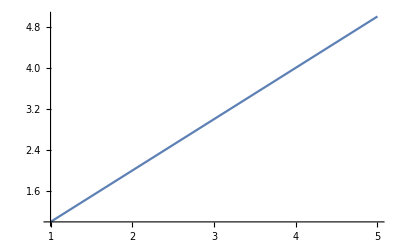

```mathematica
Module[{f,dom},
f=Interpolation[{#,#}&/@Range@5];
dom=f["Domain"][[1]];
Plot[f[x],{x,First@dom,Last@dom}]
]
```





```mathematica
(*quality=(vol-string1[.1])/(string2[.1]-string1[.1]);
Ui=(1-quality)*string3[.1]+quality*string4[.1];

soln=Quiet@FindRoot[{
Ui+heatadded==(1-quality2)*string3[p1]+quality2*string4[p1],
quality2==(vol-string1[p1])/(string2[p1]-string1[p1])
},{{p1,.1},{quality2,0}}];

soln2=Quiet@FindRoot[Ui+heatadded==string5[p2],{p2,a1[[Position[volumes,vol][[1]][[1]]]]}];

(*{soln,soln2}*)
P1=p1/.soln;P2=p2/.soln2;

q=quality2/.soln;
Which[q>1,q=1,q<0,q=0];
p=If[P1≤a1[[Position[volumes,vol][[1]][[1]]]],P1,P2];

Temp=If[q==1∨q==0,string6[Ui+heatadded]-273,PT[p]-273];

plotdata=Join[Thread[{SaturationData[[All,3]],SaturationData[[All,2]]}],Reverse@Thread[{SaturationData[[All,4]],SaturationData[[All,2]]}]];

plot=ListLogLogPlot[plotdata,Joined->True,PlotStyle->{Thick,Blue},PlotRange->{{0,1},All},PlotRangePadding->{Scaled@0.05,None},PlotRangeClipping->False,
Frame->True,FrameLabel->{Row@{"volume (",Superscript["m",3],"/kg)"},"pressure (MPa)"},LabelStyle->{17,Black},ImageSize->{315,400},AspectRatio->Full,
Epilog->{PointSize@0.035,Point@Log@{vol,p}}];

vle=Graphics[{
{GrayLevel@0.7,Rectangle[{0,0},{1,0.4}]},
{GrayLevel@0.5,Rectangle[{0.1,0.1},{0.6,0.3}]},
Text[Style[NumberForm[Temp,{3,1}],55],{0.35,0.2}],
Text[Style["°C",18],{0.65,0.27}],
{Red,Triangle[{{0.77,0.25},{0.82,0.35},{0.87,0.25}}]},
{Blue,Triangle[{{0.77,0.2},{0.82,0.1},{0.87,0.2}}]},
{Opacity[0.5,Gray],Thickness@0.03,Line[{{0.28,1.05},{0.25,1.05},{0.25,0.415},{0.75,0.415},{0.75,1.05},{0.72,1.05}}]},
{GrayLevel@0.1,Thickness@0.03,Line[{{0.281,0.5+0.52*vol},{0.719,0.5+0.52*vol}}],Line[{{0.5,0.51+0.52*vol},{0.5,0.53+0.52*vol}}]},
{Blue,Rectangle[{0.268,0.431},{0.735,0.431+(0.482+0.52*vol-0.431)*(1-q)}]},
{Lighter@Blue,Rectangle[{0.268,0.431+(0.482+0.52*vol-0.431)*(1-q)},{0.735,0.482+0.52*vol}]},
Text[Style[Column[{
Row@{Style["P",Italic]," = ",NumberForm[p,2]," MPa",Spacer@25,Subscript[Style["P",Italic],"a"]," = ",Quiet@NumberForm[P2,2]," MPa"},
Row@{Subscript[Style["P",Italic],"eq"]," = ",NumberForm[P1,2]," MPa",Spacer@30,"quality = ",NumberForm[q,2]}
},Center,Spacings->1],17],{0.5,1.3}]
},ImageSize->{290,400}];

Grid@{{plot,vle}}*)
```

Resize Images

Rotate and Zoom in 3D

Drag Locators

Create and Delete Locators

Slider Zoom

Gamepad Controls

Automatic Animation

Bookmark Animation

Contributed by: XXXX